## Extracting info from 1904.07265

## One data set only

### Data

```mathematica
(* OS: Win, Linux *)
OS="Linux";
```

```mathematica
(* ModeHE, ModeAntiNu, ModeNu *)
(* Tau_minus, Tau_plus *)
```

```mathematica
mode="Nu";sign="minus";
If[mode=="Nu",range=40,range=20];
```

```mathematica
(* Linux *)
```

```mathematica
If[OS=="Linux",data=Import[StringJoin["/home/adriano/Dropbox/Neutrinos/Tau/Data/Mat_WS_In_Mode",mode,"_Tau_",sign,".txt"],"Table"];
data=Table[{.5*i-.25/2,data[[i,2]]},{i,40}];
data2=Import[StringJoin["/home/adriano/Dropbox/Neutrinos/Tau/Data/Mat_WoutS_In_Mode",mode,"_Tau_",sign,".txt"],"Table"];
data2=Table[{.5*i-.25/2,data2[[i,2]]},{i,40}],data=Import[StringJoin["C:\\Users\\Orlando\\Dropbox\\Neutrinos\\Tau\\Data\\Mat_WS_In_Mode",mode,"_Tau_",sign,".txt"],"Table"];
data=Table[{.5*i-.25/2,data[[i,2]]},{i,40}];
data2=Import[StringJoin["C:\\Users\\Orlando\\Dropbox\\Neutrinos\\Tau\\Data\\Mat_WoutS_In_Mode",mode,"_Tau_",sign,".txt"],"Table"];
data2=Table[{.5*i-.25/2,data2[[i,2]]},{i,40}]];
```

### Transformation function

```mathematica
Clear[f]
f[Ere_,Etrue_]:=(*1/σe*)Exp[-1/2((Ere-x)/σe)^2]/.{x->b*Etrue,σe->r*Etrue}/.Thread[{b,r}->{.45,.25}]
```

```mathematica
dataN=Table[Maximize[f[i*.5,x],x][[2,1,2]],{i,40}]
```

{1.11111,2.22222,3.33333,4.44444,5.55556,6.66667,7.77778,8.88889,10.,11.1111,12.2222,13.3333,14.4444,15.5556,16.6667,17.7778,18.8889,20.,21.1111,22.2222,23.3333,24.4444,25.5556,26.6667,27.7778,28.8889,30.,31.1111,32.2222,33.3333,34.4444,35.5556,36.6667,37.7778,38.8889,40.,41.1111,42.2222,43.3333,44.4444}

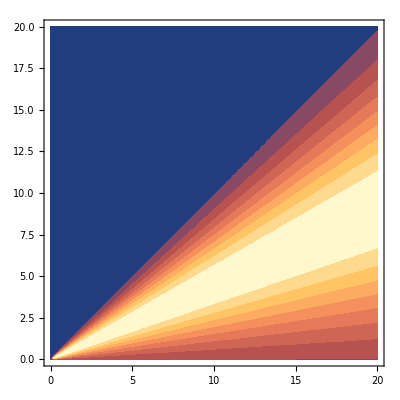

```mathematica
ContourPlot[f[ere,etrue],{etrue,0,20},{ere,0,20},ContourLines->False]//Quiet
```

### Data of Fig 1 by reconstructed energy

```mathematica
Clear[fs,fn]
fs[Ere_,Etrue_]:=If[Etrue<3.1,0,(*1/(Sqrt[2Pi]σe)*)(Exp[-1/2((Ere-x)/σe)^2]/.{x->b*Etrue,σe->r*Etrue}/.Thread[{b,r}->{.45,.25}])]
fn[Ere_,Etrue_]:=If[Etrue<3.1,0,fs[Ere,Etrue]/NIntegrate[fs[ere,Etrue],{ere,0,20}]]
```

```mathematica
(* dN/Subscript[dE, rec]=∫dN/Subscript[dE, true] P(Subscript[E, rec],Subscript[E, true])ⅆ Subscript[E, true] *)
(* doing numerical integration by cutting the integrand *)
dataT=Table[{data2[[j,1]],Sum[fn[data2[[j,1]],data2[[i,1]]]*0.5*data2[[i,2]],{i,40}]},{j,40}];
(*dataT=Table[{.5*j-.25,Sum[fn[0.5*j-.25,.5*i-.25]*0.5*data2[[i,2]],{i,40}]},{j,40}]//Quiet;*)
dtrue=Interpolation@data2;
ndtrue=NIntegrate[dtrue[x],{x,Min@data[[All,1]],Max@data[[All,1]]}]
dre=Interpolation@data;
ndre=NIntegrate[dre[x],{x,Min@data[[All,1]],Max@data[[All,1]]}]
dreInt=Interpolation@dataT;
ndreInt=NIntegrate[dreInt[x],{x,Min@data[[All,1]],Max@data[[All,1]]}]
fac2=ndtrue/ndreInt
(*dataT=Table[{.5*j-.25,fac2*Sum[fn[0.5*j-.25,.5*i]*0.5*data2[[i,2]],{i,40}]},{j,40}]//Quiet;*)
dataT=Table[{data2[[j,1]],fac2*Sum[fn[data2[[j,1]],data2[[i,1]]]*0.5*data2[[i,2]],{i,40}]},{j,40}];
```

54.4842

53.3873

52.517

1.03746

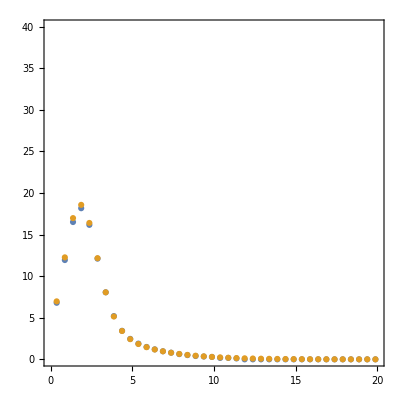

```mathematica
ListPlot[{data,dataT},Frame->True,PlotRange->{{0,20},{0,40}},AspectRatio->1]
```

### Introducing NSI

```mathematica
(* choosing Subscript[ϵ, μτ] only real *)
```

```mathematica
ratio[epS_,ee_]=(-1.3417950781553514+ee (63.6110167803427+(-11.335620650792169+0.48602694541668334 ee) ee)-26.253111607723554 epS+ee (653.3344894860501+ee (-102.78730074393953+4.450961331828265 ee)) epS+(525.5392109465565+ee (50842.27469116989+ee (-8729.640428648672+374.686356791237 ee))) epS^2+(1.3417950781553512+ee (-63.61101678034271+(11.335620650792173-0.48602694541668334 ee) ee)-47.198323815726795 epS+ee (-627.2311837169866+(102.78730074393945-4.450961331828264 ee) ee) epS+(377.44952730016934+ee (47657.51492975174+ee (-8263.66745442748+354.3136432087616 ee))) epS^2) Cos[8.323065282815573/ee]+(-10.918891490242757+ee (3.916905079979295+(-0.17249070990867868-2.1684043449710455*^-19 ee) ee)-59.87086539190307 epS+ee (-21.189965718249404+(-0.7854585909514353-0.06547117846490069 ee) ee) epS+(7086.844664530483+ee (-1565.9397835413793+125.74572752342468 ee)) epS^2) Sin[8.323065282815573/ee])/(-1.3417950781553516+ee (63.61101678034271+(-11.33562065079217+0.48602694541668334 ee) ee)+(1.3417950781553507+ee (-63.611016780342716+(11.335620650792173-0.4860269454166834 ee) ee)) Cos[8.323065282815573/ee]+(-10.918891490242876+ee (3.916905079979277+(-0.17249070990867785-2.1684043449710344*^-19 ee) ee)) Sin[8.323065282815573/ee]);
```

### Plot NSI

```mathematica
(*limite on Subscript[ϵ̃, 23] : 0.08 from my paper with JS *)
(* Subscript[ϵ̃, 23] = Subscript[p, μ] Subscript[ϵ, 23] = 27 Subscript[ϵ, 23] *)
```

```mathematica
Solve[0.08==x*27,x]
```

{{x→0.00296296}}

```mathematica
nsi=0.003;
nsi2=nsi*10;
nsi3=nsi*100;
```

```mathematica
(* Subscript[dN, nsi]/Subscript[dE, rec]=∫Subscript[dN, nsi]/Subscript[dE, true] P(Subscript[E, rec],Subscript[E, true])ⅆ Subscript[E, true] =∫(Subscript[P, NSI](μ->τ))/Subscript[P, SM(μ->τ)] Subscript[dN, sm]/Subscript[dE, true] P(Subscript[E, rec],Subscript[E, true])ⅆ Subscript[E, true] *)
```

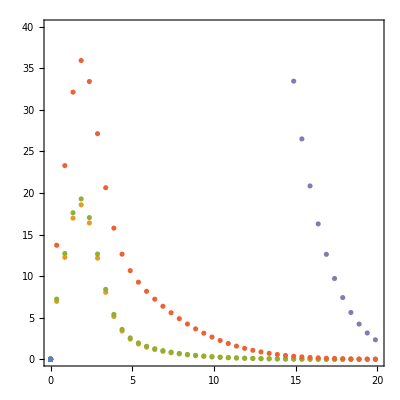

```mathematica
dataNSI=Table[{data2[[j,1]],fac2*Sum[fn[data2[[j,1]],data2[[i,1]]]*0.5*data2[[i,2]]*ratio[nsi,.5*i],{i,40}]},{j,40}]//Quiet;
dataNSI2=Table[{data2[[j,1]],fac2*Sum[fn[data2[[j,1]],data2[[i,1]]]*0.5*data2[[i,2]]*ratio[nsi2,.5*i],{i,40}]},{j,40}]//Quiet;
dataNSI3=Table[{data2[[j,1]],fac2*Sum[fn[data2[[j,1]],data2[[i,1]]]*0.5*data2[[i,2]]*ratio[nsi3,.5*i],{i,40}]},{j,40}]//Quiet;
ListPlot[{data*0,dataT,dataNSI,dataNSI2,dataNSI3},Frame->True,PlotRange->{{0,20},{0,40}},AspectRatio->1]
```

```mathematica
Transpose[{dataT[[All,2]],dataNSI[[All,2]]}]//Chop
```

{{6.97108,7.24059},{12.2612,12.7273},{16.9807,17.6248},{18.5749,19.2868},{16.398,17.0425},{12.1658,12.6663},{8.06067,8.41777},{5.15012,5.40323},{3.41041,3.59934},{2.42756,2.57819},{1.84576,1.97171},{1.46299,1.57092},{1.18441,1.27779},{0.968088,1.04902},{0.794312,0.864338},{0.65239,0.71278},{0.535537,0.587395},{0.438937,0.483254},{0.358948,0.396624},{0.292705,0.324558},{0.237899,0.264676},{0.192641,0.215017},{0.155364,0.173949},{0.124757,0.140098},{0.0997192,0.112303},{0.0793215,0.0895775},{0.0627787,0.0710833},{0.0494268,0.0561073},{0.0387054,0.0440439},{0.0301422,0.0343799},{0.0233408,0.0266819},{0.0179696,0.0205861},{0.0137529,0.0157878},{0.0104624,0.0120341},{0.00791051,0.00911601},{0.00594381,0.00686191},{0.00443777,0.005132},{0.00329194,0.00381313},{0.00242592,0.00281434},{0.00177576,0.0020631}}

```mathematica
(* checking if it is needed to integrate probability over bin *)
```

```mathematica
Table[{NIntegrate[ratio[nsi,ee]/.5,{ee,.5*(i-1),.5*i}],ratio[nsi,.5*i]//Chop,ratio[nsi,.5*i]/NIntegrate[ratio[nsi,ee]/.5,{ee,.5*(i-1),.5*i}]//Chop},{i,40}]//Quiet
Table[{NIntegrate[ratio[nsi2,ee]/.5,{ee,.5*(i-1),.5*i}],ratio[nsi2,.5*i]//Chop,ratio[nsi2,.5*i]/NIntegrate[ratio[nsi2,ee]/.5,{ee,.5*(i-1),.5*i}]//Chop},{i,40}]//Quiet
Table[{NIntegrate[ratio[nsi3,ee]/.5,{ee,.5*(i-1),.5*i}],ratio[nsi3,.5*i]//Chop,ratio[nsi3,.5*i]/NIntegrate[ratio[nsi3,ee]/.5,{ee,.5*(i-1),.5*i}]//Chop},{i,40}]//Quiet
```

{{0.96499,1.032,1.06944},{1.11857,1.03541,0.925658},{1.16206,1.0709,0.921556},{1.04411,1.03588,0.992111},{1.03437,1.03356,0.999219},{1.03343,1.03349,1.00005},{1.03379,1.03419,1.00038},{1.03473,1.03534,1.00059},{1.03606,1.03683,1.00074},{1.03769,1.0386,1.00088},{1.0396,1.04064,1.001},{1.04176,1.04292,1.00111},{1.04416,1.04543,1.00122},{1.04679,1.04818,1.00133},{1.04965,1.05116,1.00144},{1.05274,1.05436,1.00154},{1.05605,1.05778,1.00164},{1.05958,1.06142,1.00174},{1.06333,1.06528,1.00183},{1.0673,1.06936,1.00193},{1.07149,1.07365,1.00202},{1.07589,1.07816,1.00211},{1.08051,1.08289,1.0022},{1.08534,1.08783,1.00229},{1.09039,1.09299,1.00238},{1.09566,1.09836,1.00247},{1.10114,1.10395,1.00255},{1.10683,1.10975,1.00264},{1.11274,1.11577,1.00272},{1.11887,1.122,1.0028},{1.1252,1.12844,1.00288},{1.13176,1.1351,1.00296},{1.13852,1.14198,1.00303},{1.1455,1.14906,1.00311},{1.1527,1.15636,1.00318},{1.1601,1.16388,1.00325},{1.16772,1.1716,1.00332},{1.17556,1.17955,1.00339},{1.18361,1.1877,1.00346},{1.19187,1.19607,1.00353}}

{{-0.0429542,1.40816,-32.7828},{13.4957,1.70903,0.126636},{16.0094,5.26588,0.328924},{2.40293,1.55673,0.647846},{1.42396,1.36176,0.956324},{1.36602,1.38727,1.01556},{1.43127,1.48343,1.03644},{1.54882,1.61982,1.04584},{1.70087,1.78655,1.05037},{1.88096,1.97954,1.05241},{2.0862,2.1968,1.05301},{2.31513,2.43727,1.05276},{2.56693,2.70032,1.05197},{2.84111,2.98558,1.05085},{3.13737,3.2928,1.04954},{3.4555,3.62181,1.04813},{3.79535,3.9725,1.04667},{4.15684,4.34478,1.04521},{4.53989,4.73858,1.04377},{4.94444,5.15388,1.04236},{5.37047,5.59062,1.04099},{5.81793,6.0488,1.03968},{6.2868,6.52837,1.03843},{6.77707,7.02933,1.03722},{7.28872,7.55167,1.03608},{7.82174,8.09537,1.03498},{8.37612,8.66043,1.03394},{8.95186,9.24684,1.03295},{9.54894,9.85459,1.03201},{10.1674,10.4837,1.03111},{10.8071,11.1341,1.03026},{11.4682,11.8058,1.02944},{12.1506,12.4989,1.02867},{12.8543,13.2133,1.02793},{13.5794,13.949,1.02722},{14.3258,14.7061,1.02655},{15.0935,15.4844,1.0259},{15.8825,16.2841,1.02529},{16.6928,17.1051,1.0247},{17.5245,17.9474,1.02413}}

{{-45.3577,13.8956,-0.306355},{1256.95,43.58,0.0346711},{1489.97,399.342,0.26802},{111.209,26.3645,0.237071},{13.2696,7.23657,0.545348},{7.82947,10.1108,1.29137},{14.6461,19.9878,1.36472},{26.6371,33.8402,1.27042},{42.0383,50.6939,1.2059},{60.2143,70.1485,1.16498},{80.8847,92.0121,1.13757},{103.908,116.182,1.11813},{129.206,142.601,1.10367},{156.732,171.231,1.0925},{186.458,202.049,1.08362},{218.365,235.041,1.07637},{252.439,270.196,1.07034},{288.671,307.505,1.06524},{327.056,346.964,1.06087},{367.588,388.569,1.05708},{410.265,432.317,1.05375},{455.082,478.205,1.05081},{502.04,526.231,1.04819},{551.135,576.394,1.04583},{602.366,628.694,1.04371},{655.733,683.128,1.04178},{711.235,739.697,1.04002},{768.871,798.4,1.03841},{828.64,859.236,1.03692},{890.542,922.204,1.03555},{954.577,987.306,1.03429},{1020.74,1054.54,1.03311},{1089.04,1123.9,1.03201},{1159.48,1195.4,1.03098},{1232.04,1269.03,1.03003},{1306.73,1344.79,1.02912},{1383.56,1422.68,1.02828},{1462.52,1502.71,1.02748},{1543.61,1584.86,1.02673},{1626.83,1669.15,1.02601}}

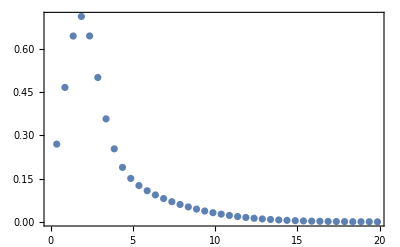

```mathematica
ListPlot[Transpose@{dataT[[All,1]],-dataT[[All,2]]+dataNSI[[All,2]]},Frame->True]
```

```mathematica
Manipulate[Plot[ratio[eps,ee],{ee,.5,20},Frame->True],{eps,0,10^-1}]
```

### Checks

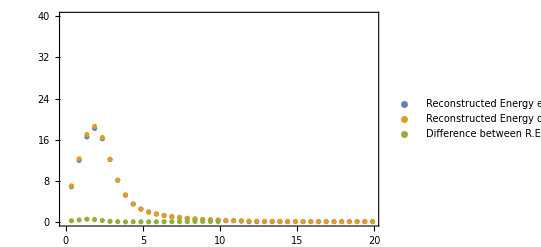

```mathematica
ListPlot[{data,dataT,Transpose[{data[[1;;20,1]],(dataT[[1;;20,2]]-data[[1;;20,2]])}]},Frame->True,PlotLegends->{"Reconstructed Energy extracted from figure","Reconstructed Energy obtained internally","Difference between R.E. obtained internally and extracted from figure"},PlotRange->{All,range}]
```

The NSI modulus is 0.003

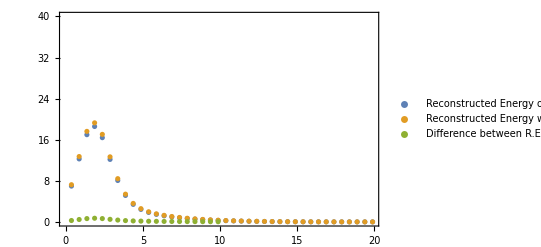

```mathematica
Print["The NSI modulus is ",nsi];ListPlot[{dataT,dataNSI,Transpose[{dataT[[1;;20,1]],(-dataT[[1;;20,2]]+dataNSI[[1;;20,2]])}]},Frame->True,PlotLegends->{"Reconstructed Energy obtained internally","Reconstructed Energy with NSI","Difference between R.E. with NSI and obtained internally"},PlotRange->{All,range}]
```

The NSI modulus is 0.03

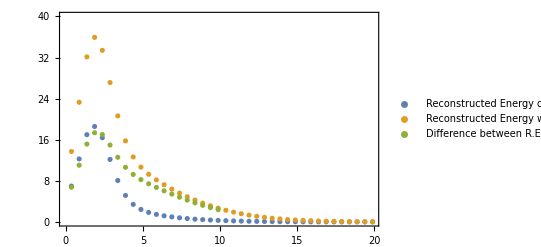

```mathematica
Print["The NSI modulus is ",nsi2];ListPlot[{dataT,dataNSI2,Transpose[{dataT[[1;;20,1]],(-dataT[[1;;20,2]]+dataNSI2[[1;;20,2]])}]},Frame->True,PlotLegends->{"Reconstructed Energy obtained internally","Reconstructed Energy with NSI","Difference between R.E. with NSI and obtained internally"},PlotRange->{All,range}]
```

The NSI modulus is 0.3

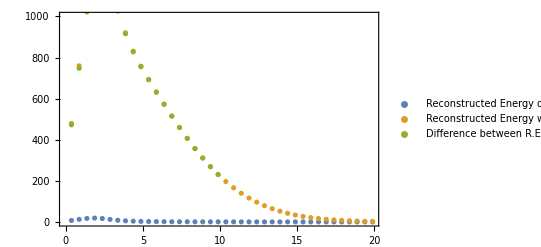

```mathematica
Print["The NSI modulus is ",nsi3];ListPlot[{dataT,dataNSI3,Transpose[{dataT[[1;;20,1]],(-dataT[[1;;20,2]]+dataNSI3[[1;;20,2]])}]},Frame->True,PlotLegends->{"Reconstructed Energy obtained internally","Reconstructed Energy with NSI","Difference between R.E. with NSI and obtained internally"},PlotRange->{All,{0,1000}}]
```

### General Probabilitly ratio

```mathematica
ratioGen[S23_,δ_,epS_,ee_]=(ee (-537.0144158815365 s23^2+(95.922402136029-4.114998188599089 ee) ee s23^2+(537.0144158815365+ee (-95.92240213602899+4.114998188599089 ee)) s23^4+epS^2 (-194626.6461383849+(34963.71557858255-1499.9168397443682 ee) ee+382355.29126830207 s23^2+ee (-69927.4311571651+2999.8336794887364 ee) s23^2+(-391483.50917764+(69927.4311571651-2999.8336794887364 ee) ee) s23^4)+epS s23 √(1-s23^2) (14161.307084011187-28998.778457602955 s23^2+ee (-2589.904857672781+5179.809715345562 s23^2+ee (111.1049510921754-222.2099021843508 s23^2))))-2536.820066237314 epS s23 √(1-s23^2) Sin[8.323065282815573/ee]+1119.5858672098655 ee epS s23 √(1-s23^2) Sin[8.323065282815573/ee]-39.38853098975155 ee^2 epS s23 √(1-s23^2) Sin[8.323065282815573/ee]+5073.640132474628 epS s23^3 √(1-s23^2) Sin[8.323065282815573/ee]-1796.3230913768598 ee epS s23^3 √(1-s23^2) Sin[8.323065282815573/ee]+78.7770619795031 ee^2 epS s23^3 √(1-s23^2) Sin[8.323065282815573/ee]+Cos[δ] (s23 (epS s23 (261.20978051393564-348.27970735191445 s23^2)+4701.776049250849 epS^2 s23^2 √(1-s23^2)-6.44962421022064 √(1-s23^2) (-0.5+1. s23^2))+ee s23 (-403.4052420503069 epS^2 s23^2 √(1-s23^2)+0.5533679589167451 √(1-s23^2) (-0.4999999999999999+1. s23^2)+epS s23 (-22.411402336128184+29.881869781504182 s23^2))+ee^3 (-0.03334587340666304 √(1-s23^2) (-0.5 s23+1. s23^3)+24.30914171345736 epS^2 √(1-s23^2) (-0.5 s23+1. s23^3)+epS (-0.22508464549497562+1.8006771639598036 s23^2-1.800677163959804 s23^4))+ee^2 (0.38865342484877047 √(1-s23^2) (-0.5 s23+1. s23^3)-283.3283467147537 epS^2 √(1-s23^2) (-0.5 s23+1. s23^3)+epS (2.623410617729201-20.987284941833607 s23^2+20.987284941833604 s23^4))+s23 (epS^2 √(1-s23^2) (-12603.870244016523+1081.3929190371105 ee+12603.870244016523 s23^2-1081.3929190371105 ee s23^2)+√(1-s23^2) (8.644629796993499-0.7416961035919825 ee-17.289259593986998 s23^2+1.483392207183965 ee s23^2)+epS s23 (1167.0250225941222-100.12897398491762 ee-933.6200180752978 s23^2+80.1031791879341 ee s23^2)) Sin[8.323065282815573/ee])-8.644629796993499 s23 √(1-s23^2) Sin[δ]+0.7416961035919825 ee s23 √(1-s23^2) Sin[δ]+3.2248121051103213 s23 √(1-s23^2) Sin[8.323065282815573/ee] Sin[δ]-0.2766839794583725 ee s23 √(1-s23^2) Sin[8.323065282815573/ee] Sin[δ]+Sin[8.323065282815573/ee] (-5978.45668107876 ee epS^2+(93.95629874953016-68494.14178840749 epS^2+ee (-33.26524243290481+1.4588344811019092 ee+30228.81841466637 epS^2-1063.4903367232919 ee epS^2)) s23^2+(-93.95629874953016+68494.14178840749 epS^2+ee (33.26524243290481-1.4588344811019092 ee-24250.361733587608 epS^2+1063.4903367232919 ee epS^2)) s23^4+(87.06992683797868-7.470467445376055 ee) epS s23^2 Sin[δ])+Cos[8.323065282815573/ee] (ee ((537.0144158815365+ee (-95.92240213602898+4.114998188599088 ee)) s23^2+(-537.0144158815365+(95.92240213602898-4.114998188599088 ee) ee) s23^4+epS^2 (-6898.001008467854+(-384585.5081691722+(69927.43115716509-2999.8336794887364 ee) ee) s23^2+(391483.50917764+ee (-69927.4311571651+2999.8336794887364 ee)) s23^4)+epS s23 √(1-s23^2) (-14243.90770996934+28998.778457602955 s23^2+ee (2589.904857672781-5179.809715345562 s23^2+ee (-111.1049510921754+222.2099021843508 s23^2))))+s23 (epS s23 (-435.3496341898932+ee (37.352337226880266+(20.987284941833604-1.8006771639598043 ee) ee)+(348.2797073519141+ee (-29.881869781504264+ee (-20.987284941833607+1.800677163959804 ee))) s23^2)+epS^2 √(1-s23^2) (4701.776049250852-4701.776049250846 s23^2+ee (-403.4052420503069+403.4052420503069 s23^2+ee (-141.66417335737682+12.15457085672868 ee+283.3283467147537 s23^2-24.30914171345736 ee s23^2)))+√(1-s23^2) (-3.224812105110321+6.449624210220642 s23^2+ee (0.27668397945837264-0.553367958916745 s23^2+ee (0.19432671242438523-0.01667293670333152 ee-0.38865342484877047 s23^2+0.03334587340666304 ee s23^2)))) Cos[δ]+s23 ((233.40500451882428-20.025794796983522 ee) epS s23-0.7416961035919825 (-11.65521802680122+1. ee) √(1-s23^2)) Sin[δ])+epS ((87.06992683797863+ee (-7.4704674453760544+(-2.623410617729201+0.22508464549497553 ee) ee)) Cos[8.323065282815573/ee+δ]+2.842170943040401*^-14 Sin[8.323065282815573/ee-δ]+(-233.40500451882443+20.025794796983533 ee) s23^2 Sin[δ]+(-233.40500451882437+20.025794796983526 ee) Sin[8.323065282815573/ee+δ]))/(2.7607421580402205+ee (-130.8796094130282+(23.3230292223281-1. ee) ee)+(-2.76074215804022+ee (130.87960941302822+ee (-23.323029222328106+1. ee))) Cos[8.323065282815573/ee]+(22.46560935192947+(-8.05902865451455+0.3548994794121858 ee) ee) Sin[8.323065282815573/ee])/.s23->Sqrt[S23];
```

### Creating data with s23 and NSI

```mathematica
(* Subscript[dN, nsi]/Subscript[dE, rec]=∫Subscript[dN, nsi]/Subscript[dE, true] P(Subscript[E, rec],Subscript[E, true])ⅆ Subscript[E, true] =∫(Subscript[P, NSI](μ->τ))/Subscript[P, SM(μ->τ)] Subscript[dN, sm]/Subscript[dE, true] P(Subscript[E, rec],Subscript[E, true])ⅆ Subscript[E, true] *)
```

```mathematica
(* best-fit used {S23,δ} = {0.582,-2.5} *)
```

```mathematica
passo=.4/10;
dataGen={};dataGenNSI={};dataGenNSI2={};dataGenNSIp={};dataGenNSI2p={};ls23={};
Do[ss23=(0.582)-.2+passo*i;delta=-2.5;AppendTo[ls23,ss23];
AppendTo[dataGen,Table[{data2[[j,1]],fac2*Sum[fn[data2[[j,1]],data2[[i,1]]]*0.5*data2[[i,2]]*ratioGen[ss23,delta,0,.5*i],{i,40}]},{j,40}]];AppendTo[dataGenNSI,Table[{data2[[j,1]],fac2*Sum[fn[data2[[j,1]],data2[[i,1]]]*0.5*data2[[i,2]]*ratioGen[ss23,delta,nsi,.5*i],{i,40}]},{j,40}]];AppendTo[dataGenNSI2,Table[{data2[[j,1]],fac2*Sum[fn[data2[[j,1]],data2[[i,1]]]*0.5*data2[[i,2]]*ratioGen[ss23,delta,nsi2,.5*i],{i,40}]},{j,40}]];AppendTo[dataGenNSIp,Table[{data2[[j,1]],fac2*Sum[fn[data2[[j,1]],data2[[i,1]]]*0.5*data2[[i,2]]*ratioGen[ss23,delta,-nsi,.5*i],{i,40}]},{j,40}]];AppendTo[dataGenNSI2p,Table[{data2[[j,1]],fac2*Sum[fn[data2[[j,1]],data2[[i,1]]]*0.5*data2[[i,2]]*ratioGen[ss23,delta,-nsi2,.5*i],{i,40}]},{j,40}]],{i,0,10}];
```

0.003

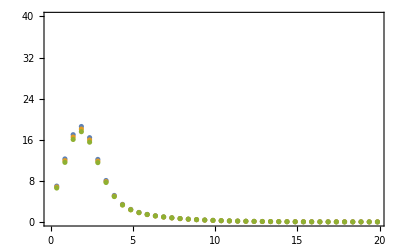
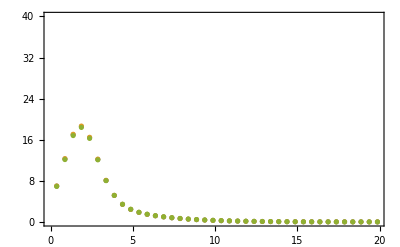
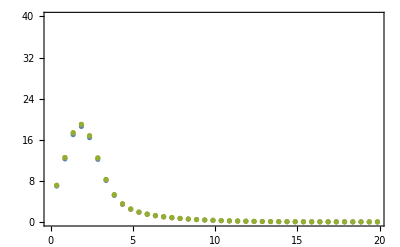
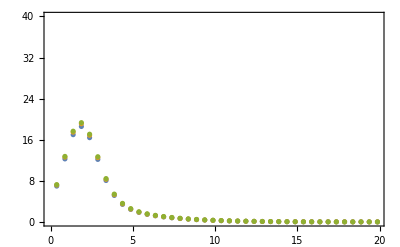
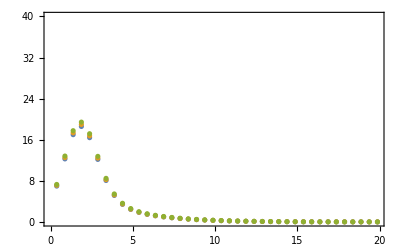
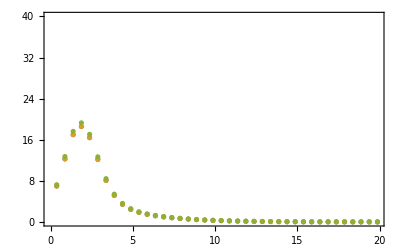
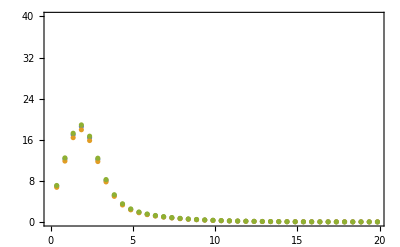
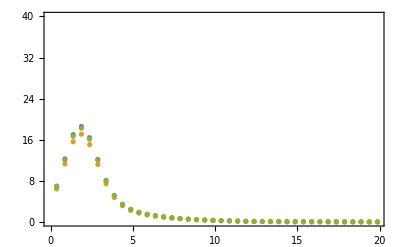

0.03

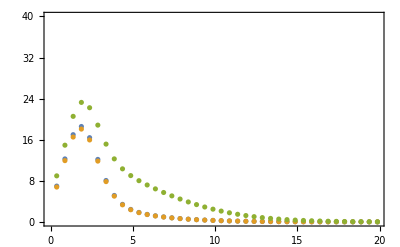
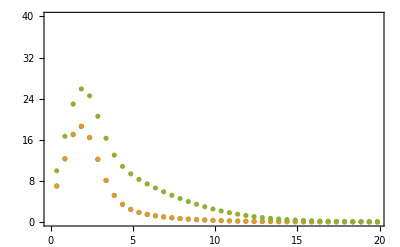
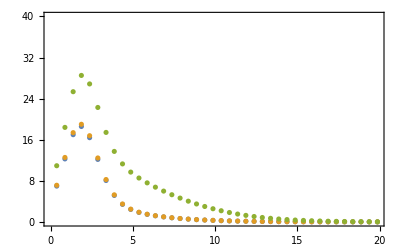
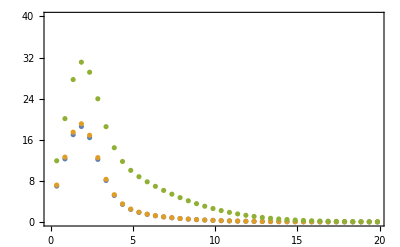
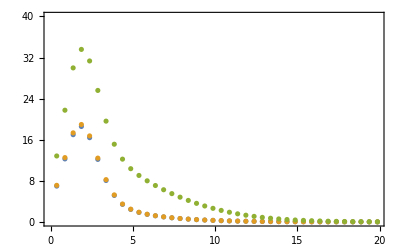
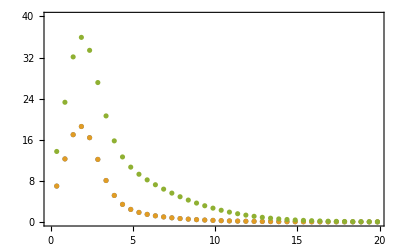
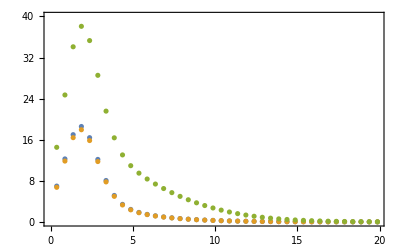
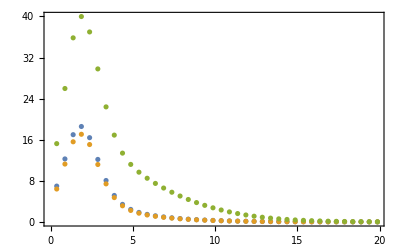

-0.003

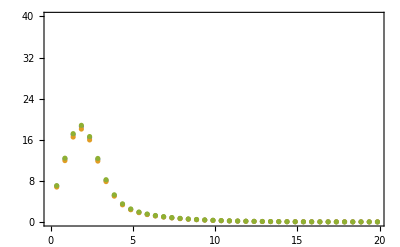
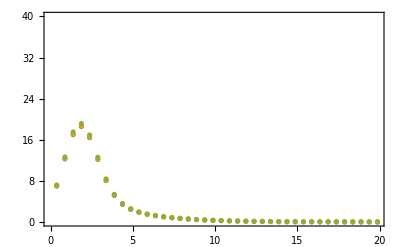
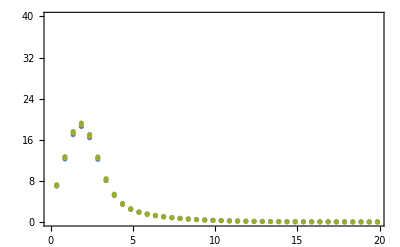
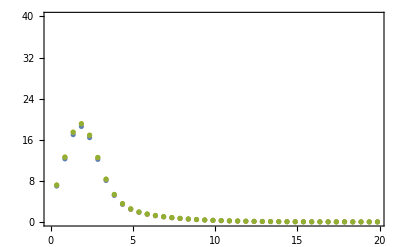
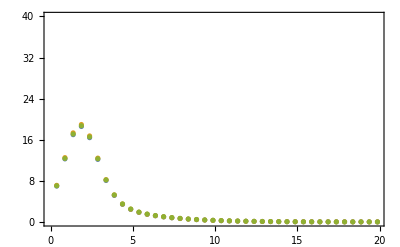
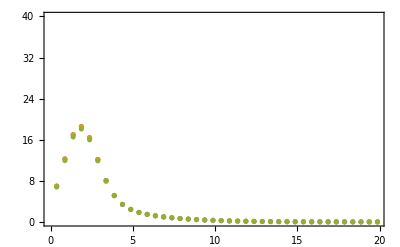
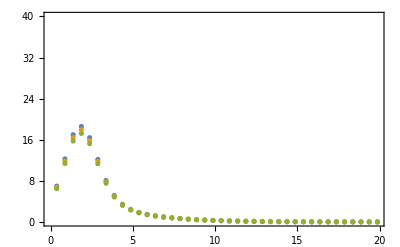
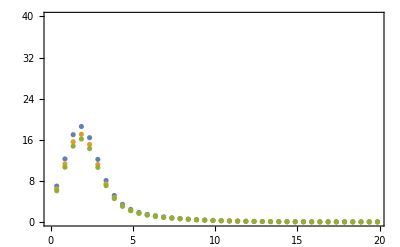

```mathematica
Print[nsi]
Table[ListPlot[{dataT,dataGen[[i]],dataGenNSI[[i]]},PlotRange->{All,range},Frame->True],{i,Length@dataGen}]
Print[nsi2]
Table[ListPlot[{dataT,dataGen[[i]],dataGenNSI2[[i]]},PlotRange->{All,range},Frame->True],{i,Length@dataGen}]
Print[-nsi]
Table[ListPlot[{dataT,dataGen[[i]],dataGenNSIp[[i]]},PlotRange->{All,range},Frame->True],{i,Length@dataGen}]
```

```mathematica
(* checking if it is needed to integrate probability over bin *)
```

```mathematica
Table[{NIntegrate[ratioGen[(Sqrt@0.582)-.1,delta,0,ee]/.5,{ee,.5*(i-1),.5*i}],ratioGen[(Sqrt@0.582)-.1,delta,0,.5*i]//Chop,ratioGen[(Sqrt@0.582)-.1,delta,0,.5*i]/NIntegrate[ratioGen[(Sqrt@0.582)-.1,delta,0,ee]/.5,{ee,.5*(i-1),.5*i}]//Chop},{i,40}]//Quiet
Table[{NIntegrate[ratioGen[(Sqrt@0.582)+.1,delta,0,ee]/.5,{ee,.5*(i-1),.5*i}],ratioGen[(Sqrt@0.582)+.1,delta,0,.5*i]//Chop,ratioGen[(Sqrt@0.582)+.1,delta,0,.5*i]/NIntegrate[ratioGen[(Sqrt@0.582)+.1,delta,0,ee]/.5,{ee,.5*(i-1),.5*i}]//Chop},{i,40}]//Quiet
```

{{0.877206,0.962429,1.09715},{1.02851,1.03866,1.00988},{1.20426,0.84678,0.703154},{0.916722,0.953288,1.03989},{0.970634,0.984752,1.01455},{0.995329,1.00489,1.00961},{1.01309,1.02082,1.00763},{1.02787,1.03465,1.0066},{1.04103,1.04724,1.00597},{1.0532,1.05905,1.00555},{1.06471,1.0703,1.00525},{1.07576,1.08117,1.00502},{1.08647,1.09174,1.00485},{1.09693,1.10208,1.0047},{1.10718,1.11226,1.00458},{1.11728,1.12229,1.00448},{1.12725,1.1322,1.00439},{1.13712,1.14202,1.00431},{1.1469,1.15176,1.00424},{1.1566,1.16144,1.00418},{1.16625,1.17105,1.00412},{1.17584,1.18062,1.00407},{1.18539,1.19015,1.00402},{1.19489,1.19963,1.00397},{1.20436,1.20909,1.00392},{1.21381,1.21852,1.00388},{1.22322,1.22792,1.00384},{1.23261,1.2373,1.0038},{1.24198,1.24666,1.00377},{1.25133,1.256,1.00373},{1.26066,1.26532,1.0037},{1.26998,1.27463,1.00366},{1.27928,1.28393,1.00363},{1.28857,1.29321,1.0036},{1.29785,1.30248,1.00357},{1.30711,1.31174,1.00354},{1.31637,1.321,1.00351},{1.32562,1.33024,1.00349},{1.33486,1.33948,1.00346},{1.34409,1.34871,1.00343}}

{{0.655419,0.748632,1.14222},{0.810253,0.818672,1.01039},{0.967969,0.646053,0.667431},{0.708962,0.741793,1.04631},{0.757298,0.769893,1.01663},{0.779296,0.787785,1.01089},{0.795048,0.801892,1.00861},{0.808115,0.814106,1.00741},{0.819732,0.825215,1.00669},{0.830462,0.835613,1.0062},{0.840604,0.845526,1.00586},{0.850332,0.855088,1.00559},{0.859758,0.86439,1.00539},{0.868956,0.873492,1.00522},{0.877976,0.882437,1.00508},{0.886856,0.891257,1.00496},{0.895623,0.899974,1.00486},{0.904297,0.908607,1.00477},{0.912894,0.91717,1.00468},{0.921426,0.925674,1.00461},{0.929904,0.934126,1.00454},{0.938334,0.942536,1.00448},{0.946725,0.950907,1.00442},{0.95508,0.959246,1.00436},{0.963404,0.967557,1.00431},{0.971701,0.975841,1.00426},{0.979974,0.984104,1.00421},{0.988226,0.992346,1.00417},{0.99646,1.00057,1.00413},{1.00468,1.00878,1.00408},{1.01288,1.01697,1.00404},{1.02106,1.02515,1.004},{1.02924,1.03332,1.00397},{1.0374,1.04148,1.00393},{1.04555,1.04963,1.0039},{1.0537,1.05777,1.00386},{1.06183,1.0659,1.00383},{1.06996,1.07402,1.0038},{1.07808,1.08213,1.00376},{1.08619,1.09024,1.00373}}

### Chi square

```mathematica
(* χ^2 = 2 Sum[ndata - ntrue + ntrue*Log(ntrue/ndata),{i,bin}] *)
```

```mathematica
chis23=Table[Sum[dataGen[[j,i,2]]-dataT[[i,2]]+dataT[[i,2]]*Log[dataT[[i,2]]/dataGen[[j,i,2]]],{i,40}],{j,Length@dataGen}]//Chop
```

{0.0417651,0.00127844,0.0302018,0.045592,0.0243565,0,0.0669707,0.393879,1.24978,3.05311,6.46513}

InterpolatingFunction[…]

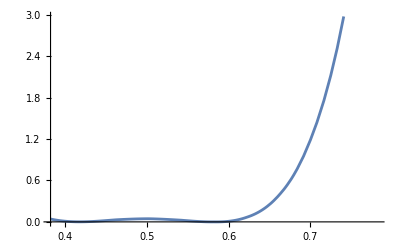

```mathematica
Table[{ls23[[i]],{chis23[[i]]}},{i,Length@ls23}];
Interpolation@%
Plot[%[x],{x,ls23[[1]],ls23[[-1]]}]
```

```mathematica
chiNSI=Table[Sum[dataGenNSI[[j,i,2]]-dataGen[[j,i,2]]+dataGen[[j,i,2]]*Log[dataGen[[j,i,2]]/dataGenNSI[[j,i,2]]],{i,40}],{j,Length@dataGen}]//Chop
chiNSI2=Table[Sum[dataGenNSI2[[j,i,2]]-dataGen[[j,i,2]]+dataGen[[j,i,2]]*Log[dataGen[[j,i,2]]/dataGenNSI2[[j,i,2]]],{i,40}],{j,Length@dataGen}]//Chop
chiNSIp=Table[Sum[dataGenNSIp[[j,i,2]]-dataGen[[j,i,2]]+dataGen[[j,i,2]]*Log[dataGen[[j,i,2]]/dataGenNSIp[[j,i,2]]],{i,40}],{j,Length@dataGen}]//Chop
chiNSI2p=Table[Sum[dataGenNSI2p[[j,i,2]]-dataGen[[j,i,2]]+dataGen[[j,i,2]]*Log[dataGen[[j,i,2]]/dataGenNSI2p[[j,i,2]]],{i,40}],{j,Length@dataGen}]//Chop
```

{0.0380715,0.016042,0.013119,0.0295052,0.0653829,0.120937,0.196377,0.291966,0.408066,0.545208,0.704232}

{50.2196,54.2052,59.5398,66.2571,74.3762,83.9034,94.8329,107.147,120.815,135.788,151.994}

{0.134069,0.0747352,0.0353852,0.0157527,0.015595,0.0346672,0.0726948,0.129339,0.204146,0.296455,0.405233}

{86.171,76.2318,67.7091,60.5938,54.8634,50.4804,47.3902,45.5207,44.7887,45.1249,46.5518}

```mathematica
chis23NSI=Table[Sum[dataGenNSI[[j,i,2]]-dataT[[i,2]]+dataT[[i,2]]*Log[dataT[[i,2]]/dataGenNSI[[j,i,2]]],{i,40}],{j,Length@dataGen}]//Chop
chis23NSI2=Table[Sum[dataGenNSI2[[j,i,2]]-dataT[[i,2]]+dataT[[i,2]]*Log[dataT[[i,2]]/dataGenNSI2[[j,i,2]]],{i,40}],{j,Length@dataGen}]//Chop
chis23NSIp=Table[Sum[dataGenNSIp[[j,i,2]]-dataT[[i,2]]+dataT[[i,2]]*Log[dataT[[i,2]]/dataGenNSIp[[j,i,2]]],{i,40}],{j,Length@dataGen}]//Chop
chis23NSI2p=Table[Sum[dataGenNSI2p[[j,i,2]]-dataT[[i,2]]+dataT[[i,2]]*Log[dataT[[i,2]]/dataGenNSI2p[[j,i,2]]],{i,40}],{j,Length@dataGen}]//Chop
```

{0.145607,0.0130478,0.0557808,0.131812,0.161555,0.120936,0.0418771,0.0205965,0.236567,0.98918,2.76826}

{48.6736,54.5243,61.267,68.6088,76.2534,83.9034,91.2583,98.01,103.835,108.383,111.258}

{0.0344902,0.0938085,0.117281,0.0831128,0.0254034,0.0346676,0.265912,0.956332,2.45797,5.29697,10.2857}

{83.5249,76.6689,69.6468,62.7507,56.268,50.4804,45.6579,42.0428,39.8182,39.049,39.5855}

```mathematica
Join[Table[{ls23[[i]],nsi,{chis23NSI[[i]]}},{i,Length@ls23}],Table[{ls23[[i]],nsi2,{chis23NSI2[[i]]}},{i,Length@ls23}],Table[{ls23[[i]],-nsi,{chis23NSIp[[i]]}},{i,Length@ls23}],Table[{ls23[[i]],-nsi2,{chis23NSI2p[[i]]}},{i,Length@ls23}],Table[{ls23[[i]],nsi*0,{chis23[[i]]}},{i,Length@ls23}]];
func=Interpolation@%
```

InterpolatingFunction[…]

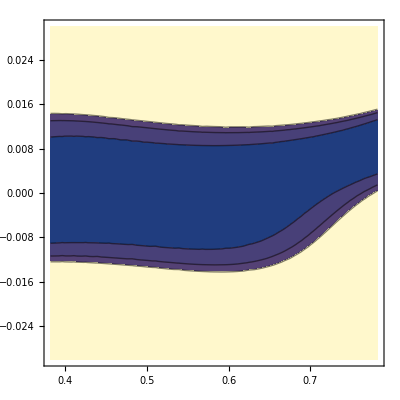

```mathematica
ContourPlot[func[s23,nsii],{s23,ls23[[1]],ls23[[-1]]},{nsii,-.03,.03},Contours->{2.3,4.6,6.}]
```

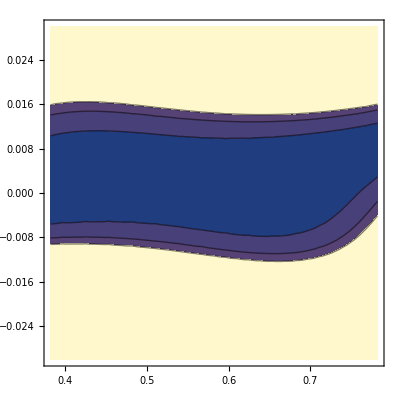

```mathematica
-
```

### Creating data with s23 and δ

```mathematica
(* Subscript[dN, nsi]/Subscript[dE, rec]=∫Subscript[dN, nsi]/Subscript[dE, true] P(Subscript[E, rec],Subscript[E, true])ⅆ Subscript[E, true] =∫(Subscript[P, NSI](μ->τ))/Subscript[P, SM(μ->τ)] Subscript[dN, sm]/Subscript[dE, true] P(Subscript[E, rec],Subscript[E, true])ⅆ Subscript[E, true] *)
```

```mathematica
(* best-fit used {S23,δ} = {0.582,-2.5} *)
```

```mathematica
passos23=.4/10;
passodelta=2./10;
dataGen={};ls23d={};
Clear[delta,ss23];
Do[ss23=(0.582)-.2+passos23*i;
Do[delta=-2.5-1.+passodelta*k;AppendTo[ls23d,{ss23,delta}];
AppendTo[dataGen,Table[{data2[[j,1]],fac2*Sum[fn[data2[[j,1]],data2[[i,1]]]*0.5*data2[[i,2]]*ratioGen[ss23,delta,0,.5*i],{i,40}]},{j,40}]],{k,0,10}],{i,0,10}]//Quiet;
```

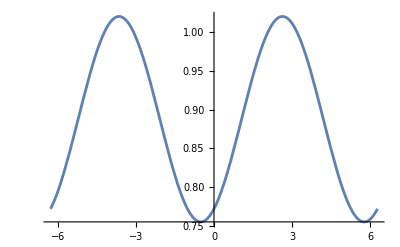

```mathematica
Plot[ratioGen[(0.582),del,0,2],{del,-2*Pi,2*Pi}]
```

```mathematica
dataGen//Dimensions
```

{121,40,2}

35

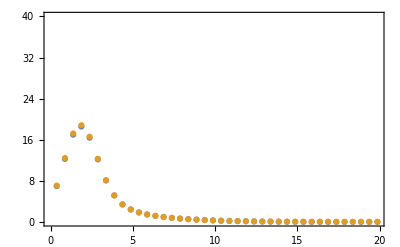

```mathematica
xx=RandomInteger[{1,Length@ls23d}]
ListPlot[{dataT,dataGen[[xx]]},PlotRange->{All,range},Frame->True]
```

### Chi square

```mathematica
(* χ^2 = 2 Sum[ndata - ntrue + ntrue*Log(ntrue/ndata),{i,bin}] *)
```

```mathematica
chis23d=Table[Sum[dataGen[[j,i,2]]-dataT[[i,2]]+dataT[[i,2]]*Log[dataT[[i,2]]/dataGen[[j,i,2]]],{i,40}],{j,Length@dataGen}]//Chop
```

{0.388688,0.128467,0.0204679,0.015481,0.0653107,0.12983,0.182048,0.211072,0.222916,0.239223,0.294002,0.168682,0.0213053,0.00806994,0.0776656,0.180342,0.274922,0.333861,0.346207,0.318417,0.273087,0.245708,0.0895912,0.0073862,0.0489266,0.161663,0.294925,0.406915,0.469759,0.472466,0.421752,0.340776,0.265897,0.0724878,0.0102742,0.0686238,0.194604,0.337258,0.454595,0.51864,0.518389,0.460639,0.368721,0.279264,0.0938652,0.00720276,0.0449956,0.15478,0.285949,0.396747,0.459323,0.462689,0.413544,0.335007,0.263379,0.182515,0.0260575,0.00519212,0.0687802,0.167198,0.259355,0.317752,0.33144,0.306842,0.266477,0.245714,0.423364,0.14908,0.0292794,0.0150083,0.0582625,0.119043,0.170427,0.201529,0.218307,0.242287,0.307296,0.969389,0.524375,0.26142,0.134623,0.0982298,0.113756,0.155076,0.211378,0.287968,0.404969,0.594039,2.06537,1.38882,0.932133,0.653306,0.509458,0.464024,0.491881,0.582297,0.73972,0.982451,1.33933,4.09204,3.11066,2.39964,1.92169,1.63738,1.51243,1.52289,1.65811,1.92145,2.32895,2.90596,7.65016,6.27044,5.22837,4.49209,4.02603,3.7985,3.78683,3.98038,4.38121,5.00265,5.8659}

```mathematica
Table[{ls23d[[i]],{chis23d[[i]]}},{i,Length@ls23d}]
```

{{{0.382,-3.5},{0.388688}},{{0.382,-3.3},{0.128467}},{{0.382,-3.1},{0.0204679}},{{0.382,-2.9},{0.015481}},{{0.382,-2.7},{0.0653107}},{{0.382,-2.5},{0.12983}},{{0.382,-2.3},{0.182048}},{{0.382,-2.1},{0.211072}},{{0.382,-1.9},{0.222916}},{{0.382,-1.7},{0.239223}},{{0.382,-1.5},{0.294002}},{{0.422,-3.5},{0.168682}},{{0.422,-3.3},{0.0213053}},{{0.422,-3.1},{0.00806994}},{{0.422,-2.9},{0.0776656}},{{0.422,-2.7},{0.180342}},{{0.422,-2.5},{0.274922}},{{0.422,-2.3},{0.333861}},{{0.422,-2.1},{0.346207}},{{0.422,-1.9},{0.318417}},{{0.422,-1.7},{0.273087}},{{0.422,-1.5},{0.245708}},{{0.462,-3.5},{0.0895912}},{{0.462,-3.3},{0.0073862}},{{0.462,-3.1},{0.0489266}},{{0.462,-2.9},{0.161663}},{{0.462,-2.7},{0.294925}},{{0.462,-2.5},{0.406915}},{{0.462,-2.3},{0.469759}},{{0.462,-2.1},{0.472466}},{{0.462,-1.9},{0.421752}},{{0.462,-1.7},{0.340776}},{{0.462,-1.5},{0.265897}},{{0.502,-3.5},{0.0724878}},{{0.502,-3.3},{0.0102742}},{{0.502,-3.1},{0.0686238}},{{0.502,-2.9},{0.194604}},{{0.502,-2.7},{0.337258}},{{0.502,-2.5},{0.454595}},{{0.502,-2.3},{0.51864}},{{0.502,-2.1},{0.518389}},{{0.502,-1.9},{0.460639}},{{0.502,-1.7},{0.368721}},{{0.502,-1.5},{0.279264}},{{0.542,-3.5},{0.0938652}},{{0.542,-3.3},{0.00720276}},{{0.542,-3.1},{0.0449956}},{{0.542,-2.9},{0.15478}},{{0.542,-2.7},{0.285949}},{{0.542,-2.5},{0.396747}},{{0.542,-2.3},{0.459323}},{{0.542,-2.1},{0.462689}},{{0.542,-1.9},{0.413544}},{{0.542,-1.7},{0.335007}},{{0.542,-1.5},{0.263379}},{{0.582,-3.5},{0.182515}},{{0.582,-3.3},{0.0260575}},{{0.582,-3.1},{0.00519212}},{{0.582,-2.9},{0.0687802}},{{0.582,-2.7},{0.167198}},{{0.582,-2.5},{0.259355}},{{0.582,-2.3},{0.317752}},{{0.582,-2.1},{0.33144}},{{0.582,-1.9},{0.306842}},{{0.582,-1.7},{0.266477}},{{0.582,-1.5},{0.245714}},{{0.622,-3.5},{0.423364}},{{0.622,-3.3},{0.14908}},{{0.622,-3.1},{0.0292794}},{{0.622,-2.9},{0.0150083}},{{0.622,-2.7},{0.0582625}},{{0.622,-2.5},{0.119043}},{{0.622,-2.3},{0.170427}},{{0.622,-2.1},{0.201529}},{{0.622,-1.9},{0.218307}},{{0.622,-1.7},{0.242287}},{{0.622,-1.5},{0.307296}},{{0.662,-3.5},{0.969389}},{{0.662,-3.3},{0.524375}},{{0.662,-3.1},{0.26142}},{{0.662,-2.9},{0.134623}},{{0.662,-2.7},{0.0982298}},{{0.662,-2.5},{0.113756}},{{0.662,-2.3},{0.155076}},{{0.662,-2.1},{0.211378}},{{0.662,-1.9},{0.287968}},{{0.662,-1.7},{0.404969}},{{0.662,-1.5},{0.594039}},{{0.702,-3.5},{2.06537}},{{0.702,-3.3},{1.38882}},{{0.702,-3.1},{0.932133}},{{0.702,-2.9},{0.653306}},{{0.702,-2.7},{0.509458}},{{0.702,-2.5},{0.464024}},{{0.702,-2.3},{0.491881}},{{0.702,-2.1},{0.582297}},{{0.702,-1.9},{0.73972}},{{0.702,-1.7},{0.982451}},{{0.702,-1.5},{1.33933}},{{0.742,-3.5},{4.09204}},{{0.742,-3.3},{3.11066}},{{0.742,-3.1},{2.39964}},{{0.742,-2.9},{1.92169}},{{0.742,-2.7},{1.63738}},{{0.742,-2.5},{1.51243}},{{0.742,-2.3},{1.52289}},{{0.742,-2.1},{1.65811}},{{0.742,-1.9},{1.92145}},{{0.742,-1.7},{2.32895}},{{0.742,-1.5},{2.90596}},{{0.782,-3.5},{7.65016}},{{0.782,-3.3},{6.27044}},{{0.782,-3.1},{5.22837}},{{0.782,-2.9},{4.49209}},{{0.782,-2.7},{4.02603}},{{0.782,-2.5},{3.7985}},{{0.782,-2.3},{3.78683}},{{0.782,-2.1},{3.98038}},{{0.782,-1.9},{4.38121}},{{0.782,-1.7},{5.00265}},{{0.782,-1.5},{5.8659}}}

InterpolatingFunction[…]

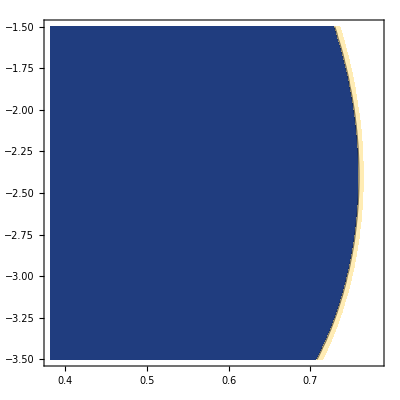

```mathematica
Table[{ls23d[[i]],{chis23d[[i]]}},{i,Length@ls23d}];
func=Interpolation@%
ContourPlot[func[s23,del],{s23,Min@ls23d[[All,1]],Max@ls23d[[All,1]]},{del,Min@ls23d[[All,2]],Max@ls23d[[All,2]]},Contours->{2.3,4.6,6.}]
```

### Check probability

```mathematica
ratioGen[S23,dcp,0,ee]
Table[ratioGen[0.582,-2.15,0,ee],{ee,1,10}]
```

(0.-0.555354 ee √(1-S23) √S23 Cos[dcp]+ee (0.-8.22111 S23+8.22111 S23^2+0.555354 √(1-S23) √S23 Cos[dcp]) Cos[8.32307/ee]+S23 (0.+8.22111 ee-1.44661 Sin[8.32307/ee])-0.555354 ee √(1-S23) √S23 Sin[dcp] Sin[8.32307/ee]+S23^2 (0.-8.22111 ee+1.44661 Sin[8.32307/ee]))/(2.26532 ee-2.26532 ee Cos[8.32307/ee]+1.11022×10^-16 ee Cos[16.6461/ee]-0.351926 Sin[8.32307/ee])

{1.01241,0.89694,0.967545,1.00861,1.04238,1.07306,1.10209,1.13014,1.15755,1.18452}

## All data sets - s23 and dcp

### Data Nu

```mathematica
(* OS: Win, Linux *)
OS="Linux";
```

```mathematica
(* ModeHE, ModeAntiNu, ModeNu *)
(* Tau_minus, Tau_plus *)
```

```mathematica
mode="Nu";sign="minus";
If[mode=="Nu",range=40,range=20];
```

```mathematica
(* Linux *)
```

```mathematica
If[OS=="Linux",data=Import[StringJoin["/home/adriano/Dropbox/Neutrinos/Tau/Data/Mat_WS_In_Mode",mode,"_Tau_",sign,".txt"],"Table"];
data=Table[{.5*i-.25/2,data[[i,2]]},{i,40}];
data2=Import[StringJoin["/home/adriano/Dropbox/Neutrinos/Tau/Data/Mat_WoutS_In_Mode",mode,"_Tau_",sign,".txt"],"Table"];
data2=Table[{.5*i-.25/2,data2[[i,2]]},{i,40}],data=Import[StringJoin["C:\\Users\\Orlando\\Dropbox\\Neutrinos\\Tau\\Data\\Mat_WS_In_Mode",mode,"_Tau_",sign,".txt"],"Table"];
data=Table[{.5*i-.25/2,data[[i,2]]},{i,40}];
data2=Import[StringJoin["C:\\Users\\Orlando\\Dropbox\\Neutrinos\\Tau\\Data\\Mat_WoutS_In_Mode",mode,"_Tau_",sign,".txt"],"Table"];
data2=Table[{.5*i-.25/2,data2[[i,2]]},{i,40}]];
```

### Data of Fig 1 by reconstructed energy

```mathematica
Clear[fs,fn]
fs[Ere_,Etrue_]:=If[Etrue<3.1,0,(*1/(Sqrt[2Pi]σe)*)(Exp[-1/2((Ere-x)/σe)^2]/.{x->b*Etrue,σe->r*Etrue}/.Thread[{b,r}->{.45,.25}])]
fn[Ere_,Etrue_]:=If[Etrue<3.1,0,fs[Ere,Etrue]/NIntegrate[fs[ere,Etrue],{ere,0,20}]]
```

```mathematica
(* dN/Subscript[dE, rec]=∫dN/Subscript[dE, true] P(Subscript[E, rec],Subscript[E, true])ⅆ Subscript[E, true] *)
(* doing numerical integration by cutting the integrand *)
dataT=Table[{data2[[j,1]],Sum[fn[data2[[j,1]],data2[[i,1]]]*0.5*data2[[i,2]],{i,40}]},{j,40}];
(*dataT=Table[{.5*j-.25,Sum[fn[0.5*j-.25,.5*i-.25]*0.5*data2[[i,2]],{i,40}]},{j,40}]//Quiet;*)
dtrue=Interpolation@data2;
ndtrue=NIntegrate[dtrue[x],{x,Min@data[[All,1]],Max@data[[All,1]]}]
dre=Interpolation@data;
ndre=NIntegrate[dre[x],{x,Min@data[[All,1]],Max@data[[All,1]]}]
dreInt=Interpolation@dataT;
ndreInt=NIntegrate[dreInt[x],{x,Min@data[[All,1]],Max@data[[All,1]]}]
fac2=ndtrue/ndreInt
(*dataT=Table[{.5*j-.25,fac2*Sum[fn[0.5*j-.25,.5*i]*0.5*data2[[i,2]],{i,40}]},{j,40}]//Quiet;*)
dataT=Table[{data2[[j,1]],fac2*Sum[fn[data2[[j,1]],data2[[i,1]]]*0.5*data2[[i,2]],{i,40}]},{j,40}];
```

54.4842

53.3873

52.517

1.03746

```mathematica
ListPlot[{data,dataT},Frame->True,PlotRange->{{0,20},{0,40}},AspectRatio->1]
```

-Graphics-

### General Probability ratio

```mathematica
ratioGen[S23_,δ_,epS_,ee_]=(ee (-537.0144158815365 s23^2+(95.922402136029-4.114998188599089 ee) ee s23^2+(537.0144158815365+ee (-95.92240213602899+4.114998188599089 ee)) s23^4+epS^2 (-194626.6461383849+(34963.71557858255-1499.9168397443682 ee) ee+382355.29126830207 s23^2+ee (-69927.4311571651+2999.8336794887364 ee) s23^2+(-391483.50917764+(69927.4311571651-2999.8336794887364 ee) ee) s23^4)+epS s23 √(1-s23^2) (14161.307084011187-28998.778457602955 s23^2+ee (-2589.904857672781+5179.809715345562 s23^2+ee (111.1049510921754-222.2099021843508 s23^2))))-2536.820066237314 epS s23 √(1-s23^2) Sin[8.323065282815573/ee]+1119.5858672098655 ee epS s23 √(1-s23^2) Sin[8.323065282815573/ee]-39.38853098975155 ee^2 epS s23 √(1-s23^2) Sin[8.323065282815573/ee]+5073.640132474628 epS s23^3 √(1-s23^2) Sin[8.323065282815573/ee]-1796.3230913768598 ee epS s23^3 √(1-s23^2) Sin[8.323065282815573/ee]+78.7770619795031 ee^2 epS s23^3 √(1-s23^2) Sin[8.323065282815573/ee]+Cos[δ] (s23 (epS s23 (261.20978051393564-348.27970735191445 s23^2)+4701.776049250849 epS^2 s23^2 √(1-s23^2)-6.44962421022064 √(1-s23^2) (-0.5+1. s23^2))+ee s23 (-403.4052420503069 epS^2 s23^2 √(1-s23^2)+0.5533679589167451 √(1-s23^2) (-0.4999999999999999+1. s23^2)+epS s23 (-22.411402336128184+29.881869781504182 s23^2))+ee^3 (-0.03334587340666304 √(1-s23^2) (-0.5 s23+1. s23^3)+24.30914171345736 epS^2 √(1-s23^2) (-0.5 s23+1. s23^3)+epS (-0.22508464549497562+1.8006771639598036 s23^2-1.800677163959804 s23^4))+ee^2 (0.38865342484877047 √(1-s23^2) (-0.5 s23+1. s23^3)-283.3283467147537 epS^2 √(1-s23^2) (-0.5 s23+1. s23^3)+epS (2.623410617729201-20.987284941833607 s23^2+20.987284941833604 s23^4))+s23 (epS^2 √(1-s23^2) (-12603.870244016523+1081.3929190371105 ee+12603.870244016523 s23^2-1081.3929190371105 ee s23^2)+√(1-s23^2) (8.644629796993499-0.7416961035919825 ee-17.289259593986998 s23^2+1.483392207183965 ee s23^2)+epS s23 (1167.0250225941222-100.12897398491762 ee-933.6200180752978 s23^2+80.1031791879341 ee s23^2)) Sin[8.323065282815573/ee])-8.644629796993499 s23 √(1-s23^2) Sin[δ]+0.7416961035919825 ee s23 √(1-s23^2) Sin[δ]+3.2248121051103213 s23 √(1-s23^2) Sin[8.323065282815573/ee] Sin[δ]-0.2766839794583725 ee s23 √(1-s23^2) Sin[8.323065282815573/ee] Sin[δ]+Sin[8.323065282815573/ee] (-5978.45668107876 ee epS^2+(93.95629874953016-68494.14178840749 epS^2+ee (-33.26524243290481+1.4588344811019092 ee+30228.81841466637 epS^2-1063.4903367232919 ee epS^2)) s23^2+(-93.95629874953016+68494.14178840749 epS^2+ee (33.26524243290481-1.4588344811019092 ee-24250.361733587608 epS^2+1063.4903367232919 ee epS^2)) s23^4+(87.06992683797868-7.470467445376055 ee) epS s23^2 Sin[δ])+Cos[8.323065282815573/ee] (ee ((537.0144158815365+ee (-95.92240213602898+4.114998188599088 ee)) s23^2+(-537.0144158815365+(95.92240213602898-4.114998188599088 ee) ee) s23^4+epS^2 (-6898.001008467854+(-384585.5081691722+(69927.43115716509-2999.8336794887364 ee) ee) s23^2+(391483.50917764+ee (-69927.4311571651+2999.8336794887364 ee)) s23^4)+epS s23 √(1-s23^2) (-14243.90770996934+28998.778457602955 s23^2+ee (2589.904857672781-5179.809715345562 s23^2+ee (-111.1049510921754+222.2099021843508 s23^2))))+s23 (epS s23 (-435.3496341898932+ee (37.352337226880266+(20.987284941833604-1.8006771639598043 ee) ee)+(348.2797073519141+ee (-29.881869781504264+ee (-20.987284941833607+1.800677163959804 ee))) s23^2)+epS^2 √(1-s23^2) (4701.776049250852-4701.776049250846 s23^2+ee (-403.4052420503069+403.4052420503069 s23^2+ee (-141.66417335737682+12.15457085672868 ee+283.3283467147537 s23^2-24.30914171345736 ee s23^2)))+√(1-s23^2) (-3.224812105110321+6.449624210220642 s23^2+ee (0.27668397945837264-0.553367958916745 s23^2+ee (0.19432671242438523-0.01667293670333152 ee-0.38865342484877047 s23^2+0.03334587340666304 ee s23^2)))) Cos[δ]+s23 ((233.40500451882428-20.025794796983522 ee) epS s23-0.7416961035919825 (-11.65521802680122+1. ee) √(1-s23^2)) Sin[δ])+epS ((87.06992683797863+ee (-7.4704674453760544+(-2.623410617729201+0.22508464549497553 ee) ee)) Cos[8.323065282815573/ee+δ]+2.842170943040401*^-14 Sin[8.323065282815573/ee-δ]+(-233.40500451882443+20.025794796983533 ee) s23^2 Sin[δ]+(-233.40500451882437+20.025794796983526 ee) Sin[8.323065282815573/ee+δ]))/(2.7607421580402205+ee (-130.8796094130282+(23.3230292223281-1. ee) ee)+(-2.76074215804022+ee (130.87960941302822+ee (-23.323029222328106+1. ee))) Cos[8.323065282815573/ee]+(22.46560935192947+(-8.05902865451455+0.3548994794121858 ee) ee) Sin[8.323065282815573/ee])/.s23->Sqrt[S23];
```

### Creating data with s23 and δ

```mathematica
(* Subscript[dN, nsi]/Subscript[dE, rec]=∫Subscript[dN, nsi]/Subscript[dE, true] P(Subscript[E, rec],Subscript[E, true])ⅆ Subscript[E, true] =∫(Subscript[P, NSI](μ->τ))/Subscript[P, SM(μ->τ)] Subscript[dN, sm]/Subscript[dE, true] P(Subscript[E, rec],Subscript[E, true])ⅆ Subscript[E, true] *)
```

```mathematica
(* best-fit used {S23,δ} = {0.582,-2.5} *)
```

```mathematica
passos23=.4/10;
passodelta=2./10;
dataGen={};ls23d={};
Clear[delta,ss23];
Do[ss23=(0.582)-.2+passos23*i;
Do[delta=Pi*(-1.+passodelta*k);AppendTo[ls23d,{ss23,delta}];
AppendTo[dataGen,Table[{data2[[j,1]],fac2*Sum[fn[data2[[j,1]],data2[[i,1]]]*0.5*data2[[i,2]]*ratioGen[ss23,delta,0,.5*i],{i,40}]},{j,40}]],{k,0,10}],{i,0,10}]//Quiet;
```

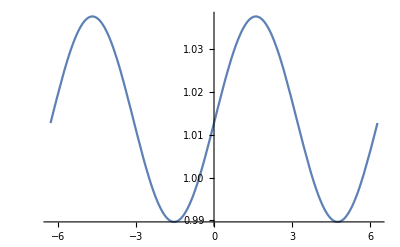

```mathematica
Plot[ratioGen[(0.582),del,0,2],{del,-2*Pi,2*Pi}]
```

```mathematica
dataGen//Dimensions
```

{121,40,2}

22

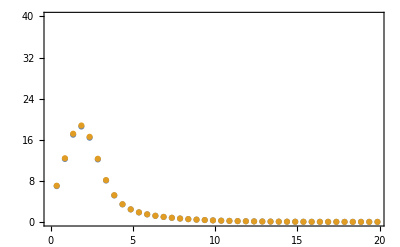

```mathematica
xx=RandomInteger[{1,Length@ls23d}]
ListPlot[{dataT,dataGen[[xx]]},PlotRange->{All,range},Frame->True]
```

### Chi square

```mathematica
(* χ^2 = 2 Sum[ndata - ntrue + ntrue*Log(ntrue/ndata),{i,bin}] *)
```

```mathematica
chis23d=Table[Sum[dataGen[[j,i,2]]-dataT[[i,2]]+dataT[[i,2]]*Log[dataT[[i,2]]/dataGen[[j,i,2]]],{i,40}],{j,Length@dataGen}]//Chop
```

{0.0269286,0.0414439,0.0546922,0.0590627,0.0517798,0.0375102,0.023947,0.0157719,0.0135848,0.0171438,0.0269286,0.0056676,0.00133194,0.000107268,0.0000329362,0.000429671,0.0031485,0.00906881,0.0151177,0.0165889,0.0122312,0.0056676,0.0449538,0.0304462,0.0223745,0.0215057,0.0278334,0.0410531,0.057733,0.0704003,0.0719369,0.0614263,0.0449538,0.0628698,0.0458753,0.0367736,0.0368328,0.0460479,0.0631183,0.0828531,0.0963322,0.0962381,0.0826239,0.0628698,0.0370159,0.0245518,0.018702,0.0195993,0.0272754,0.0411252,0.0569,0.0669108,0.0652744,0.0529805,0.0370159,0.00131191,3.64809×10^-7,0.000313918,0.000141566,0.000295057,0.00315588,0.00837354,0.0119981,0.0106981,0.00569659,0.00131191,0.0503586,0.0666857,0.0747837,0.0696868,0.0544903,0.0375623,0.0257877,0.0213887,0.024219,0.0343157,0.0503586,0.352629,0.393232,0.409448,0.393344,0.352673,0.305674,0.270355,0.25757,0.270512,0.305796,0.352629,1.17667,1.2487,1.272,1.23608,1.15679,1.0673,1.0014,0.981226,1.01293,1.08649,1.17667,2.93985,3.05155,3.07931,3.01116,2.87591,2.7283,2.62382,2.59879,2.66142,2.79052,2.93985,6.30146,6.46301,6.49067,6.37271,6.15787,5.93154,5.77859,5.75318,5.86391,6.07205,6.30146}

```mathematica
dataSet1=chis23d;
```

### Data AntiNu

```mathematica
(* OS: Win, Linux *)
OS="Linux";
```

```mathematica
(* ModeHE, ModeAntiNu, ModeNu *)
(* Tau_minus, Tau_plus *)
```

```mathematica
mode="AntiNu";sign="plus";
If[mode=="Nu",range=40,range=20];
```

```mathematica
(* Linux *)
```

```mathematica
If[OS=="Linux",data=Import[StringJoin["/home/adriano/Dropbox/Neutrinos/Tau/Data/Mat_WS_In_Mode",mode,"_Tau_",sign,".txt"],"Table"];
data=Table[{.5*i-.25/2,data[[i,2]]},{i,40}];
data2=Import[StringJoin["/home/adriano/Dropbox/Neutrinos/Tau/Data/Mat_WoutS_In_Mode",mode,"_Tau_",sign,".txt"],"Table"];
data2=Table[{.5*i-.25/2,data2[[i,2]]},{i,40}],data=Import[StringJoin["C:\\Users\\Orlando\\Dropbox\\Neutrinos\\Tau\\Data\\Mat_WS_In_Mode",mode,"_Tau_",sign,".txt"],"Table"];
data=Table[{.5*i-.25/2,data[[i,2]]},{i,40}];
data2=Import[StringJoin["C:\\Users\\Orlando\\Dropbox\\Neutrinos\\Tau\\Data\\Mat_WoutS_In_Mode",mode,"_Tau_",sign,".txt"],"Table"];
data2=Table[{.5*i-.25/2,data2[[i,2]]},{i,40}]];
```

### Data of Fig 1 by reconstructed energy

```mathematica
Clear[fs,fn]
fs[Ere_,Etrue_]:=If[Etrue<3.1,0,(*1/(Sqrt[2Pi]σe)*)(Exp[-1/2((Ere-x)/σe)^2]/.{x->b*Etrue,σe->r*Etrue}/.Thread[{b,r}->{.45,.25}])]
fn[Ere_,Etrue_]:=If[Etrue<3.1,0,fs[Ere,Etrue]/NIntegrate[fs[ere,Etrue],{ere,0,20}]]
```

```mathematica
(* dN/Subscript[dE, rec]=∫dN/Subscript[dE, true] P(Subscript[E, rec],Subscript[E, true])ⅆ Subscript[E, true] *)
(* doing numerical integration by cutting the integrand *)
dataT=Table[{data2[[j,1]],Sum[fn[data2[[j,1]],data2[[i,1]]]*0.5*data2[[i,2]],{i,40}]},{j,40}];
(*dataT=Table[{.5*j-.25,Sum[fn[0.5*j-.25,.5*i-.25]*0.5*data2[[i,2]],{i,40}]},{j,40}]//Quiet;*)
dtrue=Interpolation@data2;
ndtrue=NIntegrate[dtrue[x],{x,Min@data[[All,1]],Max@data[[All,1]]}]
dre=Interpolation@data;
ndre=NIntegrate[dre[x],{x,Min@data[[All,1]],Max@data[[All,1]]}]
dreInt=Interpolation@dataT;
ndreInt=NIntegrate[dreInt[x],{x,Min@data[[All,1]],Max@data[[All,1]]}]
fac2=ndtrue/ndreInt
(*dataT=Table[{.5*j-.25,fac2*Sum[fn[0.5*j-.25,.5*i]*0.5*data2[[i,2]],{i,40}]},{j,40}]//Quiet;*)
dataT=Table[{data2[[j,1]],fac2*Sum[fn[data2[[j,1]],data2[[i,1]]]*0.5*data2[[i,2]],{i,40}]},{j,40}];
```

13.1906

12.9894

12.8561

1.02602

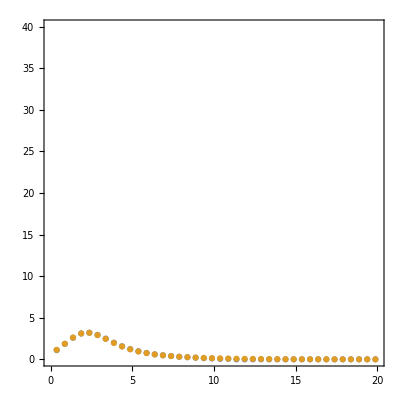

```mathematica
ListPlot[{data,dataT},Frame->True,PlotRange->{{0,20},{0,40}},AspectRatio->1]
```

### General Probability ratio

```mathematica
ratioGen[S23_,δ_,epS_,ee_]=(ee (-537.0144158815365 s23^2+(95.922402136029-4.114998188599089 ee) ee s23^2+(537.0144158815365+ee (-95.92240213602899+4.114998188599089 ee)) s23^4+epS^2 (-194626.6461383849+(34963.71557858255-1499.9168397443682 ee) ee+382355.29126830207 s23^2+ee (-69927.4311571651+2999.8336794887364 ee) s23^2+(-391483.50917764+(69927.4311571651-2999.8336794887364 ee) ee) s23^4)+epS s23 √(1-s23^2) (14161.307084011187-28998.778457602955 s23^2+ee (-2589.904857672781+5179.809715345562 s23^2+ee (111.1049510921754-222.2099021843508 s23^2))))-2536.820066237314 epS s23 √(1-s23^2) Sin[8.323065282815573/ee]+1119.5858672098655 ee epS s23 √(1-s23^2) Sin[8.323065282815573/ee]-39.38853098975155 ee^2 epS s23 √(1-s23^2) Sin[8.323065282815573/ee]+5073.640132474628 epS s23^3 √(1-s23^2) Sin[8.323065282815573/ee]-1796.3230913768598 ee epS s23^3 √(1-s23^2) Sin[8.323065282815573/ee]+78.7770619795031 ee^2 epS s23^3 √(1-s23^2) Sin[8.323065282815573/ee]+Cos[δ] (s23 (epS s23 (261.20978051393564-348.27970735191445 s23^2)+4701.776049250849 epS^2 s23^2 √(1-s23^2)-6.44962421022064 √(1-s23^2) (-0.5+1. s23^2))+ee s23 (-403.4052420503069 epS^2 s23^2 √(1-s23^2)+0.5533679589167451 √(1-s23^2) (-0.4999999999999999+1. s23^2)+epS s23 (-22.411402336128184+29.881869781504182 s23^2))+ee^3 (-0.03334587340666304 √(1-s23^2) (-0.5 s23+1. s23^3)+24.30914171345736 epS^2 √(1-s23^2) (-0.5 s23+1. s23^3)+epS (-0.22508464549497562+1.8006771639598036 s23^2-1.800677163959804 s23^4))+ee^2 (0.38865342484877047 √(1-s23^2) (-0.5 s23+1. s23^3)-283.3283467147537 epS^2 √(1-s23^2) (-0.5 s23+1. s23^3)+epS (2.623410617729201-20.987284941833607 s23^2+20.987284941833604 s23^4))+s23 (epS^2 √(1-s23^2) (-12603.870244016523+1081.3929190371105 ee+12603.870244016523 s23^2-1081.3929190371105 ee s23^2)+√(1-s23^2) (8.644629796993499-0.7416961035919825 ee-17.289259593986998 s23^2+1.483392207183965 ee s23^2)+epS s23 (1167.0250225941222-100.12897398491762 ee-933.6200180752978 s23^2+80.1031791879341 ee s23^2)) Sin[8.323065282815573/ee])-8.644629796993499 s23 √(1-s23^2) Sin[δ]+0.7416961035919825 ee s23 √(1-s23^2) Sin[δ]+3.2248121051103213 s23 √(1-s23^2) Sin[8.323065282815573/ee] Sin[δ]-0.2766839794583725 ee s23 √(1-s23^2) Sin[8.323065282815573/ee] Sin[δ]+Sin[8.323065282815573/ee] (-5978.45668107876 ee epS^2+(93.95629874953016-68494.14178840749 epS^2+ee (-33.26524243290481+1.4588344811019092 ee+30228.81841466637 epS^2-1063.4903367232919 ee epS^2)) s23^2+(-93.95629874953016+68494.14178840749 epS^2+ee (33.26524243290481-1.4588344811019092 ee-24250.361733587608 epS^2+1063.4903367232919 ee epS^2)) s23^4+(87.06992683797868-7.470467445376055 ee) epS s23^2 Sin[δ])+Cos[8.323065282815573/ee] (ee ((537.0144158815365+ee (-95.92240213602898+4.114998188599088 ee)) s23^2+(-537.0144158815365+(95.92240213602898-4.114998188599088 ee) ee) s23^4+epS^2 (-6898.001008467854+(-384585.5081691722+(69927.43115716509-2999.8336794887364 ee) ee) s23^2+(391483.50917764+ee (-69927.4311571651+2999.8336794887364 ee)) s23^4)+epS s23 √(1-s23^2) (-14243.90770996934+28998.778457602955 s23^2+ee (2589.904857672781-5179.809715345562 s23^2+ee (-111.1049510921754+222.2099021843508 s23^2))))+s23 (epS s23 (-435.3496341898932+ee (37.352337226880266+(20.987284941833604-1.8006771639598043 ee) ee)+(348.2797073519141+ee (-29.881869781504264+ee (-20.987284941833607+1.800677163959804 ee))) s23^2)+epS^2 √(1-s23^2) (4701.776049250852-4701.776049250846 s23^2+ee (-403.4052420503069+403.4052420503069 s23^2+ee (-141.66417335737682+12.15457085672868 ee+283.3283467147537 s23^2-24.30914171345736 ee s23^2)))+√(1-s23^2) (-3.224812105110321+6.449624210220642 s23^2+ee (0.27668397945837264-0.553367958916745 s23^2+ee (0.19432671242438523-0.01667293670333152 ee-0.38865342484877047 s23^2+0.03334587340666304 ee s23^2)))) Cos[δ]+s23 ((233.40500451882428-20.025794796983522 ee) epS s23-0.7416961035919825 (-11.65521802680122+1. ee) √(1-s23^2)) Sin[δ])+epS ((87.06992683797863+ee (-7.4704674453760544+(-2.623410617729201+0.22508464549497553 ee) ee)) Cos[8.323065282815573/ee+δ]+2.842170943040401*^-14 Sin[8.323065282815573/ee-δ]+(-233.40500451882443+20.025794796983533 ee) s23^2 Sin[δ]+(-233.40500451882437+20.025794796983526 ee) Sin[8.323065282815573/ee+δ]))/(2.7607421580402205+ee (-130.8796094130282+(23.3230292223281-1. ee) ee)+(-2.76074215804022+ee (130.87960941302822+ee (-23.323029222328106+1. ee))) Cos[8.323065282815573/ee]+(22.46560935192947+(-8.05902865451455+0.3548994794121858 ee) ee) Sin[8.323065282815573/ee])/.s23->Sqrt[S23];
```

### Creating data with s23 and δ

```mathematica
(* Subscript[dN, nsi]/Subscript[dE, rec]=∫Subscript[dN, nsi]/Subscript[dE, true] P(Subscript[E, rec],Subscript[E, true])ⅆ Subscript[E, true] =∫(Subscript[P, NSI](μ->τ))/Subscript[P, SM(μ->τ)] Subscript[dN, sm]/Subscript[dE, true] P(Subscript[E, rec],Subscript[E, true])ⅆ Subscript[E, true] *)
```

```mathematica
(* best-fit used {S23,δ} = {0.582,-2.5} *)
```

```mathematica
passos23=.4/10;
passodelta=2./10;
dataGen={};ls23d={};
Clear[delta,ss23];
Do[ss23=(0.582)-.2+passos23*i;
Do[delta=Pi*(-1.+passodelta*k);AppendTo[ls23d,{ss23,delta}];
AppendTo[dataGen,Table[{data2[[j,1]],fac2*Sum[fn[data2[[j,1]],data2[[i,1]]]*0.5*data2[[i,2]]*ratioGen[ss23,delta,0,.5*i],{i,40}]},{j,40}]],{k,0,10}],{i,0,10}]//Quiet;
```

```mathematica
Plot[ratioGen[(0.582),del,0,2],{del,-2*Pi,2*Pi}]
```

-Graphics-

```mathematica
dataGen//Dimensions
```

{121,40,2}

92

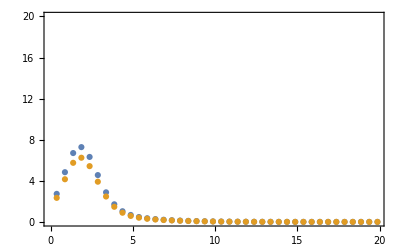

```mathematica
xx=RandomInteger[{1,Length@ls23d}]
ListPlot[{dataT,dataGen[[xx]]},PlotRange->{All,range},Frame->True]
```

### Data High

```mathematica
(* OS: Win, Linux *)
OS="Linux";
```

```mathematica
(* ModeHE, ModeAntiNu, ModeNu *)
(* Tau_minus, Tau_plus *)
```

```mathematica
mode="HE";sign="minus";
If[mode=="Nu",range=40,range=20];
```

```mathematica
(* Linux *)
```

```mathematica
If[OS=="Linux",data=Import[StringJoin["/home/adriano/Dropbox/Neutrinos/Tau/Data/Mat_WS_In_Mode",mode,"_Tau_",sign,".txt"],"Table"];
data=Table[{.5*i-.25/2,data[[i,2]]},{i,40}];
data2=Import[StringJoin["/home/adriano/Dropbox/Neutrinos/Tau/Data/Mat_WoutS_In_Mode",mode,"_Tau_",sign,".txt"],"Table"];
data2=Table[{.5*i-.25/2,data2[[i,2]]},{i,40}],data=Import[StringJoin["C:\\Users\\Orlando\\Dropbox\\Neutrinos\\Tau\\Data\\Mat_WS_In_Mode",mode,"_Tau_",sign,".txt"],"Table"];
data=Table[{.5*i-.25/2,data[[i,2]]},{i,40}];
data2=Import[StringJoin["C:\\Users\\Orlando\\Dropbox\\Neutrinos\\Tau\\Data\\Mat_WoutS_In_Mode",mode,"_Tau_",sign,".txt"],"Table"];
data2=Table[{.5*i-.25/2,data2[[i,2]]},{i,40}]];
```

### Data of Fig 1 by reconstructed energy

```mathematica
Clear[fs,fn]
fs[Ere_,Etrue_]:=If[Etrue<3.1,0,(*1/(Sqrt[2Pi]σe)*)(Exp[-1/2((Ere-x)/σe)^2]/.{x->b*Etrue,σe->r*Etrue}/.Thread[{b,r}->{.45,.25}])]
fn[Ere_,Etrue_]:=If[Etrue<3.1,0,fs[Ere,Etrue]/NIntegrate[fs[ere,Etrue],{ere,0,20}]]
```

```mathematica
(* dN/Subscript[dE, rec]=∫dN/Subscript[dE, true] P(Subscript[E, rec],Subscript[E, true])ⅆ Subscript[E, true] *)
(* doing numerical integration by cutting the integrand *)
dataT=Table[{data2[[j,1]],Sum[fn[data2[[j,1]],data2[[i,1]]]*0.5*data2[[i,2]],{i,40}]},{j,40}];
(*dataT=Table[{.5*j-.25,Sum[fn[0.5*j-.25,.5*i-.25]*0.5*data2[[i,2]],{i,40}]},{j,40}]//Quiet;*)
dtrue=Interpolation@data2;
ndtrue=NIntegrate[dtrue[x],{x,Min@data[[All,1]],Max@data[[All,1]]}]
dre=Interpolation@data;
ndre=NIntegrate[dre[x],{x,Min@data[[All,1]],Max@data[[All,1]]}]
dreInt=Interpolation@dataT;
ndreInt=NIntegrate[dreInt[x],{x,Min@data[[All,1]],Max@data[[All,1]]}]
fac2=ndtrue/ndreInt
(*dataT=Table[{.5*j-.25,fac2*Sum[fn[0.5*j-.25,.5*i]*0.5*data2[[i,2]],{i,40}]},{j,40}]//Quiet;*)
dataT=Table[{data2[[j,1]],fac2*Sum[fn[data2[[j,1]],data2[[i,1]]]*0.5*data2[[i,2]],{i,40}]},{j,40}];
```

77.45

76.1852

75.6044

1.02441

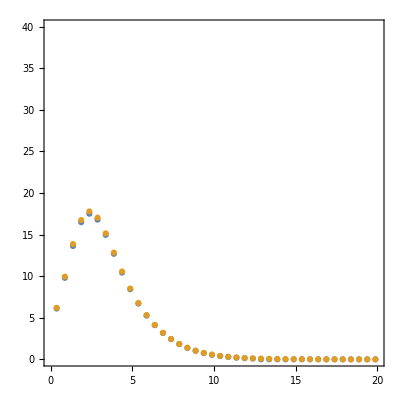

```mathematica
ListPlot[{data,dataT},Frame->True,PlotRange->{{0,20},{0,40}},AspectRatio->1]
```

### General Probability ratio

```mathematica
ratioGen[S23_,δ_,epS_,ee_]=(ee (-537.0144158815365 s23^2+(95.922402136029-4.114998188599089 ee) ee s23^2+(537.0144158815365+ee (-95.92240213602899+4.114998188599089 ee)) s23^4+epS^2 (-194626.6461383849+(34963.71557858255-1499.9168397443682 ee) ee+382355.29126830207 s23^2+ee (-69927.4311571651+2999.8336794887364 ee) s23^2+(-391483.50917764+(69927.4311571651-2999.8336794887364 ee) ee) s23^4)+epS s23 √(1-s23^2) (14161.307084011187-28998.778457602955 s23^2+ee (-2589.904857672781+5179.809715345562 s23^2+ee (111.1049510921754-222.2099021843508 s23^2))))-2536.820066237314 epS s23 √(1-s23^2) Sin[8.323065282815573/ee]+1119.5858672098655 ee epS s23 √(1-s23^2) Sin[8.323065282815573/ee]-39.38853098975155 ee^2 epS s23 √(1-s23^2) Sin[8.323065282815573/ee]+5073.640132474628 epS s23^3 √(1-s23^2) Sin[8.323065282815573/ee]-1796.3230913768598 ee epS s23^3 √(1-s23^2) Sin[8.323065282815573/ee]+78.7770619795031 ee^2 epS s23^3 √(1-s23^2) Sin[8.323065282815573/ee]+Cos[δ] (s23 (epS s23 (261.20978051393564-348.27970735191445 s23^2)+4701.776049250849 epS^2 s23^2 √(1-s23^2)-6.44962421022064 √(1-s23^2) (-0.5+1. s23^2))+ee s23 (-403.4052420503069 epS^2 s23^2 √(1-s23^2)+0.5533679589167451 √(1-s23^2) (-0.4999999999999999+1. s23^2)+epS s23 (-22.411402336128184+29.881869781504182 s23^2))+ee^3 (-0.03334587340666304 √(1-s23^2) (-0.5 s23+1. s23^3)+24.30914171345736 epS^2 √(1-s23^2) (-0.5 s23+1. s23^3)+epS (-0.22508464549497562+1.8006771639598036 s23^2-1.800677163959804 s23^4))+ee^2 (0.38865342484877047 √(1-s23^2) (-0.5 s23+1. s23^3)-283.3283467147537 epS^2 √(1-s23^2) (-0.5 s23+1. s23^3)+epS (2.623410617729201-20.987284941833607 s23^2+20.987284941833604 s23^4))+s23 (epS^2 √(1-s23^2) (-12603.870244016523+1081.3929190371105 ee+12603.870244016523 s23^2-1081.3929190371105 ee s23^2)+√(1-s23^2) (8.644629796993499-0.7416961035919825 ee-17.289259593986998 s23^2+1.483392207183965 ee s23^2)+epS s23 (1167.0250225941222-100.12897398491762 ee-933.6200180752978 s23^2+80.1031791879341 ee s23^2)) Sin[8.323065282815573/ee])-8.644629796993499 s23 √(1-s23^2) Sin[δ]+0.7416961035919825 ee s23 √(1-s23^2) Sin[δ]+3.2248121051103213 s23 √(1-s23^2) Sin[8.323065282815573/ee] Sin[δ]-0.2766839794583725 ee s23 √(1-s23^2) Sin[8.323065282815573/ee] Sin[δ]+Sin[8.323065282815573/ee] (-5978.45668107876 ee epS^2+(93.95629874953016-68494.14178840749 epS^2+ee (-33.26524243290481+1.4588344811019092 ee+30228.81841466637 epS^2-1063.4903367232919 ee epS^2)) s23^2+(-93.95629874953016+68494.14178840749 epS^2+ee (33.26524243290481-1.4588344811019092 ee-24250.361733587608 epS^2+1063.4903367232919 ee epS^2)) s23^4+(87.06992683797868-7.470467445376055 ee) epS s23^2 Sin[δ])+Cos[8.323065282815573/ee] (ee ((537.0144158815365+ee (-95.92240213602898+4.114998188599088 ee)) s23^2+(-537.0144158815365+(95.92240213602898-4.114998188599088 ee) ee) s23^4+epS^2 (-6898.001008467854+(-384585.5081691722+(69927.43115716509-2999.8336794887364 ee) ee) s23^2+(391483.50917764+ee (-69927.4311571651+2999.8336794887364 ee)) s23^4)+epS s23 √(1-s23^2) (-14243.90770996934+28998.778457602955 s23^2+ee (2589.904857672781-5179.809715345562 s23^2+ee (-111.1049510921754+222.2099021843508 s23^2))))+s23 (epS s23 (-435.3496341898932+ee (37.352337226880266+(20.987284941833604-1.8006771639598043 ee) ee)+(348.2797073519141+ee (-29.881869781504264+ee (-20.987284941833607+1.800677163959804 ee))) s23^2)+epS^2 √(1-s23^2) (4701.776049250852-4701.776049250846 s23^2+ee (-403.4052420503069+403.4052420503069 s23^2+ee (-141.66417335737682+12.15457085672868 ee+283.3283467147537 s23^2-24.30914171345736 ee s23^2)))+√(1-s23^2) (-3.224812105110321+6.449624210220642 s23^2+ee (0.27668397945837264-0.553367958916745 s23^2+ee (0.19432671242438523-0.01667293670333152 ee-0.38865342484877047 s23^2+0.03334587340666304 ee s23^2)))) Cos[δ]+s23 ((233.40500451882428-20.025794796983522 ee) epS s23-0.7416961035919825 (-11.65521802680122+1. ee) √(1-s23^2)) Sin[δ])+epS ((87.06992683797863+ee (-7.4704674453760544+(-2.623410617729201+0.22508464549497553 ee) ee)) Cos[8.323065282815573/ee+δ]+2.842170943040401*^-14 Sin[8.323065282815573/ee-δ]+(-233.40500451882443+20.025794796983533 ee) s23^2 Sin[δ]+(-233.40500451882437+20.025794796983526 ee) Sin[8.323065282815573/ee+δ]))/(2.7607421580402205+ee (-130.8796094130282+(23.3230292223281-1. ee) ee)+(-2.76074215804022+ee (130.87960941302822+ee (-23.323029222328106+1. ee))) Cos[8.323065282815573/ee]+(22.46560935192947+(-8.05902865451455+0.3548994794121858 ee) ee) Sin[8.323065282815573/ee])/.s23->Sqrt[S23];
```

### Creating data with s23 and δ

```mathematica
(* Subscript[dN, nsi]/Subscript[dE, rec]=∫Subscript[dN, nsi]/Subscript[dE, true] P(Subscript[E, rec],Subscript[E, true])ⅆ Subscript[E, true] =∫(Subscript[P, NSI](μ->τ))/Subscript[P, SM(μ->τ)] Subscript[dN, sm]/Subscript[dE, true] P(Subscript[E, rec],Subscript[E, true])ⅆ Subscript[E, true] *)
```

```mathematica
(* best-fit used {S23,δ} = {0.582,-2.5} *)
```

```mathematica
passos23=.4/10;
passodelta=2./10;
dataGen={};ls23d={};
Clear[delta,ss23];
Do[ss23=(0.582)-.2+passos23*i;
Do[delta=Pi*(-1.+passodelta*k);AppendTo[ls23d,{ss23,delta}];
AppendTo[dataGen,Table[{data2[[j,1]],fac2*Sum[fn[data2[[j,1]],data2[[i,1]]]*0.5*data2[[i,2]]*ratioGen[ss23,delta,0,.5*i],{i,40}]},{j,40}]],{k,0,10}],{i,0,10}]//Quiet;
```

```mathematica
Plot[ratioGen[(0.582),del,0,2],{del,-2*Pi,2*Pi}]
```

-Graphics-

```mathematica
dataGen//Dimensions
```

{121,40,2}

85

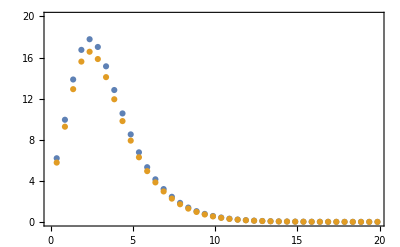

```mathematica
xx=RandomInteger[{1,Length@ls23d}]
ListPlot[{dataT,dataGen[[xx]]},PlotRange->{All,range},Frame->True]
```

### Chi square

```mathematica
(* χ^2 = 2 Sum[ndata - ntrue + ntrue*Log(ntrue/ndata),{i,bin}] *)
```

```mathematica
chis23d=Table[Sum[dataGen[[j,i,2]]-dataT[[i,2]]+dataT[[i,2]]*Log[dataT[[i,2]]/dataGen[[j,i,2]]],{i,40}],{j,Length@dataGen}]//Chop
```

{0.0420292,0.0573772,0.0719694,0.0784319,0.0730937,0.0590644,0.0435542,0.0325554,0.0284762,0.0316937,0.0420292,0.00608709,0.00199269,0.000386975,0.000146651,0.000594144,0.00282837,0.0075367,0.0126028,0.0143678,0.0114022,0.00608709,0.0574899,0.0431901,0.0345179,0.0331331,0.0391966,0.0518222,0.0674257,0.0793865,0.0815003,0.0725985,0.0574899,0.0813286,0.0647588,0.0555319,0.0556253,0.0650224,0.0816927,0.100201,0.112502,0.11237,0.0998752,0.0813286,0.0464273,0.0345649,0.0289949,0.0304298,0.0387284,0.0523833,0.0667885,0.0751677,0.0729261,0.0613197,0.0464273,0.000866511,2.20338×10^-7,0.000158924,0.0000301403,0.000474013,0.00306487,0.00707227,0.00939573,0.00791739,0.00399815,0.000866511,0.0781431,0.0941104,0.0999529,0.092391,0.0755613,0.0576978,0.0454874,0.0417207,0.0468085,0.0600335,0.0781431,0.515763,0.55419,0.563437,0.539181,0.492429,0.442886,0.408878,0.401195,0.421999,0.465053,0.515763,1.69215,1.75874,1.76658,1.71221,1.61873,1.52371,1.46229,1.45536,1.50512,1.59485,1.69215,4.19535,4.29628,4.29478,4.19142,4.02871,3.87066,3.77578,3.77731,3.87465,4.0336,4.19535,8.95409,9.09667,9.07375,8.89467,8.6318,8.38739,8.25197,8.27373,8.44493,8.70408,8.95409}

```mathematica
dataSet3=chis23d;
```

### Data

```mathematica
ls23d
```

{{0.382,-3.14159},{0.382,-2.51327},{0.382,-1.88496},{0.382,-1.25664},{0.382,-0.628319},{0.382,0.},{0.382,0.628319},{0.382,1.25664},{0.382,1.88496},{0.382,2.51327},{0.382,3.14159},{0.422,-3.14159},{0.422,-2.51327},{0.422,-1.88496},{0.422,-1.25664},{0.422,-0.628319},{0.422,0.},{0.422,0.628319},{0.422,1.25664},{0.422,1.88496},{0.422,2.51327},{0.422,3.14159},{0.462,-3.14159},{0.462,-2.51327},{0.462,-1.88496},{0.462,-1.25664},{0.462,-0.628319},{0.462,0.},{0.462,0.628319},{0.462,1.25664},{0.462,1.88496},{0.462,2.51327},{0.462,3.14159},{0.502,-3.14159},{0.502,-2.51327},{0.502,-1.88496},{0.502,-1.25664},{0.502,-0.628319},{0.502,0.},{0.502,0.628319},{0.502,1.25664},{0.502,1.88496},{0.502,2.51327},{0.502,3.14159},{0.542,-3.14159},{0.542,-2.51327},{0.542,-1.88496},{0.542,-1.25664},{0.542,-0.628319},{0.542,0.},{0.542,0.628319},{0.542,1.25664},{0.542,1.88496},{0.542,2.51327},{0.542,3.14159},{0.582,-3.14159},{0.582,-2.51327},{0.582,-1.88496},{0.582,-1.25664},{0.582,-0.628319},{0.582,0.},{0.582,0.628319},{0.582,1.25664},{0.582,1.88496},{0.582,2.51327},{0.582,3.14159},{0.622,-3.14159},{0.622,-2.51327},{0.622,-1.88496},{0.622,-1.25664},{0.622,-0.628319},{0.622,0.},{0.622,0.628319},{0.622,1.25664},{0.622,1.88496},{0.622,2.51327},{0.622,3.14159},{0.662,-3.14159},{0.662,-2.51327},{0.662,-1.88496},{0.662,-1.25664},{0.662,-0.628319},{0.662,0.},{0.662,0.628319},{0.662,1.25664},{0.662,1.88496},{0.662,2.51327},{0.662,3.14159},{0.702,-3.14159},{0.702,-2.51327},{0.702,-1.88496},{0.702,-1.25664},{0.702,-0.628319},{0.702,0.},{0.702,0.628319},{0.702,1.25664},{0.702,1.88496},{0.702,2.51327},{0.702,3.14159},{0.742,-3.14159},{0.742,-2.51327},{0.742,-1.88496},{0.742,-1.25664},{0.742,-0.628319},{0.742,0.},{0.742,0.628319},{0.742,1.25664},{0.742,1.88496},{0.742,2.51327},{0.742,3.14159},{0.782,-3.14159},{0.782,-2.51327},{0.782,-1.88496},{0.782,-1.25664},{0.782,-0.628319},{0.782,0.},{0.782,0.628319},{0.782,1.25664},{0.782,1.88496},{0.782,2.51327},{0.782,3.14159}}

```mathematica
dataSet1
```

{0.0269286,0.0414439,0.0546922,0.0590627,0.0517798,0.0375102,0.023947,0.0157719,0.0135848,0.0171438,0.0269286,0.0056676,0.00133194,0.000107268,0.0000329362,0.000429671,0.0031485,0.00906881,0.0151177,0.0165889,0.0122312,0.0056676,0.0449538,0.0304462,0.0223745,0.0215057,0.0278334,0.0410531,0.057733,0.0704003,0.0719369,0.0614263,0.0449538,0.0628698,0.0458753,0.0367736,0.0368328,0.0460479,0.0631183,0.0828531,0.0963322,0.0962381,0.0826239,0.0628698,0.0370159,0.0245518,0.018702,0.0195993,0.0272754,0.0411252,0.0569,0.0669108,0.0652744,0.0529805,0.0370159,0.00131191,3.64809×10^-7,0.000313918,0.000141566,0.000295057,0.00315588,0.00837354,0.0119981,0.0106981,0.00569659,0.00131191,0.0503586,0.0666857,0.0747837,0.0696868,0.0544903,0.0375623,0.0257877,0.0213887,0.024219,0.0343157,0.0503586,0.352629,0.393232,0.409448,0.393344,0.352673,0.305674,0.270355,0.25757,0.270512,0.305796,0.352629,1.17667,1.2487,1.272,1.23608,1.15679,1.0673,1.0014,0.981226,1.01293,1.08649,1.17667,2.93985,3.05155,3.07931,3.01116,2.87591,2.7283,2.62382,2.59879,2.66142,2.79052,2.93985,6.30146,6.46301,6.49067,6.37271,6.15787,5.93154,5.77859,5.75318,5.86391,6.07205,6.30146}

```mathematica
dataSet2
```

{0.00955227,0.0151173,0.0201663,0.0217431,0.0188223,0.0132932,0.00815678,0.00515131,0.00440894,0.00580177,0.00955227,0.00216988,0.000479221,0.0000261919,6.42941×10^-6,0.000156884,0.00123485,0.0035913,0.00598536,0.00653895,0.00477735,0.00216988,0.0166804,0.0110593,0.0079711,0.00766309,0.0101235,0.0152672,0.0217762,0.0267139,0.0272771,0.0231249,0.0166804,0.0232723,0.0166782,0.0131663,0.0131873,0.01674,0.0233622,0.0310603,0.0363371,0.0363028,0.0309769,0.0232723,0.0137825,0.00893046,0.00665395,0.00697184,0.00990586,0.015272,0.021447,0.0254073,0.024807,0.0200147,0.0137825,0.000531912,1.49034×10^-7,0.000129918,0.0000609186,0.000104732,0.00122679,0.00331186,0.00478509,0.00429141,0.00229689,0.000531912,0.017911,0.024242,0.0274947,0.0256572,0.0198707,0.0133784,0.00885252,0.00711922,0.00809046,0.0118224,0.017911,0.127176,0.14299,0.149636,0.14385,0.128455,0.110425,0.0967018,0.0914851,0.0960625,0.109281,0.127176,0.425975,0.454119,0.46396,0.451067,0.421182,0.386883,0.361171,0.352656,0.363938,0.391501,0.425975,1.06608,1.10985,1.12216,1.09771,1.04691,0.99041,0.949501,0.93839,0.96073,1.00903,1.06608,2.28724,2.35073,2.36415,2.32185,2.24138,2.15486,2.09479,2.08241,2.12196,2.19967,2.28724}

```mathematica
dataSet3
```

{0.0420292,0.0573772,0.0719694,0.0784319,0.0730937,0.0590644,0.0435542,0.0325554,0.0284762,0.0316937,0.0420292,0.00608709,0.00199269,0.000386975,0.000146651,0.000594144,0.00282837,0.0075367,0.0126028,0.0143678,0.0114022,0.00608709,0.0574899,0.0431901,0.0345179,0.0331331,0.0391966,0.0518222,0.0674257,0.0793865,0.0815003,0.0725985,0.0574899,0.0813286,0.0647588,0.0555319,0.0556253,0.0650224,0.0816927,0.100201,0.112502,0.11237,0.0998752,0.0813286,0.0464273,0.0345649,0.0289949,0.0304298,0.0387284,0.0523833,0.0667885,0.0751677,0.0729261,0.0613197,0.0464273,0.000866511,2.20338×10^-7,0.000158924,0.0000301403,0.000474013,0.00306487,0.00707227,0.00939573,0.00791739,0.00399815,0.000866511,0.0781431,0.0941104,0.0999529,0.092391,0.0755613,0.0576978,0.0454874,0.0417207,0.0468085,0.0600335,0.0781431,0.515763,0.55419,0.563437,0.539181,0.492429,0.442886,0.408878,0.401195,0.421999,0.465053,0.515763,1.69215,1.75874,1.76658,1.71221,1.61873,1.52371,1.46229,1.45536,1.50512,1.59485,1.69215,4.19535,4.29628,4.29478,4.19142,4.02871,3.87066,3.77578,3.77731,3.87465,4.0336,4.19535,8.95409,9.09667,9.07375,8.89467,8.6318,8.38739,8.25197,8.27373,8.44493,8.70408,8.95409}

### Contour

```mathematica
dataSet1;
```

```mathematica
dataSet2;
```

```mathematica
dataSet=dataSet1+dataSet2+dataSet3;
```

InterpolatingFunction[…]

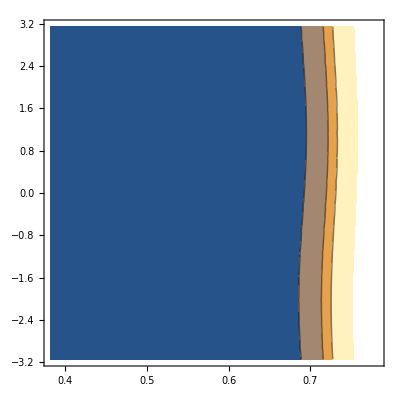

```mathematica
Table[{ls23d[[i]],{dataSet[[i]]}},{i,Length@ls23d}];
func=Interpolation@%
ContourPlot[func[s23,del],{s23,Min@ls23d[[All,1]],Max@ls23d[[All,1]]},{del,Min@ls23d[[All,2]],Max@ls23d[[All,2]]},Contours->{2.3,4.6,6.}]
```

## All data sets - s23 and NSI

### Data Nu

```mathematica
(* OS: Win, Linux *)
OS="Linux";
```

```mathematica
(* ModeHE, ModeAntiNu, ModeNu *)
(* Tau_minus, Tau_plus *)
```

```mathematica
mode="Nu";sign="minus";
If[mode=="Nu",range=40,range=20];
```

```mathematica
(* Linux *)
```

```mathematica
If[OS=="Linux",data=Import[StringJoin["/home/adriano/Dropbox/Neutrinos/Tau/Data/Mat_WS_In_Mode",mode,"_Tau_",sign,".txt"],"Table"];
data=Table[{.5*i-.25/2,data[[i,2]]},{i,40}];
data2=Import[StringJoin["/home/adriano/Dropbox/Neutrinos/Tau/Data/Mat_WoutS_In_Mode",mode,"_Tau_",sign,".txt"],"Table"];
data2=Table[{.5*i-.25/2,data2[[i,2]]},{i,40}],data=Import[StringJoin["C:\\Users\\Orlando\\Dropbox\\Neutrinos\\Tau\\Data\\Mat_WS_In_Mode",mode,"_Tau_",sign,".txt"],"Table"];
data=Table[{.5*i-.25/2,data[[i,2]]},{i,40}];
data2=Import[StringJoin["C:\\Users\\Orlando\\Dropbox\\Neutrinos\\Tau\\Data\\Mat_WoutS_In_Mode",mode,"_Tau_",sign,".txt"],"Table"];
data2=Table[{.5*i-.25/2,data2[[i,2]]},{i,40}]];
```

### Data of Fig 1 by reconstructed energy

```mathematica
Clear[fs,fn]
fs[Ere_,Etrue_]:=If[Etrue<3.1,0,(*1/(Sqrt[2Pi]σe)*)(Exp[-1/2((Ere-x)/σe)^2]/.{x->b*Etrue,σe->r*Etrue}/.Thread[{b,r}->{.45,.25}])]
fn[Ere_,Etrue_]:=If[Etrue<3.1,0,fs[Ere,Etrue]/NIntegrate[fs[ere,Etrue],{ere,0,20}]]
```

```mathematica
(* dN/Subscript[dE, rec]=∫dN/Subscript[dE, true] P(Subscript[E, rec],Subscript[E, true])ⅆ Subscript[E, true] *)
(* doing numerical integration by cutting the integrand *)
dataT=Table[{data2[[j,1]],Sum[fn[data2[[j,1]],data2[[i,1]]]*0.5*data2[[i,2]],{i,40}]},{j,40}];
(*dataT=Table[{.5*j-.25,Sum[fn[0.5*j-.25,.5*i-.25]*0.5*data2[[i,2]],{i,40}]},{j,40}]//Quiet;*)
dtrue=Interpolation@data2;
ndtrue=NIntegrate[dtrue[x],{x,Min@data[[All,1]],Max@data[[All,1]]}]
dre=Interpolation@data;
ndre=NIntegrate[dre[x],{x,Min@data[[All,1]],Max@data[[All,1]]}]
dreInt=Interpolation@dataT;
ndreInt=NIntegrate[dreInt[x],{x,Min@data[[All,1]],Max@data[[All,1]]}]
fac2=ndtrue/ndreInt
(*dataT=Table[{.5*j-.25,fac2*Sum[fn[0.5*j-.25,.5*i]*0.5*data2[[i,2]],{i,40}]},{j,40}]//Quiet;*)
dataT=Table[{data2[[j,1]],fac2*Sum[fn[data2[[j,1]],data2[[i,1]]]*0.5*data2[[i,2]],{i,40}]},{j,40}];
```

54.4842

53.3873

52.517

1.03746

```mathematica
ListPlot[{data,dataT},Frame->True,PlotRange->{{0,20},{0,40}},AspectRatio->1]
```

-Graphics-

### General Probability ratio

```mathematica
ratioGen[S23_,δ_,epS_,ee_]=(ee (-537.0144158815365 s23^2+(95.922402136029-4.114998188599089 ee) ee s23^2+(537.0144158815365+ee (-95.92240213602899+4.114998188599089 ee)) s23^4+epS^2 (-194626.6461383849+(34963.71557858255-1499.9168397443682 ee) ee+382355.29126830207 s23^2+ee (-69927.4311571651+2999.8336794887364 ee) s23^2+(-391483.50917764+(69927.4311571651-2999.8336794887364 ee) ee) s23^4)+epS s23 √(1-s23^2) (14161.307084011187-28998.778457602955 s23^2+ee (-2589.904857672781+5179.809715345562 s23^2+ee (111.1049510921754-222.2099021843508 s23^2))))-2536.820066237314 epS s23 √(1-s23^2) Sin[8.323065282815573/ee]+1119.5858672098655 ee epS s23 √(1-s23^2) Sin[8.323065282815573/ee]-39.38853098975155 ee^2 epS s23 √(1-s23^2) Sin[8.323065282815573/ee]+5073.640132474628 epS s23^3 √(1-s23^2) Sin[8.323065282815573/ee]-1796.3230913768598 ee epS s23^3 √(1-s23^2) Sin[8.323065282815573/ee]+78.7770619795031 ee^2 epS s23^3 √(1-s23^2) Sin[8.323065282815573/ee]+Cos[δ] (s23 (epS s23 (261.20978051393564-348.27970735191445 s23^2)+4701.776049250849 epS^2 s23^2 √(1-s23^2)-6.44962421022064 √(1-s23^2) (-0.5+1. s23^2))+ee s23 (-403.4052420503069 epS^2 s23^2 √(1-s23^2)+0.5533679589167451 √(1-s23^2) (-0.4999999999999999+1. s23^2)+epS s23 (-22.411402336128184+29.881869781504182 s23^2))+ee^3 (-0.03334587340666304 √(1-s23^2) (-0.5 s23+1. s23^3)+24.30914171345736 epS^2 √(1-s23^2) (-0.5 s23+1. s23^3)+epS (-0.22508464549497562+1.8006771639598036 s23^2-1.800677163959804 s23^4))+ee^2 (0.38865342484877047 √(1-s23^2) (-0.5 s23+1. s23^3)-283.3283467147537 epS^2 √(1-s23^2) (-0.5 s23+1. s23^3)+epS (2.623410617729201-20.987284941833607 s23^2+20.987284941833604 s23^4))+s23 (epS^2 √(1-s23^2) (-12603.870244016523+1081.3929190371105 ee+12603.870244016523 s23^2-1081.3929190371105 ee s23^2)+√(1-s23^2) (8.644629796993499-0.7416961035919825 ee-17.289259593986998 s23^2+1.483392207183965 ee s23^2)+epS s23 (1167.0250225941222-100.12897398491762 ee-933.6200180752978 s23^2+80.1031791879341 ee s23^2)) Sin[8.323065282815573/ee])-8.644629796993499 s23 √(1-s23^2) Sin[δ]+0.7416961035919825 ee s23 √(1-s23^2) Sin[δ]+3.2248121051103213 s23 √(1-s23^2) Sin[8.323065282815573/ee] Sin[δ]-0.2766839794583725 ee s23 √(1-s23^2) Sin[8.323065282815573/ee] Sin[δ]+Sin[8.323065282815573/ee] (-5978.45668107876 ee epS^2+(93.95629874953016-68494.14178840749 epS^2+ee (-33.26524243290481+1.4588344811019092 ee+30228.81841466637 epS^2-1063.4903367232919 ee epS^2)) s23^2+(-93.95629874953016+68494.14178840749 epS^2+ee (33.26524243290481-1.4588344811019092 ee-24250.361733587608 epS^2+1063.4903367232919 ee epS^2)) s23^4+(87.06992683797868-7.470467445376055 ee) epS s23^2 Sin[δ])+Cos[8.323065282815573/ee] (ee ((537.0144158815365+ee (-95.92240213602898+4.114998188599088 ee)) s23^2+(-537.0144158815365+(95.92240213602898-4.114998188599088 ee) ee) s23^4+epS^2 (-6898.001008467854+(-384585.5081691722+(69927.43115716509-2999.8336794887364 ee) ee) s23^2+(391483.50917764+ee (-69927.4311571651+2999.8336794887364 ee)) s23^4)+epS s23 √(1-s23^2) (-14243.90770996934+28998.778457602955 s23^2+ee (2589.904857672781-5179.809715345562 s23^2+ee (-111.1049510921754+222.2099021843508 s23^2))))+s23 (epS s23 (-435.3496341898932+ee (37.352337226880266+(20.987284941833604-1.8006771639598043 ee) ee)+(348.2797073519141+ee (-29.881869781504264+ee (-20.987284941833607+1.800677163959804 ee))) s23^2)+epS^2 √(1-s23^2) (4701.776049250852-4701.776049250846 s23^2+ee (-403.4052420503069+403.4052420503069 s23^2+ee (-141.66417335737682+12.15457085672868 ee+283.3283467147537 s23^2-24.30914171345736 ee s23^2)))+√(1-s23^2) (-3.224812105110321+6.449624210220642 s23^2+ee (0.27668397945837264-0.553367958916745 s23^2+ee (0.19432671242438523-0.01667293670333152 ee-0.38865342484877047 s23^2+0.03334587340666304 ee s23^2)))) Cos[δ]+s23 ((233.40500451882428-20.025794796983522 ee) epS s23-0.7416961035919825 (-11.65521802680122+1. ee) √(1-s23^2)) Sin[δ])+epS ((87.06992683797863+ee (-7.4704674453760544+(-2.623410617729201+0.22508464549497553 ee) ee)) Cos[8.323065282815573/ee+δ]+2.842170943040401*^-14 Sin[8.323065282815573/ee-δ]+(-233.40500451882443+20.025794796983533 ee) s23^2 Sin[δ]+(-233.40500451882437+20.025794796983526 ee) Sin[8.323065282815573/ee+δ]))/(2.7607421580402205+ee (-130.8796094130282+(23.3230292223281-1. ee) ee)+(-2.76074215804022+ee (130.87960941302822+ee (-23.323029222328106+1. ee))) Cos[8.323065282815573/ee]+(22.46560935192947+(-8.05902865451455+0.3548994794121858 ee) ee) Sin[8.323065282815573/ee])/.s23->Sqrt[S23];
```

### Creating data with s23 and NSI

```mathematica
(* Subscript[dN, nsi]/Subscript[dE, rec]=∫Subscript[dN, nsi]/Subscript[dE, true] P(Subscript[E, rec],Subscript[E, true])ⅆ Subscript[E, true] =∫(Subscript[P, NSI](μ->τ))/Subscript[P, SM(μ->τ)] Subscript[dN, sm]/Subscript[dE, true] P(Subscript[E, rec],Subscript[E, true])ⅆ Subscript[E, true] *)
```

```mathematica
(* best-fit used {S23,δ} = {0.582,-2.5} *)
```

```mathematica
passos23=.4/10;
passodelta=2./10;
dataGen={};ls23d={};
Clear[delta,ss23];
Do[ss23=(0.582)-.2+passos23*i;
Do[delta=(-1.+passodelta*k);AppendTo[ls23d,{ss23,delta}];
AppendTo[dataGen,Table[{data2[[j,1]],fac2*Sum[fn[data2[[j,1]],data2[[i,1]]]*0.5*data2[[i,2]]*ratioGen[ss23,-2.5,delta,.5*i],{i,40}]},{j,40}]],{k,0,10}],{i,0,10}]//Quiet;
```

```mathematica
Plot[ratioGen[(0.582),del,0,2],{del,-2*Pi,2*Pi}]
```

-Graphics-

```mathematica
dataGen//Dimensions
```

{121,40,2}

11

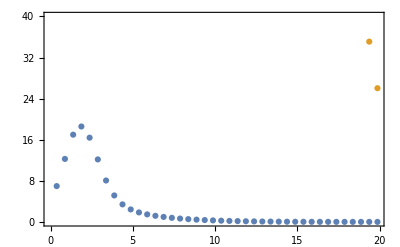

```mathematica
xx=RandomInteger[{1,Length@ls23d}]
ListPlot[{dataT,dataGen[[xx]]},PlotRange->{All,range},Frame->True]
```

### Chi square

```mathematica
(* χ^2 = 2 Sum[ndata - ntrue + ntrue*Log(ntrue/ndata),{i,bin}] *)
```

```mathematica
chis23d=Table[Sum[dataGen[[j,i,2]]-dataT[[i,2]]+dataT[[i,2]]*Log[dataT[[i,2]]/dataGen[[j,i,2]]],{i,40}],{j,Length@dataGen}]//Chop
```

{161975.,103633.,58225.4,25763.2,6281.58,0.0417651,5792.35,24764.2,56721.,101625.,159463.,159284.,101837.,57147.1,25224.8,6105.95,0.00127844,5801.76,24603.4,56211.2,100588.,157721.,157659.,100720.,56446.7,24850.7,5967.95,0.0302018,5855.3,24620.6,56100.1,100257.,157080.,157109.,100288.,56129.8,24644.6,5869.36,0.045592,5951.05,24811.6,56381.4,100624.,157529.,157642.,100550.,56201.8,24610.,5811.93,0.0243565,6087.22,25172.6,57049.1,101681.,159057.,159268.,101511.,56668.2,24750.8,5797.45,0,6262.,25699.6,58097.1,103419.,161655.,161996.,103181.,57534.8,25070.8,5827.83,0.0669707,6473.51,26388.7,59519.1,105830.,165310.,165837.,105566.,58807.9,25574.4,5905.17,0.393879,6719.75,27235.5,61308.7,108905.,170012.,170800.,108677.,60494.6,26266.2,6031.89,1.24978,6998.43,28235.3,63458.4,112633.,175749.,176901.,112523.,62603.,27152.,6210.84,3.05311,7306.86,29382.5,65959.6,117004.,182504.,184154.,117119.,65143.4,28238.4,6445.5,6.46513,7641.72,30670.2,68802.,122003.,190261.}

```mathematica
dataSet1=chis23d;
```

### Data AntiNu

```mathematica
(* OS: Win, Linux *)
OS="Linux";
```

```mathematica
(* ModeHE, ModeAntiNu, ModeNu *)
(* Tau_minus, Tau_plus *)
```

```mathematica
mode="AntiNu";sign="plus";
If[mode=="Nu",range=40,range=20];
```

```mathematica
(* Linux *)
```

```mathematica
If[OS=="Linux",data=Import[StringJoin["/home/adriano/Dropbox/Neutrinos/Tau/Data/Mat_WS_In_Mode",mode,"_Tau_",sign,".txt"],"Table"];
data=Table[{.5*i-.25/2,data[[i,2]]},{i,40}];
data2=Import[StringJoin["/home/adriano/Dropbox/Neutrinos/Tau/Data/Mat_WoutS_In_Mode",mode,"_Tau_",sign,".txt"],"Table"];
data2=Table[{.5*i-.25/2,data2[[i,2]]},{i,40}],data=Import[StringJoin["C:\\Users\\Orlando\\Dropbox\\Neutrinos\\Tau\\Data\\Mat_WS_In_Mode",mode,"_Tau_",sign,".txt"],"Table"];
data=Table[{.5*i-.25/2,data[[i,2]]},{i,40}];
data2=Import[StringJoin["C:\\Users\\Orlando\\Dropbox\\Neutrinos\\Tau\\Data\\Mat_WoutS_In_Mode",mode,"_Tau_",sign,".txt"],"Table"];
data2=Table[{.5*i-.25/2,data2[[i,2]]},{i,40}]];
```

### Data of Fig 1 by reconstructed energy

```mathematica
Clear[fs,fn]
fs[Ere_,Etrue_]:=If[Etrue<3.1,0,(*1/(Sqrt[2Pi]σe)*)(Exp[-1/2((Ere-x)/σe)^2]/.{x->b*Etrue,σe->r*Etrue}/.Thread[{b,r}->{.45,.25}])]
fn[Ere_,Etrue_]:=If[Etrue<3.1,0,fs[Ere,Etrue]/NIntegrate[fs[ere,Etrue],{ere,0,20}]]
```

```mathematica
(* dN/Subscript[dE, rec]=∫dN/Subscript[dE, true] P(Subscript[E, rec],Subscript[E, true])ⅆ Subscript[E, true] *)
(* doing numerical integration by cutting the integrand *)
dataT=Table[{data2[[j,1]],Sum[fn[data2[[j,1]],data2[[i,1]]]*0.5*data2[[i,2]],{i,40}]},{j,40}];
(*dataT=Table[{.5*j-.25,Sum[fn[0.5*j-.25,.5*i-.25]*0.5*data2[[i,2]],{i,40}]},{j,40}]//Quiet;*)
dtrue=Interpolation@data2;
ndtrue=NIntegrate[dtrue[x],{x,Min@data[[All,1]],Max@data[[All,1]]}]
dre=Interpolation@data;
ndre=NIntegrate[dre[x],{x,Min@data[[All,1]],Max@data[[All,1]]}]
dreInt=Interpolation@dataT;
ndreInt=NIntegrate[dreInt[x],{x,Min@data[[All,1]],Max@data[[All,1]]}]
fac2=ndtrue/ndreInt
(*dataT=Table[{.5*j-.25,fac2*Sum[fn[0.5*j-.25,.5*i]*0.5*data2[[i,2]],{i,40}]},{j,40}]//Quiet;*)
dataT=Table[{data2[[j,1]],fac2*Sum[fn[data2[[j,1]],data2[[i,1]]]*0.5*data2[[i,2]],{i,40}]},{j,40}];
```

19.775

19.4308

19.0148

1.03998

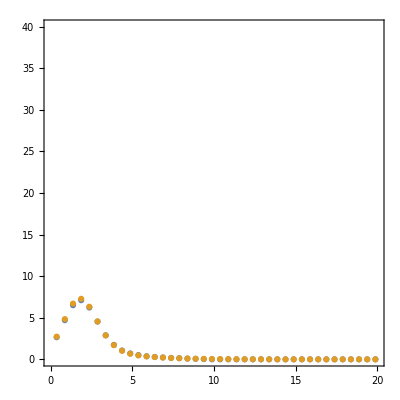

```mathematica
ListPlot[{data,dataT},Frame->True,PlotRange->{{0,20},{0,40}},AspectRatio->1]
```

### General Probability ratio

```mathematica
ratioGen[S23_,δ_,epS_,ee_]=(ee (-537.0144158815365 s23^2+(95.922402136029-4.114998188599089 ee) ee s23^2+(537.0144158815365+ee (-95.92240213602899+4.114998188599089 ee)) s23^4+epS^2 (-194626.6461383849+(34963.71557858255-1499.9168397443682 ee) ee+382355.29126830207 s23^2+ee (-69927.4311571651+2999.8336794887364 ee) s23^2+(-391483.50917764+(69927.4311571651-2999.8336794887364 ee) ee) s23^4)+epS s23 √(1-s23^2) (14161.307084011187-28998.778457602955 s23^2+ee (-2589.904857672781+5179.809715345562 s23^2+ee (111.1049510921754-222.2099021843508 s23^2))))-2536.820066237314 epS s23 √(1-s23^2) Sin[8.323065282815573/ee]+1119.5858672098655 ee epS s23 √(1-s23^2) Sin[8.323065282815573/ee]-39.38853098975155 ee^2 epS s23 √(1-s23^2) Sin[8.323065282815573/ee]+5073.640132474628 epS s23^3 √(1-s23^2) Sin[8.323065282815573/ee]-1796.3230913768598 ee epS s23^3 √(1-s23^2) Sin[8.323065282815573/ee]+78.7770619795031 ee^2 epS s23^3 √(1-s23^2) Sin[8.323065282815573/ee]+Cos[δ] (s23 (epS s23 (261.20978051393564-348.27970735191445 s23^2)+4701.776049250849 epS^2 s23^2 √(1-s23^2)-6.44962421022064 √(1-s23^2) (-0.5+1. s23^2))+ee s23 (-403.4052420503069 epS^2 s23^2 √(1-s23^2)+0.5533679589167451 √(1-s23^2) (-0.4999999999999999+1. s23^2)+epS s23 (-22.411402336128184+29.881869781504182 s23^2))+ee^3 (-0.03334587340666304 √(1-s23^2) (-0.5 s23+1. s23^3)+24.30914171345736 epS^2 √(1-s23^2) (-0.5 s23+1. s23^3)+epS (-0.22508464549497562+1.8006771639598036 s23^2-1.800677163959804 s23^4))+ee^2 (0.38865342484877047 √(1-s23^2) (-0.5 s23+1. s23^3)-283.3283467147537 epS^2 √(1-s23^2) (-0.5 s23+1. s23^3)+epS (2.623410617729201-20.987284941833607 s23^2+20.987284941833604 s23^4))+s23 (epS^2 √(1-s23^2) (-12603.870244016523+1081.3929190371105 ee+12603.870244016523 s23^2-1081.3929190371105 ee s23^2)+√(1-s23^2) (8.644629796993499-0.7416961035919825 ee-17.289259593986998 s23^2+1.483392207183965 ee s23^2)+epS s23 (1167.0250225941222-100.12897398491762 ee-933.6200180752978 s23^2+80.1031791879341 ee s23^2)) Sin[8.323065282815573/ee])-8.644629796993499 s23 √(1-s23^2) Sin[δ]+0.7416961035919825 ee s23 √(1-s23^2) Sin[δ]+3.2248121051103213 s23 √(1-s23^2) Sin[8.323065282815573/ee] Sin[δ]-0.2766839794583725 ee s23 √(1-s23^2) Sin[8.323065282815573/ee] Sin[δ]+Sin[8.323065282815573/ee] (-5978.45668107876 ee epS^2+(93.95629874953016-68494.14178840749 epS^2+ee (-33.26524243290481+1.4588344811019092 ee+30228.81841466637 epS^2-1063.4903367232919 ee epS^2)) s23^2+(-93.95629874953016+68494.14178840749 epS^2+ee (33.26524243290481-1.4588344811019092 ee-24250.361733587608 epS^2+1063.4903367232919 ee epS^2)) s23^4+(87.06992683797868-7.470467445376055 ee) epS s23^2 Sin[δ])+Cos[8.323065282815573/ee] (ee ((537.0144158815365+ee (-95.92240213602898+4.114998188599088 ee)) s23^2+(-537.0144158815365+(95.92240213602898-4.114998188599088 ee) ee) s23^4+epS^2 (-6898.001008467854+(-384585.5081691722+(69927.43115716509-2999.8336794887364 ee) ee) s23^2+(391483.50917764+ee (-69927.4311571651+2999.8336794887364 ee)) s23^4)+epS s23 √(1-s23^2) (-14243.90770996934+28998.778457602955 s23^2+ee (2589.904857672781-5179.809715345562 s23^2+ee (-111.1049510921754+222.2099021843508 s23^2))))+s23 (epS s23 (-435.3496341898932+ee (37.352337226880266+(20.987284941833604-1.8006771639598043 ee) ee)+(348.2797073519141+ee (-29.881869781504264+ee (-20.987284941833607+1.800677163959804 ee))) s23^2)+epS^2 √(1-s23^2) (4701.776049250852-4701.776049250846 s23^2+ee (-403.4052420503069+403.4052420503069 s23^2+ee (-141.66417335737682+12.15457085672868 ee+283.3283467147537 s23^2-24.30914171345736 ee s23^2)))+√(1-s23^2) (-3.224812105110321+6.449624210220642 s23^2+ee (0.27668397945837264-0.553367958916745 s23^2+ee (0.19432671242438523-0.01667293670333152 ee-0.38865342484877047 s23^2+0.03334587340666304 ee s23^2)))) Cos[δ]+s23 ((233.40500451882428-20.025794796983522 ee) epS s23-0.7416961035919825 (-11.65521802680122+1. ee) √(1-s23^2)) Sin[δ])+epS ((87.06992683797863+ee (-7.4704674453760544+(-2.623410617729201+0.22508464549497553 ee) ee)) Cos[8.323065282815573/ee+δ]+2.842170943040401*^-14 Sin[8.323065282815573/ee-δ]+(-233.40500451882443+20.025794796983533 ee) s23^2 Sin[δ]+(-233.40500451882437+20.025794796983526 ee) Sin[8.323065282815573/ee+δ]))/(2.7607421580402205+ee (-130.8796094130282+(23.3230292223281-1. ee) ee)+(-2.76074215804022+ee (130.87960941302822+ee (-23.323029222328106+1. ee))) Cos[8.323065282815573/ee]+(22.46560935192947+(-8.05902865451455+0.3548994794121858 ee) ee) Sin[8.323065282815573/ee])/.s23->Sqrt[S23];
```

### Creating data with s23 and NSI

```mathematica
(* Subscript[dN, nsi]/Subscript[dE, rec]=∫Subscript[dN, nsi]/Subscript[dE, true] P(Subscript[E, rec],Subscript[E, true])ⅆ Subscript[E, true] =∫(Subscript[P, NSI](μ->τ))/Subscript[P, SM(μ->τ)] Subscript[dN, sm]/Subscript[dE, true] P(Subscript[E, rec],Subscript[E, true])ⅆ Subscript[E, true] *)
```

```mathematica
(* best-fit used {S23,δ} = {0.582,-2.5} *)
```

```mathematica
passos23=.4/10;
passodelta=2./10;
dataGen={};ls23d={};
Clear[delta,ss23];
Do[ss23=(0.582)-.2+passos23*i;
Do[delta=(-1.+passodelta*k);AppendTo[ls23d,{ss23,delta}];
AppendTo[dataGen,Table[{data2[[j,1]],fac2*Sum[fn[data2[[j,1]],data2[[i,1]]]*0.5*data2[[i,2]]*ratioGen[ss23,-2.5,delta,.5*i],{i,40}]},{j,40}]],{k,0,10}],{i,0,10}]//Quiet;
```

```mathematica
Plot[ratioGen[(0.582),del,0,2],{del,-2*Pi,2*Pi}]
```

-Graphics-

```mathematica
dataGen//Dimensions
```

{121,40,2}

59

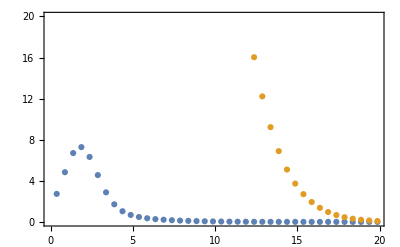

```mathematica
xx=RandomInteger[{1,Length@ls23d}]
ListPlot[{dataT,dataGen[[xx]]},PlotRange->{All,range},Frame->True]
```

### Data High

```mathematica
(* OS: Win, Linux *)
OS="Linux";
```

```mathematica
(* ModeHE, ModeAntiNu, ModeNu *)
(* Tau_minus, Tau_plus *)
```

```mathematica
mode="HE";sign="minus";
If[mode=="Nu",range=40,range=20];
```

```mathematica
(* Linux *)
```

```mathematica
If[OS=="Linux",data=Import[StringJoin["/home/adriano/Dropbox/Neutrinos/Tau/Data/Mat_WS_In_Mode",mode,"_Tau_",sign,".txt"],"Table"];
data=Table[{.5*i-.25/2,data[[i,2]]},{i,40}];
data2=Import[StringJoin["/home/adriano/Dropbox/Neutrinos/Tau/Data/Mat_WoutS_In_Mode",mode,"_Tau_",sign,".txt"],"Table"];
data2=Table[{.5*i-.25/2,data2[[i,2]]},{i,40}],data=Import[StringJoin["C:\\Users\\Orlando\\Dropbox\\Neutrinos\\Tau\\Data\\Mat_WS_In_Mode",mode,"_Tau_",sign,".txt"],"Table"];
data=Table[{.5*i-.25/2,data[[i,2]]},{i,40}];
data2=Import[StringJoin["C:\\Users\\Orlando\\Dropbox\\Neutrinos\\Tau\\Data\\Mat_WoutS_In_Mode",mode,"_Tau_",sign,".txt"],"Table"];
data2=Table[{.5*i-.25/2,data2[[i,2]]},{i,40}]];
```

### Data of Fig 1 by reconstructed energy

```mathematica
Clear[fs,fn]
fs[Ere_,Etrue_]:=If[Etrue<3.1,0,(*1/(Sqrt[2Pi]σe)*)(Exp[-1/2((Ere-x)/σe)^2]/.{x->b*Etrue,σe->r*Etrue}/.Thread[{b,r}->{.45,.25}])]
fn[Ere_,Etrue_]:=If[Etrue<3.1,0,fs[Ere,Etrue]/NIntegrate[fs[ere,Etrue],{ere,0,20}]]
```

```mathematica
(* dN/Subscript[dE, rec]=∫dN/Subscript[dE, true] P(Subscript[E, rec],Subscript[E, true])ⅆ Subscript[E, true] *)
(* doing numerical integration by cutting the integrand *)
dataT=Table[{data2[[j,1]],Sum[fn[data2[[j,1]],data2[[i,1]]]*0.5*data2[[i,2]],{i,40}]},{j,40}];
(*dataT=Table[{.5*j-.25,Sum[fn[0.5*j-.25,.5*i-.25]*0.5*data2[[i,2]],{i,40}]},{j,40}]//Quiet;*)
dtrue=Interpolation@data2;
ndtrue=NIntegrate[dtrue[x],{x,Min@data[[All,1]],Max@data[[All,1]]}]
dre=Interpolation@data;
ndre=NIntegrate[dre[x],{x,Min@data[[All,1]],Max@data[[All,1]]}]
dreInt=Interpolation@dataT;
ndreInt=NIntegrate[dreInt[x],{x,Min@data[[All,1]],Max@data[[All,1]]}]
fac2=ndtrue/ndreInt
(*dataT=Table[{.5*j-.25,fac2*Sum[fn[0.5*j-.25,.5*i]*0.5*data2[[i,2]],{i,40}]},{j,40}]//Quiet;*)
dataT=Table[{data2[[j,1]],fac2*Sum[fn[data2[[j,1]],data2[[i,1]]]*0.5*data2[[i,2]],{i,40}]},{j,40}];
```

77.45

76.1852

75.6044

1.02441

```mathematica
ListPlot[{data,dataT},Frame->True,PlotRange->{{0,20},{0,40}},AspectRatio->1]
```

-Graphics-

### General Probability ratio

```mathematica
ratioGen[S23_,δ_,epS_,ee_]=(ee (-537.0144158815365 s23^2+(95.922402136029-4.114998188599089 ee) ee s23^2+(537.0144158815365+ee (-95.92240213602899+4.114998188599089 ee)) s23^4+epS^2 (-194626.6461383849+(34963.71557858255-1499.9168397443682 ee) ee+382355.29126830207 s23^2+ee (-69927.4311571651+2999.8336794887364 ee) s23^2+(-391483.50917764+(69927.4311571651-2999.8336794887364 ee) ee) s23^4)+epS s23 √(1-s23^2) (14161.307084011187-28998.778457602955 s23^2+ee (-2589.904857672781+5179.809715345562 s23^2+ee (111.1049510921754-222.2099021843508 s23^2))))-2536.820066237314 epS s23 √(1-s23^2) Sin[8.323065282815573/ee]+1119.5858672098655 ee epS s23 √(1-s23^2) Sin[8.323065282815573/ee]-39.38853098975155 ee^2 epS s23 √(1-s23^2) Sin[8.323065282815573/ee]+5073.640132474628 epS s23^3 √(1-s23^2) Sin[8.323065282815573/ee]-1796.3230913768598 ee epS s23^3 √(1-s23^2) Sin[8.323065282815573/ee]+78.7770619795031 ee^2 epS s23^3 √(1-s23^2) Sin[8.323065282815573/ee]+Cos[δ] (s23 (epS s23 (261.20978051393564-348.27970735191445 s23^2)+4701.776049250849 epS^2 s23^2 √(1-s23^2)-6.44962421022064 √(1-s23^2) (-0.5+1. s23^2))+ee s23 (-403.4052420503069 epS^2 s23^2 √(1-s23^2)+0.5533679589167451 √(1-s23^2) (-0.4999999999999999+1. s23^2)+epS s23 (-22.411402336128184+29.881869781504182 s23^2))+ee^3 (-0.03334587340666304 √(1-s23^2) (-0.5 s23+1. s23^3)+24.30914171345736 epS^2 √(1-s23^2) (-0.5 s23+1. s23^3)+epS (-0.22508464549497562+1.8006771639598036 s23^2-1.800677163959804 s23^4))+ee^2 (0.38865342484877047 √(1-s23^2) (-0.5 s23+1. s23^3)-283.3283467147537 epS^2 √(1-s23^2) (-0.5 s23+1. s23^3)+epS (2.623410617729201-20.987284941833607 s23^2+20.987284941833604 s23^4))+s23 (epS^2 √(1-s23^2) (-12603.870244016523+1081.3929190371105 ee+12603.870244016523 s23^2-1081.3929190371105 ee s23^2)+√(1-s23^2) (8.644629796993499-0.7416961035919825 ee-17.289259593986998 s23^2+1.483392207183965 ee s23^2)+epS s23 (1167.0250225941222-100.12897398491762 ee-933.6200180752978 s23^2+80.1031791879341 ee s23^2)) Sin[8.323065282815573/ee])-8.644629796993499 s23 √(1-s23^2) Sin[δ]+0.7416961035919825 ee s23 √(1-s23^2) Sin[δ]+3.2248121051103213 s23 √(1-s23^2) Sin[8.323065282815573/ee] Sin[δ]-0.2766839794583725 ee s23 √(1-s23^2) Sin[8.323065282815573/ee] Sin[δ]+Sin[8.323065282815573/ee] (-5978.45668107876 ee epS^2+(93.95629874953016-68494.14178840749 epS^2+ee (-33.26524243290481+1.4588344811019092 ee+30228.81841466637 epS^2-1063.4903367232919 ee epS^2)) s23^2+(-93.95629874953016+68494.14178840749 epS^2+ee (33.26524243290481-1.4588344811019092 ee-24250.361733587608 epS^2+1063.4903367232919 ee epS^2)) s23^4+(87.06992683797868-7.470467445376055 ee) epS s23^2 Sin[δ])+Cos[8.323065282815573/ee] (ee ((537.0144158815365+ee (-95.92240213602898+4.114998188599088 ee)) s23^2+(-537.0144158815365+(95.92240213602898-4.114998188599088 ee) ee) s23^4+epS^2 (-6898.001008467854+(-384585.5081691722+(69927.43115716509-2999.8336794887364 ee) ee) s23^2+(391483.50917764+ee (-69927.4311571651+2999.8336794887364 ee)) s23^4)+epS s23 √(1-s23^2) (-14243.90770996934+28998.778457602955 s23^2+ee (2589.904857672781-5179.809715345562 s23^2+ee (-111.1049510921754+222.2099021843508 s23^2))))+s23 (epS s23 (-435.3496341898932+ee (37.352337226880266+(20.987284941833604-1.8006771639598043 ee) ee)+(348.2797073519141+ee (-29.881869781504264+ee (-20.987284941833607+1.800677163959804 ee))) s23^2)+epS^2 √(1-s23^2) (4701.776049250852-4701.776049250846 s23^2+ee (-403.4052420503069+403.4052420503069 s23^2+ee (-141.66417335737682+12.15457085672868 ee+283.3283467147537 s23^2-24.30914171345736 ee s23^2)))+√(1-s23^2) (-3.224812105110321+6.449624210220642 s23^2+ee (0.27668397945837264-0.553367958916745 s23^2+ee (0.19432671242438523-0.01667293670333152 ee-0.38865342484877047 s23^2+0.03334587340666304 ee s23^2)))) Cos[δ]+s23 ((233.40500451882428-20.025794796983522 ee) epS s23-0.7416961035919825 (-11.65521802680122+1. ee) √(1-s23^2)) Sin[δ])+epS ((87.06992683797863+ee (-7.4704674453760544+(-2.623410617729201+0.22508464549497553 ee) ee)) Cos[8.323065282815573/ee+δ]+2.842170943040401*^-14 Sin[8.323065282815573/ee-δ]+(-233.40500451882443+20.025794796983533 ee) s23^2 Sin[δ]+(-233.40500451882437+20.025794796983526 ee) Sin[8.323065282815573/ee+δ]))/(2.7607421580402205+ee (-130.8796094130282+(23.3230292223281-1. ee) ee)+(-2.76074215804022+ee (130.87960941302822+ee (-23.323029222328106+1. ee))) Cos[8.323065282815573/ee]+(22.46560935192947+(-8.05902865451455+0.3548994794121858 ee) ee) Sin[8.323065282815573/ee])/.s23->Sqrt[S23];
```

### Creating data with s23 and NSI

```mathematica
(* Subscript[dN, nsi]/Subscript[dE, rec]=∫Subscript[dN, nsi]/Subscript[dE, true] P(Subscript[E, rec],Subscript[E, true])ⅆ Subscript[E, true] =∫(Subscript[P, NSI](μ->τ))/Subscript[P, SM(μ->τ)] Subscript[dN, sm]/Subscript[dE, true] P(Subscript[E, rec],Subscript[E, true])ⅆ Subscript[E, true] *)
```

```mathematica
(* best-fit used {S23,δ} = {0.582,-2.5} *)
```

```mathematica
passos23=.4/10;
passodelta=2./10;
dataGen={};ls23d={};
Clear[delta,ss23];
Do[ss23=(0.582)-.2+passos23*i;
Do[delta=(-1.+passodelta*k);AppendTo[ls23d,{ss23,delta}];
AppendTo[dataGen,Table[{data2[[j,1]],fac2*Sum[fn[data2[[j,1]],data2[[i,1]]]*0.5*data2[[i,2]]*ratioGen[ss23,-2.5,delta,.5*i],{i,40}]},{j,40}]],{k,0,10}],{i,0,10}]//Quiet;
```

```mathematica
Plot[ratioGen[(0.582),del,0,2],{del,-2*Pi,2*Pi}]
```

-Graphics-

```mathematica
dataGen//Dimensions
```

{121,40,2}

31

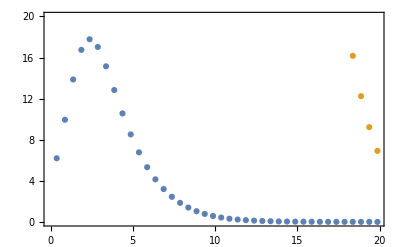

```mathematica
xx=RandomInteger[{1,Length@ls23d}]
ListPlot[{dataT,dataGen[[xx]]},PlotRange->{All,range},Frame->True]
```

### Chi square

```mathematica
(* χ^2 = 2 Sum[ndata - ntrue + ntrue*Log(ntrue/ndata),{i,bin}] *)
```

```mathematica
chis23d=Table[Sum[dataGen[[j,i,2]]-dataT[[i,2]]+dataT[[i,2]]*Log[dataT[[i,2]]/dataGen[[j,i,2]]],{i,40}],{j,Length@dataGen}]//Chop
```

{385993.,246953.,138767.,61450.7,15056.6,0.0577196,14347.1,60019.,136615.,244083.,382404.,382180.,244408.,137238.,60686.4,14804.8,0.00193435,14359.6,59787.9,135888.,242607.,379928.,379867.,242818.,136242.,60153.8,14606.5,0.0429381,14435.2,59808.1,135723.,242126.,379000.,379066.,242194.,135786.,59858.3,14464.4,0.0644759,14571.2,60073.9,136110.,242626.,379606.,379790.,242545.,135877.,59805.2,14381.1,0.0343767,14764.9,60579.6,137041.,244097.,381731.,382051.,243881.,136525.,59999.6,14359.2,0,15013.4,61319.6,138508.,246527.,385359.,385862.,246213.,137735.,60447.,14401.5,0.0943621,15314.,62288.1,140502.,249903.,390476.,391237.,249552.,139518.,61153.3,14511.,0.55473,15663.8,63478.8,143012.,254213.,397065.,398192.,253911.,141884.,62125.1,14690.9,1.75957,16059.2,64884.9,146030.,259443.,405108.,406745.,259306.,144842.,63370.1,14945.2,4.29738,16496.5,66498.4,149542.,265576.,414584.,416919.,265754.,148408.,64897.7,15278.5,9.09799,16970.9,68309.5,153533.,272591.,425467.}

```mathematica
dataSet3=chis23d;
```

### Data

```mathematica
ls23d
```

{{0.382,-1.},{0.382,-0.8},{0.382,-0.6},{0.382,-0.4},{0.382,-0.2},{0.382,0.},{0.382,0.2},{0.382,0.4},{0.382,0.6},{0.382,0.8},{0.382,1.},{0.422,-1.},{0.422,-0.8},{0.422,-0.6},{0.422,-0.4},{0.422,-0.2},{0.422,0.},{0.422,0.2},{0.422,0.4},{0.422,0.6},{0.422,0.8},{0.422,1.},{0.462,-1.},{0.462,-0.8},{0.462,-0.6},{0.462,-0.4},{0.462,-0.2},{0.462,0.},{0.462,0.2},{0.462,0.4},{0.462,0.6},{0.462,0.8},{0.462,1.},{0.502,-1.},{0.502,-0.8},{0.502,-0.6},{0.502,-0.4},{0.502,-0.2},{0.502,0.},{0.502,0.2},{0.502,0.4},{0.502,0.6},{0.502,0.8},{0.502,1.},{0.542,-1.},{0.542,-0.8},{0.542,-0.6},{0.542,-0.4},{0.542,-0.2},{0.542,0.},{0.542,0.2},{0.542,0.4},{0.542,0.6},{0.542,0.8},{0.542,1.},{0.582,-1.},{0.582,-0.8},{0.582,-0.6},{0.582,-0.4},{0.582,-0.2},{0.582,0.},{0.582,0.2},{0.582,0.4},{0.582,0.6},{0.582,0.8},{0.582,1.},{0.622,-1.},{0.622,-0.8},{0.622,-0.6},{0.622,-0.4},{0.622,-0.2},{0.622,0.},{0.622,0.2},{0.622,0.4},{0.622,0.6},{0.622,0.8},{0.622,1.},{0.662,-1.},{0.662,-0.8},{0.662,-0.6},{0.662,-0.4},{0.662,-0.2},{0.662,0.},{0.662,0.2},{0.662,0.4},{0.662,0.6},{0.662,0.8},{0.662,1.},{0.702,-1.},{0.702,-0.8},{0.702,-0.6},{0.702,-0.4},{0.702,-0.2},{0.702,0.},{0.702,0.2},{0.702,0.4},{0.702,0.6},{0.702,0.8},{0.702,1.},{0.742,-1.},{0.742,-0.8},{0.742,-0.6},{0.742,-0.4},{0.742,-0.2},{0.742,0.},{0.742,0.2},{0.742,0.4},{0.742,0.6},{0.742,0.8},{0.742,1.},{0.782,-1.},{0.782,-0.8},{0.782,-0.6},{0.782,-0.4},{0.782,-0.2},{0.782,0.},{0.782,0.2},{0.782,0.4},{0.782,0.6},{0.782,0.8},{0.782,1.}}

```mathematica
dataSet1
```

{161975.,103633.,58225.4,25763.2,6281.58,0.0417651,5792.35,24764.2,56721.,101625.,159463.,159284.,101837.,57147.1,25224.8,6105.95,0.00127844,5801.76,24603.4,56211.2,100588.,157721.,157659.,100720.,56446.7,24850.7,5967.95,0.0302018,5855.3,24620.6,56100.1,100257.,157080.,157109.,100288.,56129.8,24644.6,5869.36,0.045592,5951.05,24811.6,56381.4,100624.,157529.,157642.,100550.,56201.8,24610.,5811.93,0.0243565,6087.22,25172.6,57049.1,101681.,159057.,159268.,101511.,56668.2,24750.8,5797.45,0,6262.,25699.6,58097.1,103419.,161655.,161996.,103181.,57534.8,25070.8,5827.83,0.0669707,6473.51,26388.7,59519.1,105830.,165310.,165837.,105566.,58807.9,25574.4,5905.17,0.393879,6719.75,27235.5,61308.7,108905.,170012.,170800.,108677.,60494.6,26266.2,6031.89,1.24978,6998.43,28235.3,63458.4,112633.,175749.,176901.,112523.,62603.,27152.,6210.84,3.05311,7306.86,29382.5,65959.6,117004.,182504.,184154.,117119.,65143.4,28238.4,6445.5,6.46513,7641.72,30670.2,68802.,122003.,190261.}

```mathematica
dataSet2
```

{0.00955227,0.0151173,0.0201663,0.0217431,0.0188223,0.0132932,0.00815678,0.00515131,0.00440894,0.00580177,0.00955227,0.00216988,0.000479221,0.0000261919,6.42941×10^-6,0.000156884,0.00123485,0.0035913,0.00598536,0.00653895,0.00477735,0.00216988,0.0166804,0.0110593,0.0079711,0.00766309,0.0101235,0.0152672,0.0217762,0.0267139,0.0272771,0.0231249,0.0166804,0.0232723,0.0166782,0.0131663,0.0131873,0.01674,0.0233622,0.0310603,0.0363371,0.0363028,0.0309769,0.0232723,0.0137825,0.00893046,0.00665395,0.00697184,0.00990586,0.015272,0.021447,0.0254073,0.024807,0.0200147,0.0137825,0.000531912,1.49034×10^-7,0.000129918,0.0000609186,0.000104732,0.00122679,0.00331186,0.00478509,0.00429141,0.00229689,0.000531912,0.017911,0.024242,0.0274947,0.0256572,0.0198707,0.0133784,0.00885252,0.00711922,0.00809046,0.0118224,0.017911,0.127176,0.14299,0.149636,0.14385,0.128455,0.110425,0.0967018,0.0914851,0.0960625,0.109281,0.127176,0.425975,0.454119,0.46396,0.451067,0.421182,0.386883,0.361171,0.352656,0.363938,0.391501,0.425975,1.06608,1.10985,1.12216,1.09771,1.04691,0.99041,0.949501,0.93839,0.96073,1.00903,1.06608,2.28724,2.35073,2.36415,2.32185,2.24138,2.15486,2.09479,2.08241,2.12196,2.19967,2.28724}

```mathematica
dataSet3
```

{385993.,246953.,138767.,61450.7,15056.6,0.0577196,14347.1,60019.,136615.,244083.,382404.,382180.,244408.,137238.,60686.4,14804.8,0.00193435,14359.6,59787.9,135888.,242607.,379928.,379867.,242818.,136242.,60153.8,14606.5,0.0429381,14435.2,59808.1,135723.,242126.,379000.,379066.,242194.,135786.,59858.3,14464.4,0.0644759,14571.2,60073.9,136110.,242626.,379606.,379790.,242545.,135877.,59805.2,14381.1,0.0343767,14764.9,60579.6,137041.,244097.,381731.,382051.,243881.,136525.,59999.6,14359.2,0,15013.4,61319.6,138508.,246527.,385359.,385862.,246213.,137735.,60447.,14401.5,0.0943621,15314.,62288.1,140502.,249903.,390476.,391237.,249552.,139518.,61153.3,14511.,0.55473,15663.8,63478.8,143012.,254213.,397065.,398192.,253911.,141884.,62125.1,14690.9,1.75957,16059.2,64884.9,146030.,259443.,405108.,406745.,259306.,144842.,63370.1,14945.2,4.29738,16496.5,66498.4,149542.,265576.,414584.,416919.,265754.,148408.,64897.7,15278.5,9.09799,16970.9,68309.5,153533.,272591.,425467.}

### Contour

```mathematica
dataSet1;
```

```mathematica
dataSet2;
```

```mathematica
dataSet=dataSet1+dataSet2+dataSet3;
```

InterpolatingFunction[…]

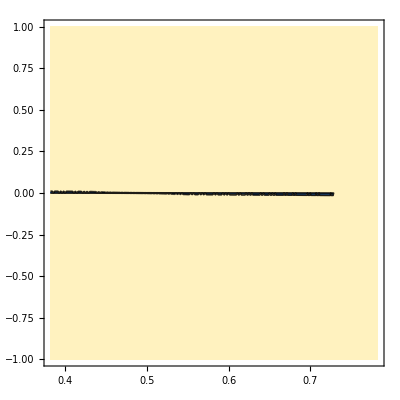

```mathematica
Table[{ls23d[[i]],{dataSet[[i]]}},{i,Length@ls23d}];
func=Interpolation@%
ContourPlot[func[s23,del],{s23,Min@ls23d[[All,1]],Max@ls23d[[All,1]]},{del,Min@ls23d[[All,2]],Max@ls23d[[All,2]]},Contours->{2.3,4.6,6.}]
```

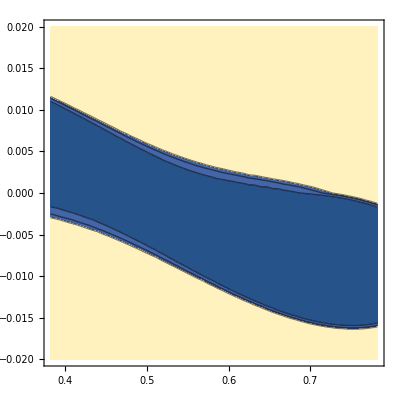

```mathematica
ContourPlot[func[s23,del],{s23,Min@ls23d[[All,1]],Max@ls23d[[All,1]]},{del,Min@ls23d[[All,2]]/50,Max@ls23d[[All,2]]/50},Contours->{2.3,4.6,6.}]
```

## All data sets - s23 and dm31

### Data Nu

```mathematica
(* OS: Win, Linux *)
OS="Linux";
```

```mathematica
(* ModeHE, ModeAntiNu, ModeNu *)
(* Tau_minus, Tau_plus *)
```

```mathematica
mode="Nu";sign="minus";
If[mode=="Nu",range=40,range=20];
```

```mathematica
(* Linux *)
```

```mathematica
If[OS=="Linux",data=Import[StringJoin["/home/adriano/Dropbox/Neutrinos/Tau/Data/Mat_WS_In_Mode",mode,"_Tau_",sign,".txt"],"Table"];
data=Table[{.5*i-.25/2,data[[i,2]]},{i,40}];
data2=Import[StringJoin["/home/adriano/Dropbox/Neutrinos/Tau/Data/Mat_WoutS_In_Mode",mode,"_Tau_",sign,".txt"],"Table"];
data2=Table[{.5*i-.25/2,data2[[i,2]]},{i,40}],data=Import[StringJoin["C:\\Users\\Orlando\\Dropbox\\Neutrinos\\Tau\\Data\\Mat_WS_In_Mode",mode,"_Tau_",sign,".txt"],"Table"];
data=Table[{.5*i-.25/2,data[[i,2]]},{i,40}];
data2=Import[StringJoin["C:\\Users\\Orlando\\Dropbox\\Neutrinos\\Tau\\Data\\Mat_WoutS_In_Mode",mode,"_Tau_",sign,".txt"],"Table"];
data2=Table[{.5*i-.25/2,data2[[i,2]]},{i,40}]];
```

### Data of Fig 1 by reconstructed energy

```mathematica
Clear[fs,fn]
fs[Ere_,Etrue_]:=If[Etrue<3.1,0,(*1/(Sqrt[2Pi]σe)*)(Exp[-1/2((Ere-x)/σe)^2]/.{x->b*Etrue,σe->r*Etrue}/.Thread[{b,r}->{.45,.25}])]
fn[Ere_,Etrue_]:=If[Etrue<3.1,0,fs[Ere,Etrue]/NIntegrate[fs[ere,Etrue],{ere,0,20}]]
```

```mathematica
(* dN/Subscript[dE, rec]=∫dN/Subscript[dE, true] P(Subscript[E, rec],Subscript[E, true])ⅆ Subscript[E, true] *)
(* doing numerical integration by cutting the integrand *)
dataT=Table[{data2[[j,1]],Sum[fn[data2[[j,1]],data2[[i,1]]]*0.5*data2[[i,2]],{i,40}]},{j,40}];
(*dataT=Table[{.5*j-.25,Sum[fn[0.5*j-.25,.5*i-.25]*0.5*data2[[i,2]],{i,40}]},{j,40}]//Quiet;*)
dtrue=Interpolation@data2;
ndtrue=NIntegrate[dtrue[x],{x,Min@data[[All,1]],Max@data[[All,1]]}]
dre=Interpolation@data;
ndre=NIntegrate[dre[x],{x,Min@data[[All,1]],Max@data[[All,1]]}]
dreInt=Interpolation@dataT;
ndreInt=NIntegrate[dreInt[x],{x,Min@data[[All,1]],Max@data[[All,1]]}]
fac2=ndtrue/ndreInt
(*dataT=Table[{.5*j-.25,fac2*Sum[fn[0.5*j-.25,.5*i]*0.5*data2[[i,2]],{i,40}]},{j,40}]//Quiet;*)
dataT=Table[{data2[[j,1]],fac2*Sum[fn[data2[[j,1]],data2[[i,1]]]*0.5*data2[[i,2]],{i,40}]},{j,40}];
```

54.4842

53.3873

52.517

1.03746

```mathematica
ListPlot[{data,dataT},Frame->True,PlotRange->{{0,20},{0,40}},AspectRatio->1]
```

-Graphics-

### General Probability ratio

```mathematica
pmut[s12_,c12_,s13_,c13_,s23_,c23_,δ_,dm31_,dm21_,ee_,emut_]=(dm31 (c23^4 ee emut^2 (-0.3158628171120001 dm31 ee+0.000034214444181731416 ee^2+dm31^2 (729.-1458. s13^2))+c23^3 ee emut (-2.5344032727208456*^-6 ee^2+dm31 ee (0.023397245712-8.673617379884035*^-19 s13^2)+dm31^2 (-54.+148.8066566943162 s13^2)) s23+c23^2 (c12^2 dm21 (-4.5474735088646407*^-13 dm31^2-2.7105054312137608*^-20 ee^2)+ee (1.9999999999999998 dm31^2-0.0008665646560000002 dm31 ee+9.386678787854984*^-8 ee^2+dm31 ((-3.5113576553450443+7.271321001515295*^-17 ⅈ) dm31+2.7105054312137608*^-20 ee+1101.7797307465376 dm31 emut^2) s13^2)) s23^2+c23 emut (c12^2 dm21 (-1.455191522836685*^-11 dm31^2-8.6736173798840345*^-19 ee^2)+ee (-0.023397245712 dm31 ee+2.5344032727208456*^-6 ee^2+dm31^2 (54.00000000000001-40.8066566943162 s13^2))) s23^3+ee (729. dm31^2-0.3158628171120001 dm31 ee+0.000034214444181731416 ee^2) emut^2 s23^4)+c23 dm31 (1101.7797307465376 c23^3 dm31^2 ee emut^2 s13^2+c23^2 emut (c12^2 dm21 (-1.455191522836685*^-11 dm31^2-8.6736173798840345*^-19 ee^2)+ee (-0.023397245712 dm31 ee+2.5344032727208456*^-6 ee^2+dm31^2 (54.-135.6133133886324 s13^2))) s23+c23 (c12^2 dm21 (4.5474735088646407*^-13 dm31^2+2.7105054312137608*^-20 ee^2)+ee (ee^2 (-9.386678787854984*^-8+0.00006842888836346283 emut^2)+dm31 ee (0.0008665646560000002-0.6317256342240002 emut^2-2.7105054312137608*^-20 s13^2)+dm31^2 (-1.9999999999999998+3.5113576553450443 s13^2+emut^2 (1458.-1458. s13^2)))) s23^2+ee emut (-2.5344032727208456*^-6 ee^2+dm31 ee (0.023397245712-8.673617379884035*^-19 s13^2)+dm31^2 (-54.+54. s13^2)) s23^3) Cos[(3296.2634783428016 dm31)/ee]+c12 c23 dm21 s12 s13 (-8.673617379884035*^-19 c23^3 dm31 ee^2 emut+c23^2 ((-0.0004332823280000001 dm31+9.386678787854984*^-8 ee) ee^2+(-1.6442870905801747*^6 dm31^3+356.22026925346245 dm31^2 ee+0.31586281711200004 dm31 ee^2-0.00006842888836346282 ee^3) emut^2) s23+c23 (121799.04374667956 dm31^3-26.386686611367594 dm31^2 ee-0.046794491423999995 dm31 ee^2+0.000010137613090883384 ee^3) emut s23^2+(-2255.5378471607337 dm31^3+0.4886423446549555 dm31^2 ee+dm31 ee^2 (0.0004332823280000001-0.3158628171119999 emut^2)+ee^3 (-9.386678787854982*^-8+0.00006842888836346282 emut^2)) s23^3) Cos[(3296.2634783428016 dm31)/ee-1. δ]-0.011698622856 c12 c23^4 dm21 dm31 ee^2 emut s12 s13 Cos[δ]+2.5344032727208456*^-6 c12 c23^4 dm21 ee^3 emut s12 s13 Cos[δ]-9231.855862812848 c12 c23^3 dm21 dm31^3 s12 s13 s23 Cos[δ]+2.000000000000001 c12 c23^3 dm21 dm31^2 ee s12 s13 s23 Cos[δ]+0.0008665646560000002 c12 c23^3 dm21 dm31 ee^2 s12 s13 s23 Cos[δ]-1.8773357575709967*^-7 c12 c23^3 dm21 ee^3 s12 s13 s23 Cos[δ]+1458. c12 c23^3 dm21 dm31^2 ee emut^2 s12 s13 s23 Cos[δ]-0.9475884513359999 c12 c23^3 dm21 dm31 ee^2 emut^2 s12 s13 s23 Cos[δ]+0.00013685777672692564 c12 c23^3 dm21 ee^3 emut^2 s12 s13 s23 Cos[δ]-747780.3248878407 c12 c23^2 dm21 dm31^3 emut s12 s13 s23^2 Cos[δ]+54.00000000000003 c12 c23^2 dm21 dm31^2 ee emut s12 s13 s23^2 Cos[δ]+0.093588982848 c12 c23^2 dm21 dm31 ee^2 emut s12 s13 s23^2 Cos[δ]-0.000015206419636325076 c12 c23^2 dm21 ee^3 emut s12 s13 s23^2 Cos[δ]+9231.855862812848 c12 c23 dm21 dm31^3 s12 s13 s23^3 Cos[δ]-5.551115123125783*^-16 c12 c23 dm21 dm31^2 ee s12 s13 s23^3 Cos[δ]-0.0012998469840000003 c12 c23 dm21 dm31 ee^2 s12 s13 s23^3 Cos[δ]+1.8773357575709967*^-7 c12 c23 dm21 ee^3 s12 s13 s23^3 Cos[δ]-1.3460045847981133*^7 c12 c23 dm21 dm31^3 emut^2 s12 s13 s23^3 Cos[δ]+2916.000000000001 c12 c23 dm21 dm31^2 ee emut^2 s12 s13 s23^3 Cos[δ]+0.6317256342240001 c12 c23 dm21 dm31 ee^2 emut^2 s12 s13 s23^3 Cos[δ]-0.00013685777672692564 c12 c23 dm21 ee^3 emut^2 s12 s13 s23^3 Cos[δ]+249260.10829594688 c12 dm21 dm31^3 emut s12 s13 s23^4 Cos[δ]-54.00000000000001 c12 dm21 dm31^2 ee emut s12 s13 s23^4 Cos[δ]-0.011698622856 c12 dm21 dm31 ee^2 emut s12 s13 s23^4 Cos[δ]+2.5344032727208456*^-6 c12 dm21 ee^3 emut s12 s13 s23^4 Cos[δ]+6976.318015652115 c12 c23^3 dm21 dm31^3 s12 s13 s23 Cos[1. δ]-1.511357655345045 c12 c23^3 dm21 dm31^2 ee s12 s13 s23 Cos[1. δ]-1458. c12 c23^3 dm21 dm31^2 ee emut^2 s12 s13 s23 Cos[1. δ]+0.31586281711200004 c12 c23^3 dm21 dm31 ee^2 emut^2 s12 s13 s23 Cos[1. δ]+565081.7592678213 c12 c23^2 dm21 dm31^3 emut s12 s13 s23^2 Cos[1. δ]-14.419970082948637 c12 c23^2 dm21 dm31^2 ee emut s12 s13 s23^2 Cos[1. δ]-0.023397245712 c12 c23^2 dm21 dm31 ee^2 emut s12 s13 s23^2 Cos[1. δ]-6976.318015652115 c12 c23 dm21 dm31^3 s12 s13 s23^3 Cos[1. δ]-0.48864234465495493 c12 c23 dm21 dm31^2 ee s12 s13 s23^3 Cos[1. δ]+0.0004332823280000001 c12 c23 dm21 dm31 ee^2 s12 s13 s23^3 Cos[1. δ]+1.0171471666820783*^7 c12 c23 dm21 dm31^3 emut^2 s12 s13 s23^3 Cos[1. δ]-2203.559461493075 c12 c23 dm21 dm31^2 ee emut^2 s12 s13 s23^3 Cos[1. δ]-188360.5864226071 c12 dm21 dm31^3 emut s12 s13 s23^4 Cos[1. δ]+40.80665669431621 c12 dm21 dm31^2 ee emut s12 s13 s23^4 Cos[1. δ]-249260.10829594688 c12 c23^4 dm21 dm31^3 emut s12 s13 Cos[(3296.2634783428016 dm31)/ee+δ]+54.000000000000014 c12 c23^4 dm21 dm31^2 ee emut s12 s13 Cos[(3296.2634783428016 dm31)/ee+δ]+0.011698622856000002 c12 c23^4 dm21 dm31 ee^2 emut s12 s13 Cos[(3296.2634783428016 dm31)/ee+δ]-2.5344032727208456*^-6 c12 c23^4 dm21 ee^3 emut s12 s13 Cos[(3296.2634783428016 dm31)/ee+δ]+9231.855862812848 c12 c23^3 dm21 dm31^3 s12 s13 s23 Cos[(3296.2634783428016 dm31)/ee+δ]-2.000000000000001 c12 c23^3 dm21 dm31^2 ee s12 s13 s23 Cos[(3296.2634783428016 dm31)/ee+δ]-0.0004332823280000001 c12 c23^3 dm21 dm31 ee^2 s12 s13 s23 Cos[(3296.2634783428016 dm31)/ee+δ]+9.386678787854984*^-8 c12 c23^3 dm21 ee^3 s12 s13 s23 Cos[(3296.2634783428016 dm31)/ee+δ]-6.730022923990566*^6 c12 c23^3 dm21 dm31^3 emut^2 s12 s13 s23 Cos[(3296.2634783428016 dm31)/ee+δ]+1458.0000000000005 c12 c23^3 dm21 dm31^2 ee emut^2 s12 s13 s23 Cos[(3296.2634783428016 dm31)/ee+δ]+0.31586281711200004 c12 c23^3 dm21 dm31 ee^2 emut^2 s12 s13 s23 Cos[(3296.2634783428016 dm31)/ee+δ]-0.00006842888836346282 c12 c23^3 dm21 ee^3 emut^2 s12 s13 s23 Cos[(3296.2634783428016 dm31)/ee+δ]+249260.10829594696 c12 c23^2 dm21 dm31^3 emut s12 s13 s23^2 Cos[(3296.2634783428016 dm31)/ee+δ]-(0.035095868568+1.925929944387236*^-34 ⅈ) c12 c23^2 dm21 dm31 ee^2 emut s12 s13 s23^2 Cos[(3296.2634783428016 dm31)/ee+δ]+5.068806545441692*^-6 c12 c23^2 dm21 ee^3 emut s12 s13 s23^2 Cos[(3296.2634783428016 dm31)/ee+δ]-1.9999999999999996 c12 c23 dm21 dm31^2 ee s12 s13 s23^3 Cos[(3296.2634783428016 dm31)/ee+δ]+0.0008665646560000002 c12 c23 dm21 dm31 ee^2 s12 s13 s23^3 Cos[(3296.2634783428016 dm31)/ee+δ]-9.386678787854982*^-8 c12 c23 dm21 ee^3 s12 s13 s23^3 Cos[(3296.2634783428016 dm31)/ee+δ]+1458. c12 c23 dm21 dm31^2 ee emut^2 s12 s13 s23^3 Cos[(3296.2634783428016 dm31)/ee+δ]-0.631725634224 c12 c23 dm21 dm31 ee^2 emut^2 s12 s13 s23^3 Cos[(3296.2634783428016 dm31)/ee+δ]+0.00006842888836346282 c12 c23 dm21 ee^3 emut^2 s12 s13 s23^3 Cos[(3296.2634783428016 dm31)/ee+δ]-54. c12 dm21 dm31^2 ee emut s12 s13 s23^4 Cos[(3296.2634783428016 dm31)/ee+δ]+0.023397245712 c12 dm21 dm31 ee^2 emut s12 s13 s23^4 Cos[(3296.2634783428016 dm31)/ee+δ]-2.5344032727208456*^-6 c12 dm21 ee^3 emut s12 s13 s23^4 Cos[(3296.2634783428016 dm31)/ee+δ]+188360.5864226071 c12 c23^4 dm21 dm31^3 emut s12 s13 Cos[(3296.2634783428016 dm31)/ee+1. δ]-40.80665669431621 c12 c23^4 dm21 dm31^2 ee emut s12 s13 Cos[(3296.2634783428016 dm31)/ee+1. δ]-6976.318015652115 c12 c23^3 dm21 dm31^3 s12 s13 s23 Cos[(3296.2634783428016 dm31)/ee+1. δ]+1.511357655345045 c12 c23^3 dm21 dm31^2 ee s12 s13 s23 Cos[(3296.2634783428016 dm31)/ee+1. δ]+5.085735833410392*^6 c12 c23^3 dm21 dm31^3 emut^2 s12 s13 s23 Cos[(3296.2634783428016 dm31)/ee+1. δ]-1101.7797307465376 c12 c23^3 dm21 dm31^2 ee emut^2 s12 s13 s23 Cos[(3296.2634783428016 dm31)/ee+1. δ]-188360.5864226071 c12 c23^2 dm21 dm31^3 emut s12 s13 s23^2 Cos[(3296.2634783428016 dm31)/ee+1. δ]-13.19334330568379 c12 c23^2 dm21 dm31^2 ee emut s12 s13 s23^2 Cos[(3296.2634783428016 dm31)/ee+1. δ]+0.011698622856 c12 c23^2 dm21 dm31 ee^2 emut s12 s13 s23^2 Cos[(3296.2634783428016 dm31)/ee+1. δ]+1.9999999999999998 c12 c23 dm21 dm31^2 ee s12 s13 s23^3 Cos[(3296.2634783428016 dm31)/ee+1. δ]-0.0004332823280000001 c12 c23 dm21 dm31 ee^2 s12 s13 s23^3 Cos[(3296.2634783428016 dm31)/ee+1. δ]-1458. c12 c23 dm21 dm31^2 ee emut^2 s12 s13 s23^3 Cos[(3296.2634783428016 dm31)/ee+1. δ]+0.31586281711200004 c12 c23 dm21 dm31 ee^2 emut^2 s12 s13 s23^3 Cos[(3296.2634783428016 dm31)/ee+1. δ]+54. c12 dm21 dm31^2 ee emut s12 s13 s23^4 Cos[(3296.2634783428016 dm31)/ee+1. δ]-0.011698622856 c12 dm21 dm31 ee^2 emut s12 s13 s23^4 Cos[(3296.2634783428016 dm31)/ee+1. δ]+954.9059770030174 c23^4 dm31^3 ee emut^2 s13^2 Sin[(3296.2634783428016 dm31)/ee]+177998.22783051126 c12^2 c23^3 dm21 dm31^3 emut s23 Sin[(3296.2634783428016 dm31)/ee]-77.12348653427833 c12^2 c23^3 dm21 dm31^2 ee emut s23 Sin[(3296.2634783428016 dm31)/ee]+0.008354060947262194 c12^2 c23^3 dm21 dm31 ee^2 emut s23 Sin[(3296.2634783428016 dm31)/ee]-109.29551934143674 c23^3 dm31^3 ee emut s13^2 s23 Sin[(3296.2634783428016 dm31)/ee]+0.008354060947262194 c23^3 dm31^2 ee^2 emut s13^2 s23 Sin[(3296.2634783428016 dm31)/ee]-6592.526956685602 c12^2 c23^2 dm21 dm31^3 s23^2 Sin[(3296.2634783428016 dm31)/ee]+2.856425427195494 c12^2 c23^2 dm21 dm31^2 ee s23^2 Sin[(3296.2634783428016 dm31)/ee]-0.0003094096647134146 c12^2 c23^2 dm21 dm31 ee^2 s23^2 Sin[(3296.2634783428016 dm31)/ee]+4.805952151423804*^6 c12^2 c23^2 dm21 dm31^3 emut^2 s23^2 Sin[(3296.2634783428016 dm31)/ee]-2082.334136425515 c12^2 c23^2 dm21 dm31^2 ee emut^2 s23^2 Sin[(3296.2634783428016 dm31)/ee]+0.22555964557607924 c12^2 c23^2 dm21 dm31 ee^2 emut^2 s23^2 Sin[(3296.2634783428016 dm31)/ee]+2.7380974557143687 c23^2 dm31^3 ee s13^2 s23^2 Sin[(3296.2634783428016 dm31)/ee]-0.0003094096647134146 c23^2 dm31^2 ee^2 s13^2 s23^2 Sin[(3296.2634783428016 dm31)/ee]-1041.1670682127576 c23^2 dm31^3 ee emut^2 s13^2 s23^2 Sin[(3296.2634783428016 dm31)/ee]+0.22555964557607924 c23^2 dm31^2 ee^2 emut^2 s13^2 s23^2 Sin[(3296.2634783428016 dm31)/ee]-177998.22783051128 c12^2 c23 dm21 dm31^3 emut s23^3 Sin[(3296.2634783428016 dm31)/ee]+77.12348653427834 c12^2 c23 dm21 dm31^2 ee emut s23^3 Sin[(3296.2634783428016 dm31)/ee]-0.008354060947262194 c12^2 c23 dm21 dm31 ee^2 emut s23^3 Sin[(3296.2634783428016 dm31)/ee]+38.561743267139164 c23 dm31^3 ee emut s13^2 s23^3 Sin[(3296.2634783428016 dm31)/ee]-0.008354060947262194 c23 dm31^2 ee^2 emut s13^2 s23^3 Sin[(3296.2634783428016 dm31)/ee]+4.407777171115168*^6 c12 c23^3 dm21 dm31^3 emut^2 s12 s13 s23 Sin[(3296.2634783428016 dm31)/ee-1. δ]-954.9059770030176 c12 c23^3 dm21 dm31^2 ee emut^2 s12 s13 s23 Sin[(3296.2634783428016 dm31)/ee-1. δ]-326502.0126751977 c12 c23^2 dm21 dm31^3 emut s12 s13 s23^2 Sin[(3296.2634783428016 dm31)/ee-1. δ]+70.7337760742976 c12 c23^2 dm21 dm31^2 ee emut s12 s13 s23^2 Sin[(3296.2634783428016 dm31)/ee-1. δ]+6046.333568059216 c12 c23 dm21 dm31^3 s12 s13 s23^3 Sin[(3296.2634783428016 dm31)/ee-1. δ]-1.3098847421166222 c12 c23 dm21 dm31^2 ee s12 s13 s23^3 Sin[(3296.2634783428016 dm31)/ee-1. δ]-1.0249418938915565*^-12 c12 c23^3 dm21 dm31^3 s12 s13 s23 Sin[δ]+4.440892098500627*^-16 c12 c23^3 dm21 dm31^2 ee s12 s13 s23 Sin[δ]-4.8104001670878927*^-20 c12 c23^3 dm21 dm31 ee^2 s12 s13 s23 Sin[δ]-5.534686227014404*^-11 c12 c23^2 dm21 dm31^3 emut s12 s13 s23^2 Sin[δ]+2.3980817331903384*^-14 c12 c23^2 dm21 dm31^2 ee emut s12 s13 s23^2 Sin[δ]-(2.5976160902274616*^-18+1.3877787807814457*^-17 ⅈ) c12 c23^2 dm21 dm31 ee^2 emut s12 s13 s23^2 Sin[δ]-7.471826406469446*^-10 c12 c23 dm21 dm31^3 emut^2 s12 s13 s23^3 Sin[δ]+3.237410339806957*^-13 c12 c23 dm21 dm31^2 ee emut^2 s12 s13 s23^3 Sin[δ]-3.5067817218070734*^-17 c12 c23 dm21 dm31 ee^2 emut^2 s12 s13 s23^3 Sin[δ]+6046.333568059216 c12 c23^3 dm21 dm31^3 s12 s13 s23 Sin[1. δ]-1.3098847421166222 c12 c23^3 dm21 dm31^2 ee s12 s13 s23 Sin[1. δ]+1.6187051699034782*^-13 c12 c23^3 dm21 dm31^2 ee emut^2 s12 s13 s23 Sin[1. δ]-3.5067817218070734*^-17 c12 c23^3 dm21 dm31 ee^2 emut^2 s12 s13 s23 Sin[1. δ]+163251.00633759884 c12 c23^2 dm21 dm31^3 emut s12 s13 s23^2 Sin[1. δ]-35.3668880371488 c12 c23^2 dm21 dm31^2 ee emut s12 s13 s23^2 Sin[1. δ]+2.5976160902274616*^-18 c12 c23^2 dm21 dm31 ee^2 emut s12 s13 s23^2 Sin[1. δ]+6046.333568059216 c12 c23 dm21 dm31^3 s12 s13 s23^3 Sin[1. δ]-1.3098847421166222 c12 c23 dm21 dm31^2 ee s12 s13 s23^3 Sin[1. δ]-4.8104001670878927*^-20 c12 c23 dm21 dm31 ee^2 s12 s13 s23^3 Sin[1. δ]+163251.00633759884 c12 dm21 dm31^3 emut s12 s13 s23^4 Sin[1. δ]-35.3668880371488 c12 dm21 dm31^2 ee emut s12 s13 s23^4 Sin[1. δ]-2.767343113507202*^-11 c12 c23^4 dm21 dm31^3 emut s12 s13 Sin[(3296.2634783428016 dm31)/ee+δ]+1.1990408665951692*^-14 c12 c23^4 dm21 dm31^2 ee emut s12 s13 Sin[(3296.2634783428016 dm31)/ee+δ]-1.2988080451137308*^-18 c12 c23^4 dm21 dm31 ee^2 emut s12 s13 Sin[(3296.2634783428016 dm31)/ee+δ]+1.0249418938915565*^-12 c12 c23^3 dm21 dm31^3 s12 s13 s23 Sin[(3296.2634783428016 dm31)/ee+δ]-4.440892098500627*^-16 c12 c23^3 dm21 dm31^2 ee s12 s13 s23 Sin[(3296.2634783428016 dm31)/ee+δ]+4.8104001670878927*^-20 c12 c23^3 dm21 dm31 ee^2 s12 s13 s23 Sin[(3296.2634783428016 dm31)/ee+δ]-7.471826406469446*^-10 c12 c23^3 dm21 dm31^3 emut^2 s12 s13 s23 Sin[(3296.2634783428016 dm31)/ee+δ]+3.237410339806957*^-13 c12 c23^3 dm21 dm31^2 ee emut^2 s12 s13 s23 Sin[(3296.2634783428016 dm31)/ee+δ]-3.5067817218070734*^-17 c12 c23^3 dm21 dm31 ee^2 emut^2 s12 s13 s23 Sin[(3296.2634783428016 dm31)/ee+δ]+2.767343113507202*^-11 c12 c23^2 dm21 dm31^3 emut s12 s13 s23^2 Sin[(3296.2634783428016 dm31)/ee+δ]-1.1990408665951692*^-14 c12 c23^2 dm21 dm31^2 ee emut s12 s13 s23^2 Sin[(3296.2634783428016 dm31)/ee+δ]+1.2988080451137308*^-18 c12 c23^2 dm21 dm31 ee^2 emut s12 s13 s23^2 Sin[(3296.2634783428016 dm31)/ee+δ]+c12 dm21 dm31 s12 s13 (c23^4 dm31 (163251.00633759884 dm31-35.3668880371488 ee) emut+c23^3 dm31 (-6046.333568059216 dm31+1.3098847421166222 ee+4.407777171115168*^6 dm31 emut^2-954.9059770030176 ee emut^2) s23+c23^2 (-163251.00633759887 dm31^2+35.3668880371488 dm31 ee-1.2988080451137308*^-18 ee^2) emut s23^2+c23 ee (-1.1102230246251565*^-16 dm31+4.8104001670878927*^-20 ee+(1.6187051699034782*^-13 dm31-3.5067817218070734*^-17 ee) emut^2) s23^3+(-5.995204332975845*^-15 dm31+1.2988080451137308*^-18 ee) ee emut s23^4) Sin[(3296.2634783428016 dm31)/ee+1. δ])/(dm31 (dm31-0.00021664116400000005 ee)^2 ee);
```

```mathematica
ratioGen[S23_,δ_,dm31_,epS_,ee_]=(pmut[s12,c12,s13,c13,s23,c23,δ,dm31,dm21,ee,epS]/.Thread[{c12,c13,c23}->{Sqrt[1-s12^2],Sqrt[1-s13^2],Sqrt[1-s23^2]}]/.s23->Sqrt[S23]/.Thread[{s12,s13,δ,dm21}->{Sqrt@0.31,Sqrt@0.02240,-2.5,7.39*10^-5}])/(pmut[s12,c12,s13,c13,s23,c23,δ,dm31,dm21,ee,0]/.Thread[{c12,c13,c23}->{Sqrt[1-s12^2],Sqrt[1-s13^2],Sqrt[1-s23^2]}]/.Thread[{s12,s13,s23,δ,dm21,dm31}->{Sqrt@0.31,Sqrt@0.02240,Sqrt@0.582,-2.5,7.39*10^-5,2.525*10^-3}]);
```

### Creating data with s23 and dm31

```mathematica
(* Subscript[dN, nsi]/Subscript[dE, rec]=∫Subscript[dN, nsi]/Subscript[dE, true] P(Subscript[E, rec],Subscript[E, true])ⅆ Subscript[E, true] =∫(Subscript[P, NSI](μ->τ))/Subscript[P, SM(μ->τ)] Subscript[dN, sm]/Subscript[dE, true] P(Subscript[E, rec],Subscript[E, true])ⅆ Subscript[E, true] *)
```

```mathematica
(* best-fit used {S23,δ} = {0.582,-2.5} *)
```

```mathematica
passos23=.4/10;
passodelta=7./10;
dataGen={};ls23d={};
Clear[delta,ss23];
Do[ss23=(0.582)-.2+passos23*i;
Do[delta=10^-3*(3.5-3.+passodelta*k);AppendTo[ls23d,{ss23,delta}];
AppendTo[dataGen,Table[{data2[[j,1]],Chop[fac2*Sum[fn[data2[[j,1]],data2[[i,1]]]*0.5*data2[[i,2]]*ratioGen[ss23,-2.5,delta,0,.5*i],{i,40}]]},{j,40}]],{k,0,10}],{i,0,10}]//Quiet;
```

```mathematica
Plot[ratioGen[(0.582),del,0,2],{del,-2*Pi,2*Pi}]
```

-Graphics-

```mathematica
dataGen//Dimensions
```

{121,40,2}

116

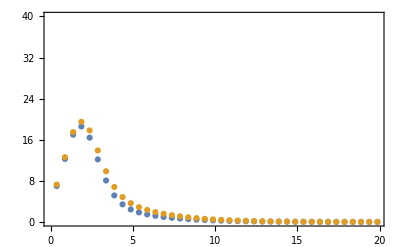

```mathematica
xx=RandomInteger[{1,Length@ls23d}]
ListPlot[{dataT,dataGen[[xx]]},PlotRange->{All,range},Frame->True]
```

### Chi square

```mathematica
(* χ^2 = 2 Sum[ndata - ntrue + ntrue*Log(ntrue/ndata),{i,bin}] *)
```

```mathematica
chis23d=Table[Sum[dataGen[[j,i,2]]-dataT[[i,2]]+dataT[[i,2]]*Log[dataT[[i,2]]/dataGen[[j,i,2]]],{i,40}],{j,Length@dataGen}]//Chop
```

{249.37,67.7919,11.3871,0.0143638,6.38304,16.0289,22.5031,25.7306,29.5343,37.3753,47.0408,246.261,65.21,10.0459,0.128467,7.80133,18.3309,25.1528,28.2486,31.6335,39.0249,48.4422,244.628,63.7778,9.31767,0.247915,8.6877,19.7404,26.7706,29.7903,32.9275,40.0517,49.3227,244.395,63.4138,9.11996,0.289704,8.95857,20.1733,27.2716,30.2705,33.3306,40.3702,49.5972,245.544,64.0963,9.43012,0.230691,8.5903,19.6055,26.6309,29.6637,32.8172,39.9545,49.2404,248.116,65.8602,10.2821,0.104331,7.61586,18.0692,24.8804,28.0013,31.4183,38.8358,48.2835,252.212,68.8012,11.7708,0.00502416,6.12913,15.6579,22.1129,25.3756,29.2257,37.1056,46.8184,258.008,73.09,14.0653,0.101321,4.29812,12.5389,18.4949,21.9524,26.4049,34.9294,45.0109,265.786,78.9978,17.4355,0.662201,2.39109,8.97966,14.2932,17.9977,23.2212,32.5721,43.1263,275.981,86.9468,22.3009,2.106,0.82542,5.39654,9.92295,13.9257,20.088,30.447,41.578,289.281,97.604,29.3244,5.0938,0.260757,2.44775,6.04097,10.3918,17.6595,29.2074,41.0201}

```mathematica
dataSet1=chis23d;
```

### Data AntiNu

```mathematica
(* OS: Win, Linux *)
OS="Linux";
```

```mathematica
(* ModeHE, ModeAntiNu, ModeNu *)
(* Tau_minus, Tau_plus *)
```

```mathematica
mode="AntiNu";sign="plus";
If[mode=="Nu",range=40,range=20];
```

```mathematica
(* Linux *)
```

```mathematica
If[OS=="Linux",data=Import[StringJoin["/home/adriano/Dropbox/Neutrinos/Tau/Data/Mat_WS_In_Mode",mode,"_Tau_",sign,".txt"],"Table"];
data=Table[{.5*i-.25/2,data[[i,2]]},{i,40}];
data2=Import[StringJoin["/home/adriano/Dropbox/Neutrinos/Tau/Data/Mat_WoutS_In_Mode",mode,"_Tau_",sign,".txt"],"Table"];
data2=Table[{.5*i-.25/2,data2[[i,2]]},{i,40}],data=Import[StringJoin["C:\\Users\\Orlando\\Dropbox\\Neutrinos\\Tau\\Data\\Mat_WS_In_Mode",mode,"_Tau_",sign,".txt"],"Table"];
data=Table[{.5*i-.25/2,data[[i,2]]},{i,40}];
data2=Import[StringJoin["C:\\Users\\Orlando\\Dropbox\\Neutrinos\\Tau\\Data\\Mat_WoutS_In_Mode",mode,"_Tau_",sign,".txt"],"Table"];
data2=Table[{.5*i-.25/2,data2[[i,2]]},{i,40}]];
```

### Data of Fig 1 by reconstructed energy

```mathematica
Clear[fs,fn]
fs[Ere_,Etrue_]:=If[Etrue<3.1,0,(*1/(Sqrt[2Pi]σe)*)(Exp[-1/2((Ere-x)/σe)^2]/.{x->b*Etrue,σe->r*Etrue}/.Thread[{b,r}->{.45,.25}])]
fn[Ere_,Etrue_]:=If[Etrue<3.1,0,fs[Ere,Etrue]/NIntegrate[fs[ere,Etrue],{ere,0,20}]]
```

```mathematica
(* dN/Subscript[dE, rec]=∫dN/Subscript[dE, true] P(Subscript[E, rec],Subscript[E, true])ⅆ Subscript[E, true] *)
(* doing numerical integration by cutting the integrand *)
dataT=Table[{data2[[j,1]],Sum[fn[data2[[j,1]],data2[[i,1]]]*0.5*data2[[i,2]],{i,40}]},{j,40}];
(*dataT=Table[{.5*j-.25,Sum[fn[0.5*j-.25,.5*i-.25]*0.5*data2[[i,2]],{i,40}]},{j,40}]//Quiet;*)
dtrue=Interpolation@data2;
ndtrue=NIntegrate[dtrue[x],{x,Min@data[[All,1]],Max@data[[All,1]]}]
dre=Interpolation@data;
ndre=NIntegrate[dre[x],{x,Min@data[[All,1]],Max@data[[All,1]]}]
dreInt=Interpolation@dataT;
ndreInt=NIntegrate[dreInt[x],{x,Min@data[[All,1]],Max@data[[All,1]]}]
fac2=ndtrue/ndreInt
(*dataT=Table[{.5*j-.25,fac2*Sum[fn[0.5*j-.25,.5*i]*0.5*data2[[i,2]],{i,40}]},{j,40}]//Quiet;*)
dataT=Table[{data2[[j,1]],fac2*Sum[fn[data2[[j,1]],data2[[i,1]]]*0.5*data2[[i,2]],{i,40}]},{j,40}];
```

19.775

19.4308

19.0148

1.03998

```mathematica
ListPlot[{data,dataT},Frame->True,PlotRange->{{0,20},{0,40}},AspectRatio->1]
```

-Graphics-

### Creating data with s23 and dm31

```mathematica
(* Subscript[dN, nsi]/Subscript[dE, rec]=∫Subscript[dN, nsi]/Subscript[dE, true] P(Subscript[E, rec],Subscript[E, true])ⅆ Subscript[E, true] =∫(Subscript[P, NSI](μ->τ))/Subscript[P, SM(μ->τ)] Subscript[dN, sm]/Subscript[dE, true] P(Subscript[E, rec],Subscript[E, true])ⅆ Subscript[E, true] *)
```

```mathematica
(* best-fit used {S23,δ} = {0.582,-2.5} *)
```

```mathematica
passos23=.4/10;
passodelta=7./10;
dataGen={};ls23d={};
Clear[delta,ss23];
Do[ss23=(0.582)-.2+passos23*i;
Do[delta=10^-3*(3.5-3.+passodelta*k);AppendTo[ls23d,{ss23,delta}];
AppendTo[dataGen,Table[{data2[[j,1]],Chop[fac2*Sum[fn[data2[[j,1]],data2[[i,1]]]*0.5*data2[[i,2]]*ratioGen[ss23,-2.5,delta,0,.5*i],{i,40}]]},{j,40}]],{k,0,10}],{i,0,10}]//Quiet;
```

```mathematica
Plot[ratioGen[(0.582),del,0,2],{del,-2*Pi,2*Pi}]
```

-Graphics-

```mathematica
dataGen//Dimensions
```

{121,40,2}

83

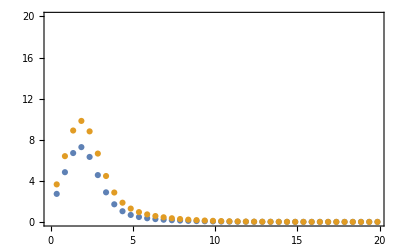

```mathematica
xx=RandomInteger[{1,Length@ls23d}]
ListPlot[{dataT,dataGen[[xx]]},PlotRange->{All,range},Frame->True]
```

### Chi square

```mathematica
(* χ^2 = 2 Sum[ndata - ntrue + ntrue*Log(ntrue/ndata),{i,bin}] *)
```

```mathematica
chis23d=Table[Sum[dataGen[[j,i,2]]-dataT[[i,2]]+dataT[[i,2]]*Log[dataT[[i,2]]/dataGen[[j,i,2]]],{i,40}],{j,Length@dataGen}]//Chop
```

{89.766,24.0636,3.96198,0.00405878,1.99643,4.58368,5.58749,5.42888,6.14881,9.52716,14.0878,88.6363,23.1308,3.48301,0.0433331,2.47517,5.31965,6.35843,6.04226,6.49647,9.61,14.0052,88.0431,22.6135,3.22326,0.0855027,2.77591,5.77301,6.83359,6.42488,6.7216,9.6776,13.9754,87.9586,22.4821,3.15274,0.100353,2.86821,5.91307,6.98199,6.54558,6.79288,9.69867,13.9673,88.3766,22.7286,3.26322,0.0794496,2.74341,5.73095,6.79453,6.39503,6.70086,9.66373,13.9715,89.3114,23.3657,3.56704,0.0349491,2.41348,5.23837,6.28271,5.98453,6.45668,9.58389,13.9993,90.8,24.4283,4.09873,0.00118083,1.91255,4.46924,5.48015,5.34748,6.0936,9.49236,14.0841,92.9068,25.9785,4.91982,0.0394512,1.30169,3.48435,4.4474,4.54415,5.67169,9.44914,14.286,95.734,28.1149,6.12847,0.247602,0.678469,2.38096,3.28135,3.67112,5.28727,9.55046,14.7015,99.44,30.9912,7.8773,0.777811,0.194674,1.31046,2.13296,2.87894,5.09054,9.94636,15.4807,104.275,34.85,10.4075,1.87057,0.090234,0.512172,1.24096,2.40572,5.31915,10.8742,16.8614}

```mathematica
dataSet2=chis23d;
```

### Data High

```mathematica
(* OS: Win, Linux *)
OS="Linux";
```

```mathematica
(* ModeHE, ModeAntiNu, ModeNu *)
(* Tau_minus, Tau_plus *)
```

```mathematica
mode="HE";sign="minus";
If[mode=="Nu",range=40,range=20];
```

```mathematica
(* Linux *)
```

```mathematica
If[OS=="Linux",data=Import[StringJoin["/home/adriano/Dropbox/Neutrinos/Tau/Data/Mat_WS_In_Mode",mode,"_Tau_",sign,".txt"],"Table"];
data=Table[{.5*i-.25/2,data[[i,2]]},{i,40}];
data2=Import[StringJoin["/home/adriano/Dropbox/Neutrinos/Tau/Data/Mat_WoutS_In_Mode",mode,"_Tau_",sign,".txt"],"Table"];
data2=Table[{.5*i-.25/2,data2[[i,2]]},{i,40}],data=Import[StringJoin["C:\\Users\\Orlando\\Dropbox\\Neutrinos\\Tau\\Data\\Mat_WS_In_Mode",mode,"_Tau_",sign,".txt"],"Table"];
data=Table[{.5*i-.25/2,data[[i,2]]},{i,40}];
data2=Import[StringJoin["C:\\Users\\Orlando\\Dropbox\\Neutrinos\\Tau\\Data\\Mat_WoutS_In_Mode",mode,"_Tau_",sign,".txt"],"Table"];
data2=Table[{.5*i-.25/2,data2[[i,2]]},{i,40}]];
```

### Data of Fig 1 by reconstructed energy

```mathematica
Clear[fs,fn]
fs[Ere_,Etrue_]:=If[Etrue<3.1,0,(*1/(Sqrt[2Pi]σe)*)(Exp[-1/2((Ere-x)/σe)^2]/.{x->b*Etrue,σe->r*Etrue}/.Thread[{b,r}->{.45,.25}])]
fn[Ere_,Etrue_]:=If[Etrue<3.1,0,fs[Ere,Etrue]/NIntegrate[fs[ere,Etrue],{ere,0,20}]]
```

```mathematica
(* dN/Subscript[dE, rec]=∫dN/Subscript[dE, true] P(Subscript[E, rec],Subscript[E, true])ⅆ Subscript[E, true] *)
(* doing numerical integration by cutting the integrand *)
dataT=Table[{data2[[j,1]],Sum[fn[data2[[j,1]],data2[[i,1]]]*0.5*data2[[i,2]],{i,40}]},{j,40}];
(*dataT=Table[{.5*j-.25,Sum[fn[0.5*j-.25,.5*i-.25]*0.5*data2[[i,2]],{i,40}]},{j,40}]//Quiet;*)
dtrue=Interpolation@data2;
ndtrue=NIntegrate[dtrue[x],{x,Min@data[[All,1]],Max@data[[All,1]]}]
dre=Interpolation@data;
ndre=NIntegrate[dre[x],{x,Min@data[[All,1]],Max@data[[All,1]]}]
dreInt=Interpolation@dataT;
ndreInt=NIntegrate[dreInt[x],{x,Min@data[[All,1]],Max@data[[All,1]]}]
fac2=ndtrue/ndreInt
(*dataT=Table[{.5*j-.25,fac2*Sum[fn[0.5*j-.25,.5*i]*0.5*data2[[i,2]],{i,40}]},{j,40}]//Quiet;*)
dataT=Table[{data2[[j,1]],fac2*Sum[fn[data2[[j,1]],data2[[i,1]]]*0.5*data2[[i,2]],{i,40}]},{j,40}];
```

77.45

76.1852

75.6044

1.02441

```mathematica
ListPlot[{data,dataT},Frame->True,PlotRange->{{0,20},{0,40}},AspectRatio->1]
```

-Graphics-

### Creating data with s23 and dm31

```mathematica
(* Subscript[dN, nsi]/Subscript[dE, rec]=∫Subscript[dN, nsi]/Subscript[dE, true] P(Subscript[E, rec],Subscript[E, true])ⅆ Subscript[E, true] =∫(Subscript[P, NSI](μ->τ))/Subscript[P, SM(μ->τ)] Subscript[dN, sm]/Subscript[dE, true] P(Subscript[E, rec],Subscript[E, true])ⅆ Subscript[E, true] *)
```

```mathematica
(* best-fit used {S23,δ} = {0.582,-2.5} *)
```

```mathematica
passos23=.4/10;
passodelta=7./10;
dataGen={};ls23d={};
Clear[delta,ss23];
Do[ss23=(0.582)-.2+passos23*i;
Do[delta=10^-3*(3.5-3.+passodelta*k);AppendTo[ls23d,{ss23,delta}];
AppendTo[dataGen,Table[{data2[[j,1]],Chop[fac2*Sum[fn[data2[[j,1]],data2[[i,1]]]*0.5*data2[[i,2]]*ratioGen[ss23,-2.5,delta,0,.5*i],{i,40}]]},{j,40}]],{k,0,10}],{i,0,10}]//Quiet;
```

```mathematica
Plot[ratioGen[(0.582),del,0,2],{del,-2*Pi,2*Pi}]
```

-Graphics-

```mathematica
dataGen//Dimensions
```

{121,40,2}

24

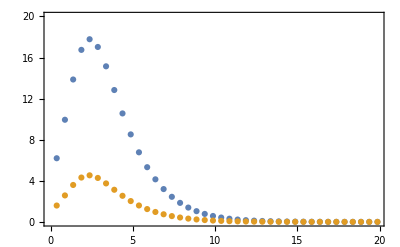

```mathematica
xx=RandomInteger[{1,Length@ls23d}]
ListPlot[{dataT,dataGen[[xx]]},PlotRange->{All,range},Frame->True]
```

### Chi square

```mathematica
(* χ^2 = 2 Sum[ndata - ntrue + ntrue*Log(ntrue/ndata),{i,bin}] *)
```

```mathematica
chis23d=Table[Sum[dataGen[[j,i,2]]-dataT[[i,2]]+dataT[[i,2]]*Log[dataT[[i,2]]/dataGen[[j,i,2]]],{i,40}],{j,Length@dataGen}]//Chop
```

{369.707,107.314,19.6161,0.0441872,15.4245,47.0651,82.5779,114.063,137.37,151.327,156.751,365.308,103.556,17.5547,0.248358,18.1362,52.2232,89.8721,123.017,147.437,161.974,167.521,362.996,101.469,16.4292,0.441379,19.8008,55.3298,94.2418,128.371,153.454,168.338,173.962,362.664,100.938,16.1237,0.506953,20.3016,56.2678,95.5695,130.008,155.302,170.3,175.955,364.285,101.934,16.6065,0.412873,19.6061,55.0044,93.8218,127.892,152.946,167.826,173.464,367.918,104.504,17.9252,0.206469,17.7614,51.5862,89.0453,122.07,146.433,160.961,166.534,373.702,108.784,20.2133,0.0207224,14.9001,46.1458,81.3717,112.675,135.893,149.834,155.296,381.888,115.013,23.7085,0.0928584,11.2591,38.9196,71.0373,99.9398,121.561,134.681,139.983,392.869,123.572,28.7901,0.801289,7.21645,30.2852,58.4191,84.2426,103.813,115.877,120.97,407.258,135.055,36.0478,2.73441,3.35977,20.8295,44.1033,66.1687,83.2345,94.006,98.8407,426.021,150.398,46.4131,6.82189,0.617566,11.4802,29.0166,46.6434,60.7488,69.991,74.5171}

```mathematica
dataSet3=chis23d;
```

### Data

```mathematica
ls23d
```

{{0.382,0.0005},{0.382,0.0012},{0.382,0.0019},{0.382,0.0026},{0.382,0.0033},{0.382,0.004},{0.382,0.0047},{0.382,0.0054},{0.382,0.0061},{0.382,0.0068},{0.382,0.0075},{0.422,0.0005},{0.422,0.0012},{0.422,0.0019},{0.422,0.0026},{0.422,0.0033},{0.422,0.004},{0.422,0.0047},{0.422,0.0054},{0.422,0.0061},{0.422,0.0068},{0.422,0.0075},{0.462,0.0005},{0.462,0.0012},{0.462,0.0019},{0.462,0.0026},{0.462,0.0033},{0.462,0.004},{0.462,0.0047},{0.462,0.0054},{0.462,0.0061},{0.462,0.0068},{0.462,0.0075},{0.502,0.0005},{0.502,0.0012},{0.502,0.0019},{0.502,0.0026},{0.502,0.0033},{0.502,0.004},{0.502,0.0047},{0.502,0.0054},{0.502,0.0061},{0.502,0.0068},{0.502,0.0075},{0.542,0.0005},{0.542,0.0012},{0.542,0.0019},{0.542,0.0026},{0.542,0.0033},{0.542,0.004},{0.542,0.0047},{0.542,0.0054},{0.542,0.0061},{0.542,0.0068},{0.542,0.0075},{0.582,0.0005},{0.582,0.0012},{0.582,0.0019},{0.582,0.0026},{0.582,0.0033},{0.582,0.004},{0.582,0.0047},{0.582,0.0054},{0.582,0.0061},{0.582,0.0068},{0.582,0.0075},{0.622,0.0005},{0.622,0.0012},{0.622,0.0019},{0.622,0.0026},{0.622,0.0033},{0.622,0.004},{0.622,0.0047},{0.622,0.0054},{0.622,0.0061},{0.622,0.0068},{0.622,0.0075},{0.662,0.0005},{0.662,0.0012},{0.662,0.0019},{0.662,0.0026},{0.662,0.0033},{0.662,0.004},{0.662,0.0047},{0.662,0.0054},{0.662,0.0061},{0.662,0.0068},{0.662,0.0075},{0.702,0.0005},{0.702,0.0012},{0.702,0.0019},{0.702,0.0026},{0.702,0.0033},{0.702,0.004},{0.702,0.0047},{0.702,0.0054},{0.702,0.0061},{0.702,0.0068},{0.702,0.0075},{0.742,0.0005},{0.742,0.0012},{0.742,0.0019},{0.742,0.0026},{0.742,0.0033},{0.742,0.004},{0.742,0.0047},{0.742,0.0054},{0.742,0.0061},{0.742,0.0068},{0.742,0.0075},{0.782,0.0005},{0.782,0.0012},{0.782,0.0019},{0.782,0.0026},{0.782,0.0033},{0.782,0.004},{0.782,0.0047},{0.782,0.0054},{0.782,0.0061},{0.782,0.0068},{0.782,0.0075}}

```mathematica
dataSet1
```

{249.37,67.7919,11.3871,0.0143638,6.38304,16.0289,22.5031,25.7306,29.5343,37.3753,47.0408,246.261,65.21,10.0459,0.128467,7.80133,18.3309,25.1528,28.2486,31.6335,39.0249,48.4422,244.628,63.7778,9.31767,0.247915,8.6877,19.7404,26.7706,29.7903,32.9275,40.0517,49.3227,244.395,63.4138,9.11996,0.289704,8.95857,20.1733,27.2716,30.2705,33.3306,40.3702,49.5972,245.544,64.0963,9.43012,0.230691,8.5903,19.6055,26.6309,29.6637,32.8172,39.9545,49.2404,248.116,65.8602,10.2821,0.104331,7.61586,18.0692,24.8804,28.0013,31.4183,38.8358,48.2835,252.212,68.8012,11.7708,0.00502416,6.12913,15.6579,22.1129,25.3756,29.2257,37.1056,46.8184,258.008,73.09,14.0653,0.101321,4.29812,12.5389,18.4949,21.9524,26.4049,34.9294,45.0109,265.786,78.9978,17.4355,0.662201,2.39109,8.97966,14.2932,17.9977,23.2212,32.5721,43.1263,275.981,86.9468,22.3009,2.106,0.82542,5.39654,9.92295,13.9257,20.088,30.447,41.578,289.281,97.604,29.3244,5.0938,0.260757,2.44775,6.04097,10.3918,17.6595,29.2074,41.0201}

```mathematica
dataSet2
```

{89.766,24.0636,3.96198,0.00405878,1.99643,4.58368,5.58749,5.42888,6.14881,9.52716,14.0878,88.6363,23.1308,3.48301,0.0433331,2.47517,5.31965,6.35843,6.04226,6.49647,9.61,14.0052,88.0431,22.6135,3.22326,0.0855027,2.77591,5.77301,6.83359,6.42488,6.7216,9.6776,13.9754,87.9586,22.4821,3.15274,0.100353,2.86821,5.91307,6.98199,6.54558,6.79288,9.69867,13.9673,88.3766,22.7286,3.26322,0.0794496,2.74341,5.73095,6.79453,6.39503,6.70086,9.66373,13.9715,89.3114,23.3657,3.56704,0.0349491,2.41348,5.23837,6.28271,5.98453,6.45668,9.58389,13.9993,90.8,24.4283,4.09873,0.00118083,1.91255,4.46924,5.48015,5.34748,6.0936,9.49236,14.0841,92.9068,25.9785,4.91982,0.0394512,1.30169,3.48435,4.4474,4.54415,5.67169,9.44914,14.286,95.734,28.1149,6.12847,0.247602,0.678469,2.38096,3.28135,3.67112,5.28727,9.55046,14.7015,99.44,30.9912,7.8773,0.777811,0.194674,1.31046,2.13296,2.87894,5.09054,9.94636,15.4807,104.275,34.85,10.4075,1.87057,0.090234,0.512172,1.24096,2.40572,5.31915,10.8742,16.8614}

```mathematica
dataSet3
```

{369.707,107.314,19.6161,0.0441872,15.4245,47.0651,82.5779,114.063,137.37,151.327,156.751,365.308,103.556,17.5547,0.248358,18.1362,52.2232,89.8721,123.017,147.437,161.974,167.521,362.996,101.469,16.4292,0.441379,19.8008,55.3298,94.2418,128.371,153.454,168.338,173.962,362.664,100.938,16.1237,0.506953,20.3016,56.2678,95.5695,130.008,155.302,170.3,175.955,364.285,101.934,16.6065,0.412873,19.6061,55.0044,93.8218,127.892,152.946,167.826,173.464,367.918,104.504,17.9252,0.206469,17.7614,51.5862,89.0453,122.07,146.433,160.961,166.534,373.702,108.784,20.2133,0.0207224,14.9001,46.1458,81.3717,112.675,135.893,149.834,155.296,381.888,115.013,23.7085,0.0928584,11.2591,38.9196,71.0373,99.9398,121.561,134.681,139.983,392.869,123.572,28.7901,0.801289,7.21645,30.2852,58.4191,84.2426,103.813,115.877,120.97,407.258,135.055,36.0478,2.73441,3.35977,20.8295,44.1033,66.1687,83.2345,94.006,98.8407,426.021,150.398,46.4131,6.82189,0.617566,11.4802,29.0166,46.6434,60.7488,69.991,74.5171}

### Contour

```mathematica
dataSet=dataSet1+dataSet2+dataSet3;
```

InterpolatingFunction[…]

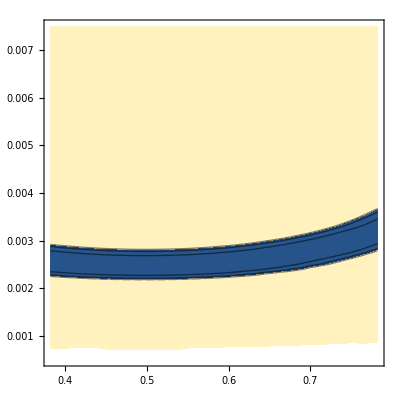

```mathematica
Table[{ls23d[[i]],{dataSet[[i]]}},{i,Length@ls23d}];
func=Interpolation@%
ContourPlot[func[s23,del],{s23,Min@ls23d[[All,1]],Max@ls23d[[All,1]]},{del,Min@ls23d[[All,2]],Max@ls23d[[All,2]]},Contours->{2.3,4.6,6.}]
```

```mathematica
f[S23_]=2*Sqrt[S23]*Sqrt[1-S23];
```

```mathematica
(* sin^2(2θ) = 2 sin(θ)cos(θ) *)
```

```mathematica
Ls23d=MapAt[f,ls23d,{{All,1}}];
```

InterpolatingFunction[…]

InterpolatingFunction::dmval: Input value {0.0000714286,0.0005005} lies outside the range of data in the interpolating function. Extrapolation will be used.

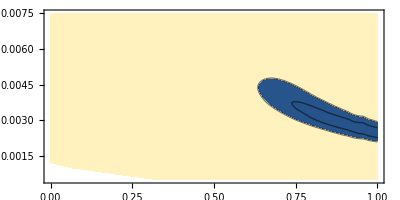

```mathematica
Table[{Ls23d[[i]],{dataSet[[i]]}},{i,Length@ls23d}];
func=Interpolation@%
ContourPlot[func[s23,del],{s23,0,1},{del,Min@Ls23d[[All,2]],Max@Ls23d[[All,2]]},Contours->{2.3,11.3},AspectRatio->1/2]
```

```mathematica
(* compare with fig5 *)
```

```mathematica
(* In this plot, all the other parameters are fixed. In the paper, some of the parameters are marginalized over, so the region increases *)
```

## All data sets - NSI

### Data Nu

```mathematica
(* OS: Win, Linux *)
OS="Win";
```

```mathematica
(* ModeHE, ModeAntiNu, ModeNu *)
(* Tau_minus, Tau_plus *)
```

```mathematica
mode="Nu";sign="minus";
If[mode=="Nu",range=40,range=20];
```

```mathematica
(* Linux *)
```

```mathematica
If[OS=="Linux",data=Import[StringJoin["/home/adriano/Dropbox/Neutrinos/Tau/Data/Mat_WS_In_Mode",mode,"_Tau_",sign,".txt"],"Table"];
data=Table[{.5*i-.25/2,data[[i,2]]},{i,40}];
data2=Import[StringJoin["/home/adriano/Dropbox/Neutrinos/Tau/Data/Mat_WoutS_In_Mode",mode,"_Tau_",sign,".txt"],"Table"];
data2=Table[{.5*i-.25/2,data2[[i,2]]},{i,40}];
bg=Import[StringJoin["/home/adriano/Dropbox/Neutrinos/Tau/Data/Mat_WS_In_Mode",mode,"_BG.txt"],"Table"];
bg=Table[{.5*i-.25/2,bg[[i,2]]},{i,40}],data=Import[StringJoin["C:\\Users\\Orlando\\Dropbox\\Neutrinos\\Tau\\Data\\Mat_WS_In_Mode",mode,"_Tau_",sign,".txt"],"Table"];
data=Table[{.5*i-.25/2,data[[i,2]]},{i,40}];
data2=Import[StringJoin["C:\\Users\\Orlando\\Dropbox\\Neutrinos\\Tau\\Data\\Mat_WoutS_In_Mode",mode,"_Tau_",sign,".txt"],"Table"];
data2=Table[{.5*i-.25/2,data2[[i,2]]},{i,40}];bg=Import[StringJoin["C:\\Users\\Orlando\\Dropbox\\Neutrinos\\Tau\\Data\\Mat_WS_In_Mode",mode,"_BG.txt"],"Table"];
bg=Table[{.5*i-.25/2,bg[[i,2]]},{i,40}]];
```

### Data of Fig 1 by reconstructed energy

```mathematica
Clear[fs,fn]
fs[Ere_,Etrue_]:=If[Etrue<3.1,0,(*1/(Sqrt[2Pi]σe)*)(Exp[-1/2((Ere-x)/σe)^2]/.{x->b*Etrue,σe->r*Etrue}/.Thread[{b,r}->{.45,.25}])]
fn[Ere_,Etrue_]:=If[Etrue<3.1,0,fs[Ere,Etrue]/NIntegrate[fs[ere,Etrue],{ere,0,20}]]
```

```mathematica
(* dN/Subscript[dE, rec]=∫dN/Subscript[dE, true] P(Subscript[E, rec],Subscript[E, true])ⅆ Subscript[E, true] *)
(* doing numerical integration by cutting the integrand *)
dataT=Table[{data2[[j,1]],Sum[fn[data2[[j,1]],data2[[i,1]]]*0.5*data2[[i,2]],{i,40}]},{j,40}];
(*dataT=Table[{.5*j-.25,Sum[fn[0.5*j-.25,.5*i-.25]*0.5*data2[[i,2]],{i,40}]},{j,40}]//Quiet;*)
dtrue=Interpolation@data2;
ndtrue=NIntegrate[dtrue[x],{x,Min@data[[All,1]],Max@data[[All,1]]}]
dre=Interpolation@data;
ndre=NIntegrate[dre[x],{x,Min@data[[All,1]],Max@data[[All,1]]}]
dreInt=Interpolation@dataT;
ndreInt=NIntegrate[dreInt[x],{x,Min@data[[All,1]],Max@data[[All,1]]}]
fac2=ndtrue/ndreInt
(*dataT=Table[{.5*j-.25,fac2*Sum[fn[0.5*j-.25,.5*i]*0.5*data2[[i,2]],{i,40}]},{j,40}]//Quiet;*)
dataT=Table[{data2[[j,1]],fac2*Sum[fn[data2[[j,1]],data2[[i,1]]]*0.5*data2[[i,2]],{i,40}]},{j,40}];
```

54.4842

53.3873

52.517

1.03746

```mathematica
ListPlot[{data,dataT},Frame->True,PlotRange->{{0,20},{0,40}},AspectRatio->1]
```

-Graphics-

```mathematica
sinal=Table[{bg[[i,1]],bg[[i,2]]+dataT[[i,2]]},{i,Length@bg}];
```

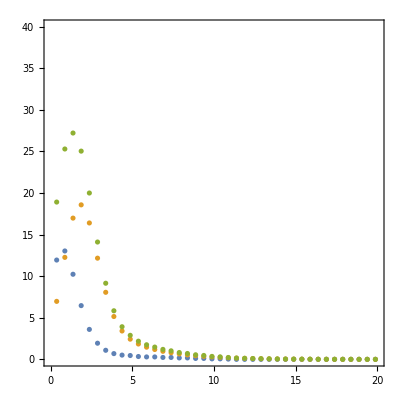

```mathematica
ListPlot[{bg,dataT,sinal},Frame->True,PlotRange->{{0,20},{0,40}},AspectRatio->1]
```

```mathematica
dataTrue=dataT;
```

### General Probability ratio

```mathematica
ratioGen[S23_,δ_,epS_,ee_]=(ee (-537.0144158815365 s23^2+(95.922402136029-4.114998188599089 ee) ee s23^2+(537.0144158815365+ee (-95.92240213602899+4.114998188599089 ee)) s23^4+epS^2 (-194626.6461383849+(34963.71557858255-1499.9168397443682 ee) ee+382355.29126830207 s23^2+ee (-69927.4311571651+2999.8336794887364 ee) s23^2+(-391483.50917764+(69927.4311571651-2999.8336794887364 ee) ee) s23^4)+epS s23 √(1-s23^2) (14161.307084011187-28998.778457602955 s23^2+ee (-2589.904857672781+5179.809715345562 s23^2+ee (111.1049510921754-222.2099021843508 s23^2))))-2536.820066237314 epS s23 √(1-s23^2) Sin[8.323065282815573/ee]+1119.5858672098655 ee epS s23 √(1-s23^2) Sin[8.323065282815573/ee]-39.38853098975155 ee^2 epS s23 √(1-s23^2) Sin[8.323065282815573/ee]+5073.640132474628 epS s23^3 √(1-s23^2) Sin[8.323065282815573/ee]-1796.3230913768598 ee epS s23^3 √(1-s23^2) Sin[8.323065282815573/ee]+78.7770619795031 ee^2 epS s23^3 √(1-s23^2) Sin[8.323065282815573/ee]+Cos[δ] (s23 (epS s23 (261.20978051393564-348.27970735191445 s23^2)+4701.776049250849 epS^2 s23^2 √(1-s23^2)-6.44962421022064 √(1-s23^2) (-0.5+1. s23^2))+ee s23 (-403.4052420503069 epS^2 s23^2 √(1-s23^2)+0.5533679589167451 √(1-s23^2) (-0.4999999999999999+1. s23^2)+epS s23 (-22.411402336128184+29.881869781504182 s23^2))+ee^3 (-0.03334587340666304 √(1-s23^2) (-0.5 s23+1. s23^3)+24.30914171345736 epS^2 √(1-s23^2) (-0.5 s23+1. s23^3)+epS (-0.22508464549497562+1.8006771639598036 s23^2-1.800677163959804 s23^4))+ee^2 (0.38865342484877047 √(1-s23^2) (-0.5 s23+1. s23^3)-283.3283467147537 epS^2 √(1-s23^2) (-0.5 s23+1. s23^3)+epS (2.623410617729201-20.987284941833607 s23^2+20.987284941833604 s23^4))+s23 (epS^2 √(1-s23^2) (-12603.870244016523+1081.3929190371105 ee+12603.870244016523 s23^2-1081.3929190371105 ee s23^2)+√(1-s23^2) (8.644629796993499-0.7416961035919825 ee-17.289259593986998 s23^2+1.483392207183965 ee s23^2)+epS s23 (1167.0250225941222-100.12897398491762 ee-933.6200180752978 s23^2+80.1031791879341 ee s23^2)) Sin[8.323065282815573/ee])-8.644629796993499 s23 √(1-s23^2) Sin[δ]+0.7416961035919825 ee s23 √(1-s23^2) Sin[δ]+3.2248121051103213 s23 √(1-s23^2) Sin[8.323065282815573/ee] Sin[δ]-0.2766839794583725 ee s23 √(1-s23^2) Sin[8.323065282815573/ee] Sin[δ]+Sin[8.323065282815573/ee] (-5978.45668107876 ee epS^2+(93.95629874953016-68494.14178840749 epS^2+ee (-33.26524243290481+1.4588344811019092 ee+30228.81841466637 epS^2-1063.4903367232919 ee epS^2)) s23^2+(-93.95629874953016+68494.14178840749 epS^2+ee (33.26524243290481-1.4588344811019092 ee-24250.361733587608 epS^2+1063.4903367232919 ee epS^2)) s23^4+(87.06992683797868-7.470467445376055 ee) epS s23^2 Sin[δ])+Cos[8.323065282815573/ee] (ee ((537.0144158815365+ee (-95.92240213602898+4.114998188599088 ee)) s23^2+(-537.0144158815365+(95.92240213602898-4.114998188599088 ee) ee) s23^4+epS^2 (-6898.001008467854+(-384585.5081691722+(69927.43115716509-2999.8336794887364 ee) ee) s23^2+(391483.50917764+ee (-69927.4311571651+2999.8336794887364 ee)) s23^4)+epS s23 √(1-s23^2) (-14243.90770996934+28998.778457602955 s23^2+ee (2589.904857672781-5179.809715345562 s23^2+ee (-111.1049510921754+222.2099021843508 s23^2))))+s23 (epS s23 (-435.3496341898932+ee (37.352337226880266+(20.987284941833604-1.8006771639598043 ee) ee)+(348.2797073519141+ee (-29.881869781504264+ee (-20.987284941833607+1.800677163959804 ee))) s23^2)+epS^2 √(1-s23^2) (4701.776049250852-4701.776049250846 s23^2+ee (-403.4052420503069+403.4052420503069 s23^2+ee (-141.66417335737682+12.15457085672868 ee+283.3283467147537 s23^2-24.30914171345736 ee s23^2)))+√(1-s23^2) (-3.224812105110321+6.449624210220642 s23^2+ee (0.27668397945837264-0.553367958916745 s23^2+ee (0.19432671242438523-0.01667293670333152 ee-0.38865342484877047 s23^2+0.03334587340666304 ee s23^2)))) Cos[δ]+s23 ((233.40500451882428-20.025794796983522 ee) epS s23-0.7416961035919825 (-11.65521802680122+1. ee) √(1-s23^2)) Sin[δ])+epS ((87.06992683797863+ee (-7.4704674453760544+(-2.623410617729201+0.22508464549497553 ee) ee)) Cos[8.323065282815573/ee+δ]+2.842170943040401*^-14 Sin[8.323065282815573/ee-δ]+(-233.40500451882443+20.025794796983533 ee) s23^2 Sin[δ]+(-233.40500451882437+20.025794796983526 ee) Sin[8.323065282815573/ee+δ]))/(2.7607421580402205+ee (-130.8796094130282+(23.3230292223281-1. ee) ee)+(-2.76074215804022+ee (130.87960941302822+ee (-23.323029222328106+1. ee))) Cos[8.323065282815573/ee]+(22.46560935192947+(-8.05902865451455+0.3548994794121858 ee) ee) Sin[8.323065282815573/ee])/.s23->Sqrt[S23];
```

### Creating data with NSI

```mathematica
(* Subscript[dN, nsi]/Subscript[dE, rec]=∫Subscript[dN, nsi]/Subscript[dE, true] P(Subscript[E, rec],Subscript[E, true])ⅆ Subscript[E, true] =∫(Subscript[P, NSI](μ->τ))/Subscript[P, SM(μ->τ)] Subscript[dN, sm]/Subscript[dE, true] P(Subscript[E, rec],Subscript[E, true])ⅆ Subscript[E, true] *)
```

```mathematica
(* best-fit used {S23,δ} = {0.582,-2.5} *)
```

```mathematica
passoNSI=4./20;
dataGen={};ls23d={};
Clear[delta,ss23];
Do[delta=(-2.+passoNSI*k)*10^-2;AppendTo[ls23d,{delta}];
AppendTo[dataGen,Table[{data2[[j,1]],fac2*Sum[fn[data2[[j,1]],data2[[i,1]]]*0.5*data2[[i,2]]*ratioGen[0.582,-2.5,delta,.5*i],{i,40}]},{j,40}]],{k,0,20}];
```

```mathematica
dataGen//Dimensions
```

{21,40,2}

7

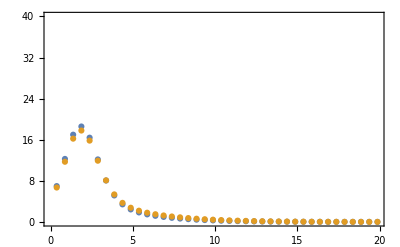

```mathematica
xx=RandomInteger[{1,Length@ls23d}]
ListPlot[{dataT,dataGen[[xx]]},PlotRange->{All,range},Frame->True]
```

### Chi square

```mathematica
(* χ^2 = 2 Sum[nteo - ndata + ndata*Log(ndata/nteo),{i,bin}] *)
```

```mathematica
(* data is SM *)
```

```mathematica
(* without bg *)
```

```mathematica
(* for 3.5 years *)
```

```mathematica
chis23d=Table[2*Sum[(dataGen[[j,i,2]])-(dataTrue[[i,2]])+(dataTrue[[i,2]])*Log[(dataTrue[[i,2]])/(dataGen[[j,i,2]])],{i,40}],{j,Length@dataGen}]//Chop
```

{28.3962,20.0561,13.473,8.48504,4.90884,2.53512,1.12547,0.41493,0.129763,0.033219,0,0.0851642,0.530114,1.69353,3.96106,7.68465,13.1592,20.622,30.2605,42.2222,56.6229}

```mathematica
(* for 3.0 years *)
```

```mathematica
years=3/3.5;
```

```mathematica
chis23d=Table[2*Sum[(years*dataGen[[j,i,2]])-(years*dataTrue[[i,2]])+(years*dataTrue[[i,2]])*Log[(dataTrue[[i,2]])/(dataGen[[j,i,2]])],{i,40}],{j,Length@dataGen}]//Chop
```

{24.3396,17.191,11.5483,7.27289,4.20758,2.17296,0.964689,0.355655,0.111226,0.0284734,0,0.0729979,0.454383,1.4516,3.3952,6.58685,11.2793,17.676,25.9376,36.1904,48.534}

```mathematica
(* with bg *)
```

```mathematica
(* for 3.5 years *)
```

```mathematica
chis23dbg=Table[2*Sum[(dataGen[[j,i,2]]+(1+27^2*ls23d[[j,1]]^2)*(1+α)*bg[[i,2]])-(dataTrue[[i,2]]+bg[[i,2]])+(dataTrue[[i,2]]+bg[[i,2]])*Log[(dataTrue[[i,2]]+bg[[i,2]])/(dataGen[[j,i,2]]+(1+27^2*ls23d[[j,1]]^2)*(1+α)*bg[[i,2]])],{i,40}]+(α/0.25)^2,{j,Length@dataGen},{α,-.5,.5,.05}]//Chop;
```

```mathematica
Table[α,{α,-.5,.5,.05}];
Table[i,{i,Length@%}];
la=Thread[%->%%]
```

{1→-0.5,2→-0.45,3→-0.4,4→-0.35,5→-0.3,6→-0.25,7→-0.2,8→-0.15,9→-0.1,10→-0.05,11→0.,12→0.05,13→0.1,14→0.15,15→0.2,16→0.25,17→0.3,18→0.35,19→0.4,20→0.45,21→0.5}

```mathematica
Min/@chis23dbg
(Table[Position[chis23dbg[[i]],%[[i]]],{i,Length@chis23dbg}]//Flatten)/.la
```

{26.7438,18.8169,12.5569,7.8262,4.46343,2.23905,0.940361,0.305468,0.0803148,0.0203945,0,0.0693769,0.349385,1.1892,2.90543,5.81323,10.1929,16.2781,24.2095,34.1355,46.1896}

{-0.25,-0.2,-0.15,-0.1,-0.05,-0.05,0.,0.,0.,0.,0.,0.,-0.05,-0.1,-0.15,-0.2,-0.25,-0.3,-0.4,-0.45,-0.5}

```mathematica
chis23dbg=Min/@chis23dbg;
```

```mathematica
(* for 3.0 years *)
```

```mathematica
years=3/3.5;
```

```mathematica
chis23dbg=Table[2*Sum[years*(dataGen[[j,i,2]]+(1+27^2*ls23d[[j,1]]^2)*(1+α)*bg[[i,2]])-years*(dataTrue[[i,2]]+bg[[i,2]])+years*(dataTrue[[i,2]]+bg[[i,2]])*Log[(dataTrue[[i,2]]+bg[[i,2]])/(dataGen[[j,i,2]]+(1+27^2*ls23d[[j,1]]^2)*(1+α)*bg[[i,2]])],{i,40}]+(α/0.25)^2,{j,Length@dataGen},{α,-.5,.5,.05}]//Chop;
```

```mathematica
Table[α,{α,-.5,.5,.05}];
Table[i,{i,Length@%}];
la=Thread[%->%%]
```

{1→-0.5,2→-0.45,3→-0.4,4→-0.35,5→-0.3,6→-0.25,7→-0.2,8→-0.15,9→-0.1,10→-0.05,11→0.,12→0.05,13→0.1,14→0.15,15→0.2,16→0.25,17→0.3,18→0.35,19→0.4,20→0.45,21→0.5}

```mathematica
Min/@chis23dbg
(Table[Position[chis23dbg[[i]],%[[i]]],{i,Length@chis23dbg}]//Flatten)/.la
```

{23.0661,16.2202,10.8145,6.73103,3.83151,1.9249,0.806023,0.26183,0.0688413,0.017481,0,0.059466,0.305187,1.04217,2.5418,5.07419,8.87964,14.1583,21.0703,29.7219,40.1625}

{-0.25,-0.2,-0.15,-0.1,-0.05,-0.05,0.,0.,0.,0.,0.,0.,-0.05,-0.1,-0.15,-0.2,-0.25,-0.3,-0.35,-0.45,-0.5}

```mathematica
chis23dbg=Min/@chis23dbg;
```

### chi2 data

```mathematica
dataSet1=chis23d;
dataSet1bg=chis23dbg;
```

### Data AntiNu

```mathematica
(* OS: Win, Linux *)
OS="Win";
```

```mathematica
(* ModeHE, ModeAntiNu, ModeNu *)
(* Tau_minus, Tau_plus *)
```

```mathematica
mode="AntiNu";sign="minus";
If[mode=="Nu",range=40,range=20];
```

```mathematica
(* Linux *)
```

```mathematica
If[OS=="Linux",data=Import[StringJoin["/home/adriano/Dropbox/Neutrinos/Tau/Data/Mat_WS_In_Mode",mode,"_Tau_",sign,".txt"],"Table"];
data=Table[{.5*i-.25/2,data[[i,2]]},{i,40}];
data2=Import[StringJoin["/home/adriano/Dropbox/Neutrinos/Tau/Data/Mat_WoutS_In_Mode",mode,"_Tau_",sign,".txt"],"Table"];
data2=Table[{.5*i-.25/2,data2[[i,2]]},{i,40}];
bg=Import[StringJoin["/home/adriano/Dropbox/Neutrinos/Tau/Data/Mat_WS_In_Mode",mode,"_BG.txt"],"Table"];
bg=Table[{.5*i-.25/2,bg[[i,2]]},{i,40}],data=Import[StringJoin["C:\\Users\\Orlando\\Dropbox\\Neutrinos\\Tau\\Data\\Mat_WS_In_Mode",mode,"_Tau_",sign,".txt"],"Table"];
data=Table[{.5*i-.25/2,data[[i,2]]},{i,40}];
data2=Import[StringJoin["C:\\Users\\Orlando\\Dropbox\\Neutrinos\\Tau\\Data\\Mat_WoutS_In_Mode",mode,"_Tau_",sign,".txt"],"Table"];
data2=Table[{.5*i-.25/2,data2[[i,2]]},{i,40}];bg=Import[StringJoin["C:\\Users\\Orlando\\Dropbox\\Neutrinos\\Tau\\Data\\Mat_WS_In_Mode",mode,"_BG.txt"],"Table"];
bg=Table[{.5*i-.25/2,bg[[i,2]]},{i,40}]];
```

### Data of Fig 1 by reconstructed energy

```mathematica
Clear[fs,fn]
fs[Ere_,Etrue_]:=If[Etrue<3.1,0,(*1/(Sqrt[2Pi]σe)*)(Exp[-1/2((Ere-x)/σe)^2]/.{x->b*Etrue,σe->r*Etrue}/.Thread[{b,r}->{.45,.25}])]
fn[Ere_,Etrue_]:=If[Etrue<3.1,0,fs[Ere,Etrue]/NIntegrate[fs[ere,Etrue],{ere,0,20}]]
```

```mathematica
(* dN/Subscript[dE, rec]=∫dN/Subscript[dE, true] P(Subscript[E, rec],Subscript[E, true])ⅆ Subscript[E, true] *)
(* doing numerical integration by cutting the integrand *)
dataT=Table[{data2[[j,1]],Sum[fn[data2[[j,1]],data2[[i,1]]]*0.5*data2[[i,2]],{i,40}]},{j,40}];
(*dataT=Table[{.5*j-.25,Sum[fn[0.5*j-.25,.5*i-.25]*0.5*data2[[i,2]],{i,40}]},{j,40}]//Quiet;*)
dtrue=Interpolation@data2;
ndtrue=NIntegrate[dtrue[x],{x,Min@data[[All,1]],Max@data[[All,1]]}]
dre=Interpolation@data;
ndre=NIntegrate[dre[x],{x,Min@data[[All,1]],Max@data[[All,1]]}]
dreInt=Interpolation@dataT;
ndreInt=NIntegrate[dreInt[x],{x,Min@data[[All,1]],Max@data[[All,1]]}]
fac2=ndtrue/ndreInt
(*dataT=Table[{.5*j-.25,fac2*Sum[fn[0.5*j-.25,.5*i]*0.5*data2[[i,2]],{i,40}]},{j,40}]//Quiet;*)
dataT=Table[{data2[[j,1]],fac2*Sum[fn[data2[[j,1]],data2[[i,1]]]*0.5*data2[[i,2]],{i,40}]},{j,40}];
```

13.1906

12.9894

12.8561

1.02602

```mathematica
ListPlot[{data,dataT},Frame->True,PlotRange->{{0,20},{0,40}},AspectRatio->1]
```

-Graphics-

```mathematica
dataTrue=dataT;
```

### General Probability ratio

```mathematica
ratioGen[S23_,δ_,epS_,ee_]=(ee (-537.0144158815365 s23^2+(95.922402136029-4.114998188599089 ee) ee s23^2+(537.0144158815365+ee (-95.92240213602899+4.114998188599089 ee)) s23^4+epS^2 (-194626.6461383849+(34963.71557858255-1499.9168397443682 ee) ee+382355.29126830207 s23^2+ee (-69927.4311571651+2999.8336794887364 ee) s23^2+(-391483.50917764+(69927.4311571651-2999.8336794887364 ee) ee) s23^4)+epS s23 √(1-s23^2) (14161.307084011187-28998.778457602955 s23^2+ee (-2589.904857672781+5179.809715345562 s23^2+ee (111.1049510921754-222.2099021843508 s23^2))))-2536.820066237314 epS s23 √(1-s23^2) Sin[8.323065282815573/ee]+1119.5858672098655 ee epS s23 √(1-s23^2) Sin[8.323065282815573/ee]-39.38853098975155 ee^2 epS s23 √(1-s23^2) Sin[8.323065282815573/ee]+5073.640132474628 epS s23^3 √(1-s23^2) Sin[8.323065282815573/ee]-1796.3230913768598 ee epS s23^3 √(1-s23^2) Sin[8.323065282815573/ee]+78.7770619795031 ee^2 epS s23^3 √(1-s23^2) Sin[8.323065282815573/ee]+Cos[δ] (s23 (epS s23 (261.20978051393564-348.27970735191445 s23^2)+4701.776049250849 epS^2 s23^2 √(1-s23^2)-6.44962421022064 √(1-s23^2) (-0.5+1. s23^2))+ee s23 (-403.4052420503069 epS^2 s23^2 √(1-s23^2)+0.5533679589167451 √(1-s23^2) (-0.4999999999999999+1. s23^2)+epS s23 (-22.411402336128184+29.881869781504182 s23^2))+ee^3 (-0.03334587340666304 √(1-s23^2) (-0.5 s23+1. s23^3)+24.30914171345736 epS^2 √(1-s23^2) (-0.5 s23+1. s23^3)+epS (-0.22508464549497562+1.8006771639598036 s23^2-1.800677163959804 s23^4))+ee^2 (0.38865342484877047 √(1-s23^2) (-0.5 s23+1. s23^3)-283.3283467147537 epS^2 √(1-s23^2) (-0.5 s23+1. s23^3)+epS (2.623410617729201-20.987284941833607 s23^2+20.987284941833604 s23^4))+s23 (epS^2 √(1-s23^2) (-12603.870244016523+1081.3929190371105 ee+12603.870244016523 s23^2-1081.3929190371105 ee s23^2)+√(1-s23^2) (8.644629796993499-0.7416961035919825 ee-17.289259593986998 s23^2+1.483392207183965 ee s23^2)+epS s23 (1167.0250225941222-100.12897398491762 ee-933.6200180752978 s23^2+80.1031791879341 ee s23^2)) Sin[8.323065282815573/ee])-8.644629796993499 s23 √(1-s23^2) Sin[δ]+0.7416961035919825 ee s23 √(1-s23^2) Sin[δ]+3.2248121051103213 s23 √(1-s23^2) Sin[8.323065282815573/ee] Sin[δ]-0.2766839794583725 ee s23 √(1-s23^2) Sin[8.323065282815573/ee] Sin[δ]+Sin[8.323065282815573/ee] (-5978.45668107876 ee epS^2+(93.95629874953016-68494.14178840749 epS^2+ee (-33.26524243290481+1.4588344811019092 ee+30228.81841466637 epS^2-1063.4903367232919 ee epS^2)) s23^2+(-93.95629874953016+68494.14178840749 epS^2+ee (33.26524243290481-1.4588344811019092 ee-24250.361733587608 epS^2+1063.4903367232919 ee epS^2)) s23^4+(87.06992683797868-7.470467445376055 ee) epS s23^2 Sin[δ])+Cos[8.323065282815573/ee] (ee ((537.0144158815365+ee (-95.92240213602898+4.114998188599088 ee)) s23^2+(-537.0144158815365+(95.92240213602898-4.114998188599088 ee) ee) s23^4+epS^2 (-6898.001008467854+(-384585.5081691722+(69927.43115716509-2999.8336794887364 ee) ee) s23^2+(391483.50917764+ee (-69927.4311571651+2999.8336794887364 ee)) s23^4)+epS s23 √(1-s23^2) (-14243.90770996934+28998.778457602955 s23^2+ee (2589.904857672781-5179.809715345562 s23^2+ee (-111.1049510921754+222.2099021843508 s23^2))))+s23 (epS s23 (-435.3496341898932+ee (37.352337226880266+(20.987284941833604-1.8006771639598043 ee) ee)+(348.2797073519141+ee (-29.881869781504264+ee (-20.987284941833607+1.800677163959804 ee))) s23^2)+epS^2 √(1-s23^2) (4701.776049250852-4701.776049250846 s23^2+ee (-403.4052420503069+403.4052420503069 s23^2+ee (-141.66417335737682+12.15457085672868 ee+283.3283467147537 s23^2-24.30914171345736 ee s23^2)))+√(1-s23^2) (-3.224812105110321+6.449624210220642 s23^2+ee (0.27668397945837264-0.553367958916745 s23^2+ee (0.19432671242438523-0.01667293670333152 ee-0.38865342484877047 s23^2+0.03334587340666304 ee s23^2)))) Cos[δ]+s23 ((233.40500451882428-20.025794796983522 ee) epS s23-0.7416961035919825 (-11.65521802680122+1. ee) √(1-s23^2)) Sin[δ])+epS ((87.06992683797863+ee (-7.4704674453760544+(-2.623410617729201+0.22508464549497553 ee) ee)) Cos[8.323065282815573/ee+δ]+2.842170943040401*^-14 Sin[8.323065282815573/ee-δ]+(-233.40500451882443+20.025794796983533 ee) s23^2 Sin[δ]+(-233.40500451882437+20.025794796983526 ee) Sin[8.323065282815573/ee+δ]))/(2.7607421580402205+ee (-130.8796094130282+(23.3230292223281-1. ee) ee)+(-2.76074215804022+ee (130.87960941302822+ee (-23.323029222328106+1. ee))) Cos[8.323065282815573/ee]+(22.46560935192947+(-8.05902865451455+0.3548994794121858 ee) ee) Sin[8.323065282815573/ee])/.s23->Sqrt[S23];
```

### Creating data with NSI

```mathematica
(* Subscript[dN, nsi]/Subscript[dE, rec]=∫Subscript[dN, nsi]/Subscript[dE, true] P(Subscript[E, rec],Subscript[E, true])ⅆ Subscript[E, true] =∫(Subscript[P, NSI](μ->τ))/Subscript[P, SM(μ->τ)] Subscript[dN, sm]/Subscript[dE, true] P(Subscript[E, rec],Subscript[E, true])ⅆ Subscript[E, true] *)
```

```mathematica
(* best-fit used {S23,δ} = {0.582,-2.5} *)
```

```mathematica
passoNSI=4./20;
dataGen={};ls23d={};
Clear[delta,ss23];
Do[delta=(-2.+passoNSI*k)*10^-2;AppendTo[ls23d,{delta}];
AppendTo[dataGen,Table[{data2[[j,1]],fac2*Sum[fn[data2[[j,1]],data2[[i,1]]]*0.5*data2[[i,2]]*ratioGen[0.582,-2.5,delta,.5*i],{i,40}]},{j,40}]],{k,0,20}];
```

```mathematica
dataGen//Dimensions
```

{21,40,2}

16

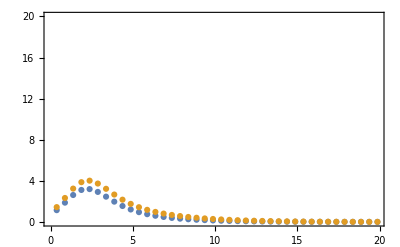

```mathematica
xx=RandomInteger[{1,Length@ls23d}]
ListPlot[{dataT,dataGen[[xx]]},PlotRange->{All,range},Frame->True]
```

```mathematica
$10^{-7}<|U_{\mu N|<10^{-6}$
```

### Chi square

```mathematica
(* χ^2 = 2 Sum[nteo - ndata + ndata*Log(ndata/nteo),{i,bin}] *)
```

```mathematica
(* data is SM *)
```

```mathematica
(* without bg *)
```

```mathematica
(* for 3.5 years *)
```

```mathematica
chis23d=Table[2*Sum[(dataGen[[j,i,2]])-(dataTrue[[i,2]])+(dataTrue[[i,2]])*Log[(dataTrue[[i,2]])/(dataGen[[j,i,2]])],{i,40}],{j,Length@dataGen}]//Chop
```

{16.3418,11.4956,7.66016,4.75525,2.68211,1.32124,0.532046,0.156096,0.0287278,0.00489495,0,0.0279364,0.204785,0.710923,1.74161,3.47406,6.05469,9.59844,14.1928,19.9032,26.7776}

```mathematica
(* for 3.0 years *)
```

```mathematica
years=3/3.5;
```

```mathematica
chis23d=Table[2*Sum[(years*dataGen[[j,i,2]])-(years*dataTrue[[i,2]])+(years*dataTrue[[i,2]])*Log[(dataTrue[[i,2]])/(dataGen[[j,i,2]])],{i,40}],{j,Length@dataGen}]//Chop
```

{14.0072,9.85339,6.56585,4.07593,2.29895,1.13249,0.456039,0.133797,0.0246238,0.00419567,0,0.0239455,0.17553,0.609362,1.49281,2.97776,5.18974,8.22723,12.1653,17.0599,22.9523}

```mathematica
(* with bg *)
```

```mathematica
(* for 3.5 years *)
```

```mathematica
chis23dbg=Table[2*Sum[(dataGen[[j,i,2]]+(1+27^2*ls23d[[j,1]]^2)*(1+α)*bg[[i,2]])-(dataTrue[[i,2]]+bg[[i,2]])+(dataTrue[[i,2]]+bg[[i,2]])*Log[(dataTrue[[i,2]]+bg[[i,2]])/(dataGen[[j,i,2]]+(1+27^2*ls23d[[j,1]]^2)*(1+α)*bg[[i,2]])],{i,40}]+(α/0.25)^2,{j,Length@dataGen},{α,-.5,.5,.05}]//Chop;
```

```mathematica
Table[α,{α,-.5,.5,.05}];
Table[i,{i,Length@%}];
la=Thread[%->%%]
```

{1→-0.5,2→-0.45,3→-0.4,4→-0.35,5→-0.3,6→-0.25,7→-0.2,8→-0.15,9→-0.1,10→-0.05,11→0.,12→0.05,13→0.1,14→0.15,15→0.2,16→0.25,17→0.3,18→0.35,19→0.4,20→0.45,21→0.5}

```mathematica
Min/@chis23dbg
(Table[Position[chis23dbg[[i]],%[[i]]],{i,Length@chis23dbg}]//Flatten)/.la
```

{13.5199,9.48621,6.2993,3.89433,2.19369,1.10889,0.437802,0.152519,0.0223227,0.00154476,0,0.0185817,0.147654,0.430076,1.12841,2.30451,4.11401,6.68495,10.0987,14.4203,19.6991}

{-0.3,-0.25,-0.2,-0.15,-0.1,-0.05,-0.05,0.,0.,0.,0.,0.,-0.05,-0.05,-0.1,-0.1,-0.15,-0.2,-0.25,-0.3,-0.35}

```mathematica
chis23dbg=Min/@chis23dbg;
```

```mathematica
(* for 3.0 years *)
```

```mathematica
years=3/3.5;
```

```mathematica
chis23dbg=Table[2*Sum[years*(dataGen[[j,i,2]]+(1+27^2*ls23d[[j,1]]^2)*(1+α)*bg[[i,2]])-years*(dataTrue[[i,2]]+bg[[i,2]])+years*(dataTrue[[i,2]]+bg[[i,2]])*Log[(dataTrue[[i,2]]+bg[[i,2]])/(dataGen[[j,i,2]]+(1+27^2*ls23d[[j,1]]^2)*(1+α)*bg[[i,2]])],{i,40}]+(α/0.25)^2,{j,Length@dataGen},{α,-.5,.5,.05}]//Chop;
```

```mathematica
Table[α,{α,-.5,.5,.05}];
Table[i,{i,Length@%}];
la=Thread[%->%%]
```

{1→-0.5,2→-0.45,3→-0.4,4→-0.35,5→-0.3,6→-0.25,7→-0.2,8→-0.15,9→-0.1,10→-0.05,11→0.,12→0.05,13→0.1,14→0.15,15→0.2,16→0.25,17→0.3,18→0.35,19→0.4,20→0.45,21→0.5}

```mathematica
Min/@chis23dbg
(Table[Position[chis23dbg[[i]],%[[i]]],{i,Length@chis23dbg}]//Flatten)/.la
```

{11.7314,8.24829,5.49083,3.38943,1.90317,0.956192,0.380974,0.13073,0.0191338,0.00132408,0,0.0159271,0.13173,0.374351,0.990063,1.99815,3.57772,5.82138,8.7989,12.566,17.1649}

{-0.25,-0.2,-0.2,-0.15,-0.1,-0.05,-0.05,0.,0.,0.,0.,0.,0.,-0.05,-0.1,-0.1,-0.15,-0.2,-0.25,-0.3,-0.35}

```mathematica
chis23dbg=Min/@chis23dbg;
```

### chi2 data

```mathematica
dataSet2=chis23d;
dataSet2bg=chis23dbg;
```

### Data High

```mathematica
(* OS: Win, Linux *)
OS="Win";
```

```mathematica
(* ModeHE, ModeAntiNu, ModeNu *)
(* Tau_minus, Tau_plus *)
```

```mathematica
mode="HE";sign="minus";
If[mode=="Nu",range=40,range=20];
```

```mathematica
(* Linux *)
```

```mathematica
If[OS=="Linux",data=Import[StringJoin["/home/adriano/Dropbox/Neutrinos/Tau/Data/Mat_WS_In_Mode",mode,"_Tau_",sign,".txt"],"Table"];
data=Table[{.5*i-.25/2,data[[i,2]]},{i,40}];
data2=Import[StringJoin["/home/adriano/Dropbox/Neutrinos/Tau/Data/Mat_WoutS_In_Mode",mode,"_Tau_",sign,".txt"],"Table"];
data2=Table[{.5*i-.25/2,data2[[i,2]]},{i,40}];
bg=Import[StringJoin["/home/adriano/Dropbox/Neutrinos/Tau/Data/Mat_WS_In_Mode",mode,"_BG.txt"],"Table"];
bg=Table[{.5*i-.25/2,bg[[i,2]]},{i,40}],data=Import[StringJoin["C:\\Users\\Orlando\\Dropbox\\Neutrinos\\Tau\\Data\\Mat_WS_In_Mode",mode,"_Tau_",sign,".txt"],"Table"];
data=Table[{.5*i-.25/2,data[[i,2]]},{i,40}];
data2=Import[StringJoin["C:\\Users\\Orlando\\Dropbox\\Neutrinos\\Tau\\Data\\Mat_WoutS_In_Mode",mode,"_Tau_",sign,".txt"],"Table"];
data2=Table[{.5*i-.25/2,data2[[i,2]]},{i,40}];bg=Import[StringJoin["C:\\Users\\Orlando\\Dropbox\\Neutrinos\\Tau\\Data\\Mat_WS_In_Mode",mode,"_BG.txt"],"Table"];
bg=Table[{.5*i-.25/2,bg[[i,2]]},{i,40}]];
```

### Data of Fig 1 by reconstructed energy

```mathematica
Clear[fs,fn]
fs[Ere_,Etrue_]:=If[Etrue<3.1,0,(*1/(Sqrt[2Pi]σe)*)(Exp[-1/2((Ere-x)/σe)^2]/.{x->b*Etrue,σe->r*Etrue}/.Thread[{b,r}->{.45,.25}])]
fn[Ere_,Etrue_]:=If[Etrue<3.1,0,fs[Ere,Etrue]/NIntegrate[fs[ere,Etrue],{ere,0,20}]]
```

```mathematica
(* dN/Subscript[dE, rec]=∫dN/Subscript[dE, true] P(Subscript[E, rec],Subscript[E, true])ⅆ Subscript[E, true] *)
(* doing numerical integration by cutting the integrand *)
dataT=Table[{data2[[j,1]],Sum[fn[data2[[j,1]],data2[[i,1]]]*0.5*data2[[i,2]],{i,40}]},{j,40}];
(*dataT=Table[{.5*j-.25,Sum[fn[0.5*j-.25,.5*i-.25]*0.5*data2[[i,2]],{i,40}]},{j,40}]//Quiet;*)
dtrue=Interpolation@data2;
ndtrue=NIntegrate[dtrue[x],{x,Min@data[[All,1]],Max@data[[All,1]]}]
dre=Interpolation@data;
ndre=NIntegrate[dre[x],{x,Min@data[[All,1]],Max@data[[All,1]]}]
dreInt=Interpolation@dataT;
ndreInt=NIntegrate[dreInt[x],{x,Min@data[[All,1]],Max@data[[All,1]]}]
fac2=ndtrue/ndreInt
(*dataT=Table[{.5*j-.25,fac2*Sum[fn[0.5*j-.25,.5*i]*0.5*data2[[i,2]],{i,40}]},{j,40}]//Quiet;*)
dataT=Table[{data2[[j,1]],fac2*Sum[fn[data2[[j,1]],data2[[i,1]]]*0.5*data2[[i,2]],{i,40}]},{j,40}];
```

77.45

76.1852

75.6044

1.02441

```mathematica
ListPlot[{data,dataT},Frame->True,PlotRange->{{0,20},{0,40}},AspectRatio->1]
```

-Graphics-

```mathematica
dataTrue=dataT;
```

### General Probability ratio

```mathematica
ratioGen[S23_,δ_,epS_,ee_]=(ee (-537.0144158815365 s23^2+(95.922402136029-4.114998188599089 ee) ee s23^2+(537.0144158815365+ee (-95.92240213602899+4.114998188599089 ee)) s23^4+epS^2 (-194626.6461383849+(34963.71557858255-1499.9168397443682 ee) ee+382355.29126830207 s23^2+ee (-69927.4311571651+2999.8336794887364 ee) s23^2+(-391483.50917764+(69927.4311571651-2999.8336794887364 ee) ee) s23^4)+epS s23 √(1-s23^2) (14161.307084011187-28998.778457602955 s23^2+ee (-2589.904857672781+5179.809715345562 s23^2+ee (111.1049510921754-222.2099021843508 s23^2))))-2536.820066237314 epS s23 √(1-s23^2) Sin[8.323065282815573/ee]+1119.5858672098655 ee epS s23 √(1-s23^2) Sin[8.323065282815573/ee]-39.38853098975155 ee^2 epS s23 √(1-s23^2) Sin[8.323065282815573/ee]+5073.640132474628 epS s23^3 √(1-s23^2) Sin[8.323065282815573/ee]-1796.3230913768598 ee epS s23^3 √(1-s23^2) Sin[8.323065282815573/ee]+78.7770619795031 ee^2 epS s23^3 √(1-s23^2) Sin[8.323065282815573/ee]+Cos[δ] (s23 (epS s23 (261.20978051393564-348.27970735191445 s23^2)+4701.776049250849 epS^2 s23^2 √(1-s23^2)-6.44962421022064 √(1-s23^2) (-0.5+1. s23^2))+ee s23 (-403.4052420503069 epS^2 s23^2 √(1-s23^2)+0.5533679589167451 √(1-s23^2) (-0.4999999999999999+1. s23^2)+epS s23 (-22.411402336128184+29.881869781504182 s23^2))+ee^3 (-0.03334587340666304 √(1-s23^2) (-0.5 s23+1. s23^3)+24.30914171345736 epS^2 √(1-s23^2) (-0.5 s23+1. s23^3)+epS (-0.22508464549497562+1.8006771639598036 s23^2-1.800677163959804 s23^4))+ee^2 (0.38865342484877047 √(1-s23^2) (-0.5 s23+1. s23^3)-283.3283467147537 epS^2 √(1-s23^2) (-0.5 s23+1. s23^3)+epS (2.623410617729201-20.987284941833607 s23^2+20.987284941833604 s23^4))+s23 (epS^2 √(1-s23^2) (-12603.870244016523+1081.3929190371105 ee+12603.870244016523 s23^2-1081.3929190371105 ee s23^2)+√(1-s23^2) (8.644629796993499-0.7416961035919825 ee-17.289259593986998 s23^2+1.483392207183965 ee s23^2)+epS s23 (1167.0250225941222-100.12897398491762 ee-933.6200180752978 s23^2+80.1031791879341 ee s23^2)) Sin[8.323065282815573/ee])-8.644629796993499 s23 √(1-s23^2) Sin[δ]+0.7416961035919825 ee s23 √(1-s23^2) Sin[δ]+3.2248121051103213 s23 √(1-s23^2) Sin[8.323065282815573/ee] Sin[δ]-0.2766839794583725 ee s23 √(1-s23^2) Sin[8.323065282815573/ee] Sin[δ]+Sin[8.323065282815573/ee] (-5978.45668107876 ee epS^2+(93.95629874953016-68494.14178840749 epS^2+ee (-33.26524243290481+1.4588344811019092 ee+30228.81841466637 epS^2-1063.4903367232919 ee epS^2)) s23^2+(-93.95629874953016+68494.14178840749 epS^2+ee (33.26524243290481-1.4588344811019092 ee-24250.361733587608 epS^2+1063.4903367232919 ee epS^2)) s23^4+(87.06992683797868-7.470467445376055 ee) epS s23^2 Sin[δ])+Cos[8.323065282815573/ee] (ee ((537.0144158815365+ee (-95.92240213602898+4.114998188599088 ee)) s23^2+(-537.0144158815365+(95.92240213602898-4.114998188599088 ee) ee) s23^4+epS^2 (-6898.001008467854+(-384585.5081691722+(69927.43115716509-2999.8336794887364 ee) ee) s23^2+(391483.50917764+ee (-69927.4311571651+2999.8336794887364 ee)) s23^4)+epS s23 √(1-s23^2) (-14243.90770996934+28998.778457602955 s23^2+ee (2589.904857672781-5179.809715345562 s23^2+ee (-111.1049510921754+222.2099021843508 s23^2))))+s23 (epS s23 (-435.3496341898932+ee (37.352337226880266+(20.987284941833604-1.8006771639598043 ee) ee)+(348.2797073519141+ee (-29.881869781504264+ee (-20.987284941833607+1.800677163959804 ee))) s23^2)+epS^2 √(1-s23^2) (4701.776049250852-4701.776049250846 s23^2+ee (-403.4052420503069+403.4052420503069 s23^2+ee (-141.66417335737682+12.15457085672868 ee+283.3283467147537 s23^2-24.30914171345736 ee s23^2)))+√(1-s23^2) (-3.224812105110321+6.449624210220642 s23^2+ee (0.27668397945837264-0.553367958916745 s23^2+ee (0.19432671242438523-0.01667293670333152 ee-0.38865342484877047 s23^2+0.03334587340666304 ee s23^2)))) Cos[δ]+s23 ((233.40500451882428-20.025794796983522 ee) epS s23-0.7416961035919825 (-11.65521802680122+1. ee) √(1-s23^2)) Sin[δ])+epS ((87.06992683797863+ee (-7.4704674453760544+(-2.623410617729201+0.22508464549497553 ee) ee)) Cos[8.323065282815573/ee+δ]+2.842170943040401*^-14 Sin[8.323065282815573/ee-δ]+(-233.40500451882443+20.025794796983533 ee) s23^2 Sin[δ]+(-233.40500451882437+20.025794796983526 ee) Sin[8.323065282815573/ee+δ]))/(2.7607421580402205+ee (-130.8796094130282+(23.3230292223281-1. ee) ee)+(-2.76074215804022+ee (130.87960941302822+ee (-23.323029222328106+1. ee))) Cos[8.323065282815573/ee]+(22.46560935192947+(-8.05902865451455+0.3548994794121858 ee) ee) Sin[8.323065282815573/ee])/.s23->Sqrt[S23];
```

### Creating data with NSI

```mathematica
(* Subscript[dN, nsi]/Subscript[dE, rec]=∫Subscript[dN, nsi]/Subscript[dE, true] P(Subscript[E, rec],Subscript[E, true])ⅆ Subscript[E, true] =∫(Subscript[P, NSI](μ->τ))/Subscript[P, SM(μ->τ)] Subscript[dN, sm]/Subscript[dE, true] P(Subscript[E, rec],Subscript[E, true])ⅆ Subscript[E, true] *)
```

```mathematica
(* best-fit used {S23,δ} = {0.582,-2.5} *)
```

```mathematica
passoNSI=4./20;
dataGen={};ls23d={};
Clear[delta,ss23];
Do[delta=(-2.+passoNSI*k)*10^-2;AppendTo[ls23d,{delta}];
AppendTo[dataGen,Table[{data2[[j,1]],fac2*Sum[fn[data2[[j,1]],data2[[i,1]]]*0.5*data2[[i,2]]*ratioGen[0.582,-2.5,delta,.5*i],{i,40}]},{j,40}]],{k,0,20}];
```

```mathematica
dataGen//Dimensions
```

{21,40,2}

3

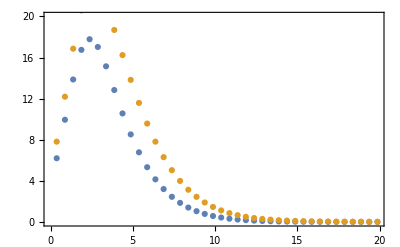

```mathematica
xx=RandomInteger[{1,Length@ls23d}]
ListPlot[{dataT,dataGen[[xx]]},PlotRange->{All,range},Frame->True]
```

### Chi square

```mathematica
(* χ^2 = 2 Sum[nteo - ndata + ndata*Log(ndata/nteo),{i,bin}] *)
```

```mathematica
(* data is SM *)
```

```mathematica
(* without bg *)
```

```mathematica
(* for 3.5 years *)
```

```mathematica
chis23d=Table[2*Sum[(dataGen[[j,i,2]])-(dataTrue[[i,2]])+(dataTrue[[i,2]])*Log[(dataTrue[[i,2]])/(dataGen[[j,i,2]])],{i,40}],{j,Length@dataGen}]//Chop
```

{71.5077,48.7148,31.1906,18.4048,9.71496,4.37153,1.54253,0.369311,0.0608871,0.0240377,0,0.149249,1.02924,3.46918,8.40769,16.7598,29.3379,46.8204,69.7501,98.5474,133.53}

```mathematica
(* for 3.0 years *)
```

```mathematica
years=3/3.5;
```

```mathematica
chis23d=Table[2*Sum[(years*dataGen[[j,i,2]])-(years*dataTrue[[i,2]])+(years*dataTrue[[i,2]])*Log[(dataTrue[[i,2]])/(dataGen[[j,i,2]])],{i,40}],{j,Length@dataGen}]//Chop
```

{61.2923,41.7555,26.7348,15.7755,8.32711,3.74702,1.32217,0.316552,0.052189,0.0206037,0,0.127928,0.882208,2.97358,7.20659,14.3655,25.1467,40.1318,59.7858,84.4692,114.454}

```mathematica
(* with bg *)
```

```mathematica
(* for 3.5 years *)
```

```mathematica
chis23dbg=Table[2*Sum[(dataGen[[j,i,2]]+(1+27^2*ls23d[[j,1]]^2)*(1+α)*bg[[i,2]])-(dataTrue[[i,2]]+bg[[i,2]])+(dataTrue[[i,2]]+bg[[i,2]])*Log[(dataTrue[[i,2]]+bg[[i,2]])/(dataGen[[j,i,2]]+(1+27^2*ls23d[[j,1]]^2)*(1+α)*bg[[i,2]])],{i,40}]+(α/0.25)^2,{j,Length@dataGen},{α,-.5,.5,.05}]//Chop;
```

```mathematica
Table[α,{α,-.5,.5,.05}];
Table[i,{i,Length@%}];
la=Thread[%->%%]
```

{1→-0.5,2→-0.45,3→-0.4,4→-0.35,5→-0.3,6→-0.25,7→-0.2,8→-0.15,9→-0.1,10→-0.05,11→0.,12→0.05,13→0.1,14→0.15,15→0.2,16→0.25,17→0.3,18→0.35,19→0.4,20→0.45,21→0.5}

```mathematica
Min/@chis23dbg
(Table[Position[chis23dbg[[i]],%[[i]]],{i,Length@chis23dbg}]//Flatten)/.la
```

{62.1666,41.8594,26.7319,15.8053,8.38644,3.81451,1.38085,0.348416,0.0515139,0.0186567,0,0.110054,0.759913,2.63468,6.51664,13.2374,23.5567,38.2631,58.3354,84.2725,116.45}

{-0.5,-0.5,-0.45,-0.35,-0.25,-0.15,-0.1,-0.05,0.,0.,0.,-0.05,-0.1,-0.15,-0.25,-0.35,-0.45,-0.5,-0.5,-0.5,-0.5}

```mathematica
chis23dbg=Min/@chis23dbg;
```

```mathematica
(* for 3.0 years *)
```

```mathematica
years=3/3.5;
```

```mathematica
chis23dbg=Table[2*Sum[years*(dataGen[[j,i,2]]+(1+27^2*ls23d[[j,1]]^2)*(1+α)*bg[[i,2]])-years*(dataTrue[[i,2]]+bg[[i,2]])+years*(dataTrue[[i,2]]+bg[[i,2]])*Log[(dataTrue[[i,2]]+bg[[i,2]])/(dataGen[[j,i,2]]+(1+27^2*ls23d[[j,1]]^2)*(1+α)*bg[[i,2]])],{i,40}]+(α/0.25)^2,{j,Length@dataGen},{α,-.5,.5,.05}]//Chop;
```

```mathematica
Table[α,{α,-.5,.5,.05}];
Table[i,{i,Length@%}];
la=Thread[%->%%]
```

{1→-0.5,2→-0.45,3→-0.4,4→-0.35,5→-0.3,6→-0.25,7→-0.2,8→-0.15,9→-0.1,10→-0.05,11→0.,12→0.05,13→0.1,14→0.15,15→0.2,16→0.25,17→0.3,18→0.35,19→0.4,20→0.45,21→0.5}

```mathematica
Min/@chis23dbg
(Table[Position[chis23dbg[[i]],%[[i]]],{i,Length@chis23dbg}]//Flatten)/.la
```

{53.8571,36.4509,23.3296,13.7823,7.3075,3.32101,1.20203,0.304356,0.0441548,0.0159914,0,0.100047,0.674211,2.30973,5.72855,11.6067,20.6301,33.3684,50.5732,72.805,100.385}

{-0.5,-0.5,-0.4,-0.3,-0.2,-0.15,-0.05,-0.05,0.,0.,0.,-0.05,-0.1,-0.15,-0.25,-0.3,-0.4,-0.5,-0.5,-0.5,-0.5}

```mathematica
chis23dbg=Min/@chis23dbg;
```

### chi2 data

```mathematica
dataSet3=chis23d;
dataSet3bg=chis23dbg;
```

### Data

```mathematica
ls23d
```

{{-0.02},{-0.018},{-0.016},{-0.014},{-0.012},{-0.01},{-0.008},{-0.006},{-0.004},{-0.002},{0.},{0.002},{0.004},{0.006},{0.008},{0.01},{0.012},{0.014},{0.016},{0.018},{0.02}}

```mathematica
dataSet1
dataSet1bg
```

{24.3396,17.191,11.5483,7.27289,4.20758,2.17296,0.964689,0.355655,0.111226,0.0284734,0,0.0729979,0.454383,1.4516,3.3952,6.58685,11.2793,17.676,25.9376,36.1904,48.534}

{23.0661,16.2202,10.8145,6.73103,3.83151,1.9249,0.806023,0.26183,0.0688413,0.017481,0,0.059466,0.305187,1.04217,2.5418,5.07419,8.87964,14.1583,21.0703,29.7219,40.1625}

```mathematica
dataSet2
dataSet2bg
```

{14.0072,9.85339,6.56585,4.07593,2.29895,1.13249,0.456039,0.133797,0.0246238,0.00419567,0,0.0239455,0.17553,0.609362,1.49281,2.97776,5.18974,8.22723,12.1653,17.0599,22.9523}

{11.7314,8.24829,5.49083,3.38943,1.90317,0.956192,0.380974,0.13073,0.0191338,0.00132408,0,0.0159271,0.13173,0.374351,0.990063,1.99815,3.57772,5.82138,8.7989,12.566,17.1649}

```mathematica
dataSet3
dataSet3bg
```

{61.2923,41.7555,26.7348,15.7755,8.32711,3.74702,1.32217,0.316552,0.052189,0.0206037,0,0.127928,0.882208,2.97358,7.20659,14.3655,25.1467,40.1318,59.7858,84.4692,114.454}

{53.8571,36.4509,23.3296,13.7823,7.3075,3.32101,1.20203,0.304356,0.0441548,0.0159914,0,0.100047,0.674211,2.30973,5.72855,11.6067,20.6301,33.3684,50.5732,72.805,100.385}

### Contour

```mathematica
SetDirectory[NotebookDirectory[]]
```

C:\Users\Orlando\Dropbox\Neutrinos\Tau\Notebook

```mathematica
dataSet=dataSet1+dataSet2+dataSet3
```

{99.6392,68.7999,44.8489,27.1243,14.8336,7.05247,2.7429,0.806004,0.188038,0.0532728,0,0.224871,1.51212,5.03454,12.0946,23.9301,41.6158,66.035,97.8887,137.72,185.94}

InterpolatingFunction[…]

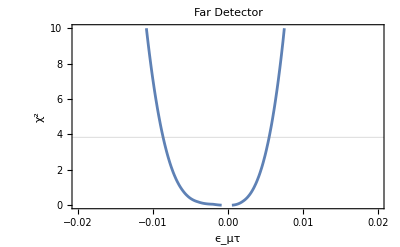

far_detector.pdf

```mathematica
Table[{ls23d[[i]],{dataSet[[i]]}},{i,Length@ls23d}];
func=Interpolation@%
Plot[func[del],{del,Min@ls23d[[All,1]],Max@ls23d[[All,1]]},GridLines->{{},{3.84}},PlotRange->{{Min@ls23d[[All,1]],Max@ls23d[[All,1]]},{0,10}},Frame->True,FrameLabel->{"ϵ_μτ","χ^2"},PlotLabel->"Far Detector"]
Export["far_detector.pdf",%]
```

```mathematica
dataSetbg=dataSet1bg+dataSet2bg+dataSet3bg
```

{88.6546,60.9194,39.6349,23.9027,13.0422,6.2021,2.38902,0.696917,0.13213,0.0347965,0,0.17544,1.11113,3.72625,9.26041,18.679,33.0874,53.3481,80.4424,115.093,157.713}

InterpolatingFunction[…]

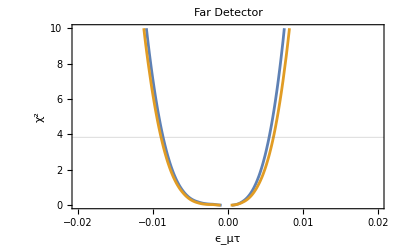

far_detector_bg.pdf

```mathematica
Table[{ls23d[[i]],{dataSetbg[[i]]}},{i,Length@ls23d}];
funcbg=Interpolation@%
Plot[{func[del],funcbg[del]},{del,Min@ls23d[[All,1]],Max@ls23d[[All,1]]},GridLines->{{},{3.84}},PlotRange->{{Min@ls23d[[All,1]],Max@ls23d[[All,1]]},{0,10}},Frame->True,FrameLabel->{"ϵ_μτ","χ^2"},PlotLabel->"Far Detector"]
Export["far_detector_bg.pdf",%]
```

## All data sets - near - NSI

### Data Nu

```mathematica
(* OS: Win, Linux *)
OS="Win";
```

```mathematica
(* ModeHE, ModeAntiNu, ModeNu *)
(* Tau_minus, Tau_plus *)
```

```mathematica
mode="Nu";sign="minus";
If[mode=="Nu",range=40,range=20];
```

```mathematica
(* Linux *)
```

```mathematica
If[OS=="Linux",data=Import[StringJoin["/home/adriano/Dropbox/Neutrinos/Tau/Data/Mat_WS_In_Mode",mode,"_Tau_",sign,".txt"],"Table"];
data=Table[{.5*i-.25/2,data[[i,2]]},{i,40}];
data2=Import[StringJoin["/home/adriano/Dropbox/Neutrinos/Tau/Data/Mat_WoutS_In_Mode",mode,"_Tau_",sign,".txt"],"Table"];
data2=Table[{.5*i-.25/2,data2[[i,2]]},{i,40}];
bg=Import[StringJoin["/home/adriano/Dropbox/Neutrinos/Tau/Data/Mat_WS_In_Mode",mode,"_BG.txt"],"Table"];
bg=Table[{.5*i-.25/2,bg[[i,2]]},{i,40}],data=Import[StringJoin["C:\\Users\\Orlando\\Dropbox\\Neutrinos\\Tau\\Data\\Mat_WS_In_Mode",mode,"_Tau_",sign,".txt"],"Table"];
data=Table[{.5*i-.25/2,data[[i,2]]},{i,40}];
data2=Import[StringJoin["C:\\Users\\Orlando\\Dropbox\\Neutrinos\\Tau\\Data\\Mat_WoutS_In_Mode",mode,"_Tau_",sign,".txt"],"Table"];
data2=Table[{.5*i-.25/2,data2[[i,2]]},{i,40}];bg=Import[StringJoin["C:\\Users\\Orlando\\Dropbox\\Neutrinos\\Tau\\Data\\Mat_WS_In_Mode",mode,"_BG.txt"],"Table"];
bg=Table[{.5*i-.25/2,bg[[i,2]]},{i,40}]];
```

### Data of Fig 1 by reconstructed energy

```mathematica
Clear[fs,fn]
fs[Ere_,Etrue_]:=If[Etrue<3.1,0,(*1/(Sqrt[2Pi]σe)*)(Exp[-1/2((Ere-x)/σe)^2]/.{x->b*Etrue,σe->r*Etrue}/.Thread[{b,r}->{.45,.25}])]
fn[Ere_,Etrue_]:=If[Etrue<3.1,0,fs[Ere,Etrue]/NIntegrate[fs[ere,Etrue],{ere,0,20}]]
```

```mathematica
(* dN/Subscript[dE, rec]=∫dN/Subscript[dE, true] P(Subscript[E, rec],Subscript[E, true])ⅆ Subscript[E, true] *)
(* doing numerical integration by cutting the integrand *)
dataT=Table[{data2[[j,1]],Sum[fn[data2[[j,1]],data2[[i,1]]]*0.5*data2[[i,2]],{i,40}]},{j,40}];
(*dataT=Table[{.5*j-.25,Sum[fn[0.5*j-.25,.5*i-.25]*0.5*data2[[i,2]],{i,40}]},{j,40}]//Quiet;*)
dtrue=Interpolation@data2;
ndtrue=NIntegrate[dtrue[x],{x,Min@data[[All,1]],Max@data[[All,1]]}]
dre=Interpolation@data;
ndre=NIntegrate[dre[x],{x,Min@data[[All,1]],Max@data[[All,1]]}]
dreInt=Interpolation@dataT;
ndreInt=NIntegrate[dreInt[x],{x,Min@data[[All,1]],Max@data[[All,1]]}]
fac2=ndtrue/ndreInt
(*dataT=Table[{.5*j-.25,fac2*Sum[fn[0.5*j-.25,.5*i]*0.5*data2[[i,2]],{i,40}]},{j,40}]//Quiet;*)
dataT=Table[{data2[[j,1]],fac2*Sum[fn[data2[[j,1]],data2[[i,1]]]*0.5*data2[[i,2]],{i,40}]},{j,40}];
```

54.4842

53.3873

52.517

1.03746

```mathematica
ListPlot[{data,dataT},Frame->True,PlotRange->{{0,20},{0,40}},AspectRatio->1]
```

-Graphics-

### General Probability ratio

```mathematica
ratioGen[S23_,δ_,epS_,ee_]=(94593.79431933298 ee epS^2-16993.30788307618 ee^2 epS^2+729.0000000000001 ee^3 epS^2+259.51658341292085 ee s23^2-46.62087210720489 ee^2 s23^2+1.9999999999999998 ee^3 s23^2-184751.02944044588 ee epS^2 s23^2+33986.61576615236 ee^2 epS^2 s23^2-1458.0000000000002 ee^3 epS^2 s23^2-259.5165834129209 ee s23^4+46.62087210720489 ee^2 s23^4-1.9999999999999998 ee^3 s23^4+189187.5893080193 ee epS^2 s23^4-33986.61576615236 ee^2 epS^2 s23^4+1458.0000000000002 ee^3 epS^2 s23^4-6842.630720016514 ee epS s23 √(1-s23^2)+1258.7635468945318 ee^2 epS s23 √(1-s23^2)-54.00000000000001 ee^3 epS s23 √(1-s23^2)+14013.895504297725 ee epS s23^3 √(1-s23^2)-2517.5270937890637 ee^2 epS s23^3 √(1-s23^2)+108.00000000000001 ee^3 epS s23^3 √(1-s23^2)+2.437058034171625 ee epS^2 Sin[0.006402357909858133/ee]-0.03512714837222423 s23^2 Sin[0.006402357909858133/ee]+0.012713742369988023 ee s23^2 Sin[0.006402357909858133/ee]-0.0005454098974757641 ee^2 s23^2 Sin[0.006402357909858133/ee]+25.60769116335146 epS^2 s23^2 Sin[0.006402357909858133/ee]-11.705376221892895 ee epS^2 s23^2 Sin[0.006402357909858133/ee]+0.397603815259832 ee^2 epS^2 s23^2 Sin[0.006402357909858133/ee]+0.03512714837222423 s23^4 Sin[0.006402357909858133/ee]-0.012713742369988023 ee s23^4 Sin[0.006402357909858133/ee]+0.0005454098974757641 ee^2 s23^4 Sin[0.006402357909858133/ee]-25.60769116335146 epS^2 s23^4 Sin[0.006402357909858133/ee]+9.26831818772127 ee epS^2 s23^4 Sin[0.006402357909858133/ee]-0.397603815259832 ee^2 epS^2 s23^4 Sin[0.006402357909858133/ee]+0.9484330060500541 epS s23 √(1-s23^2) Sin[0.006402357909858133/ee]-0.43353245266269974 ee epS s23 √(1-s23^2) Sin[0.006402357909858133/ee]+0.014726067231845632 ee^2 epS s23 √(1-s23^2) Sin[0.006402357909858133/ee]-1.8968660121001082 epS s23^3 √(1-s23^2) Sin[0.006402357909858133/ee]+0.6865420879793533 ee epS s23^3 √(1-s23^2) Sin[0.006402357909858133/ee]-0.029452134463691264 ee^2 epS s23^3 √(1-s23^2) Sin[0.006402357909858133/ee]+Cos[δ] (ee s23 (0.00012107371492220409 epS^2 s23^2 √(1-s23^2)-1.6608191333311595*^-7 √(1-s23^2) (-0.5+1. s23^2)+epS (6.7263175012044485*^-6 s23-8.968423319544172*^-6 s23^3))+s23 (-0.0014111405425865087 epS^2 s23^2 √(1-s23^2)+1.935720911561134*^-6 √(1-s23^2) (-0.5+1. s23^2)+epS (-0.00007839669689246875 s23+0.00010452892922785395 s23^3))+ee^2 (-0.1888960369049804 √(1-s23^2) (-0.5 s23+1. s23^3)+137.70521090373074 epS^2 √(1-s23^2) (-0.5 s23+1. s23^3)+epS (-1.275048249108618+10.200385992868943 s23^2-10.200385992868943 s23^4))+ee^3 (0.01620699299409185 √(1-s23^2) (-0.5 s23+1. s23^3)-11.814897892692962 epS^2 √(1-s23^2) (-0.5 s23+1. s23^3)+epS (0.10939720271012002-0.8751776216809599 s23^2+0.8751776216809601 s23^4))+(s23 √(1-s23^2) (-0.0035238968220475553+0.007047793644095111 s23^2+ee (0.00030234499379971615-0.0006046899875994323 s23^2))+epS^2 s23 √(1-s23^2) (5.137841566545336-5.137841566545336 s23^2+ee (-0.4408190009599862+0.4408190009599862 s23^2))+epS (0.09514521419528398-0.4757260709764199 s23^2+0.3805808567811359 s23^4+ee (-0.008163314832592337+0.04081657416296169 s23^2-0.03265325933036935 s23^4))) Sin[0.006402357909858133/ee])+0.09514521419528398 epS s23^2 Sin[δ]-0.008163314832592337 ee epS s23^2 Sin[δ]+0.0035238968220475553 s23 √(1-s23^2) Sin[δ]-0.00030234499379971615 ee s23 √(1-s23^2) Sin[δ]+0.000026132232306963488 epS Sin[0.006402357909858133/ee] Sin[δ]-2.2421058289978646*^-6 ee epS Sin[0.006402357909858133/ee] Sin[δ]-1.2750482491086177 ee^2 epS Sin[0.006402357909858133/ee] Sin[δ]+0.10939720271012002 ee^3 epS Sin[0.006402357909858133/ee] Sin[δ]-0.00002613223216485494 epS s23^2 Sin[0.006402357909858133/ee] Sin[δ]+2.2421058289978646*^-6 ee epS s23^2 Sin[0.006402357909858133/ee] Sin[δ]-9.67860455780567*^-7 s23 √(1-s23^2) Sin[0.006402357909858133/ee] Sin[δ]+8.304095677758028*^-8 ee s23 √(1-s23^2) Sin[0.006402357909858133/ee] Sin[δ]+Cos[0.006402357909858133/ee] (4436.55919822007 ee epS^2-259.5165834129209 ee s23^2+46.62087210720489 ee^2 s23^2-1.9999999999999998 ee^3 s23^2+184751.03010979923 ee epS^2 s23^2-33986.61576615236 ee^2 epS^2 s23^2+1458.0000000000002 ee^3 epS^2 s23^2+259.51658341292085 ee s23^4-46.62087210720489 ee^2 s23^4+1.9999999999999998 ee^3 s23^4-189187.5893080193 ee epS^2 s23^4+33986.61576615236 ee^2 epS^2 s23^4-1458.0000000000002 ee^3 epS^2 s23^4+6842.6307448073785 ee epS s23 √(1-s23^2)-1258.7635468945318 ee^2 epS s23 √(1-s23^2)+54.00000000000001 ee^3 epS s23 √(1-s23^2)-14013.895504297725 ee epS s23^3 √(1-s23^2)+2517.5270937890637 ee^2 epS s23^3 √(1-s23^2)-108.00000000000001 ee^3 epS s23^3 √(1-s23^2)+(s23 √(1-s23^2) (9.67860455780567*^-7-1.9357209106729556*^-6 s23^2+ee^3 (0.008103496497045925-0.01620699299409185 s23^2)+ee (-8.304095677758028*^-8+1.6608191322209365*^-7 s23^2)+ee^2 (-0.0944480184524902+0.1888960369049804 s23^2))+epS^2 s23 √(1-s23^2) (-0.001411140544405498+0.0014111405425865087 s23^2+ee^2 (68.85260545186536-137.70521090373074 s23^2)+ee (0.00012107371497904751-0.00012107371486536067 s23^2)+ee^3 (-5.907448946346481+11.814897892692962 s23^2))+epS (-0.000026132232306963488+0.00013066116162008257 s23^2-0.00010452892917101053 s23^4+ee^3 (-0.10939720271012002+0.87517762168096 s23^2-0.8751776216809601 s23^4)+ee (2.2421058307742214*^-6-0.000011210529159200178 s23^2+8.9684233266496*^-6 s23^4)+ee^2 (1.2750482491086181-10.200385992868942 s23^2+10.200385992868945 s23^4))) Cos[δ]+0.09514521419528398 epS Sin[δ]-0.008163314832592337 ee epS Sin[δ]-0.09514521419528395 epS s23^2 Sin[δ]+0.008163314832592337 ee epS s23^2 Sin[δ]-0.0035238968220475553 s23 √(1-s23^2) Sin[δ]+0.00030234499379971615 ee s23 √(1-s23^2) Sin[δ]))/(-1.341795282562343+63.61100567174531 ee-11.335618644558162 ee^2+0.4860268585414585 ee^3+(1.3417952825623427-63.611005671745296 ee+11.33561864455816 ee^2-0.4860268585414585 ee^3) Cos[8.323065282815573/ee]+(-10.918890423369778+3.916904466255335 ee-0.17249067968380818 ee^2) Sin[8.323065282815573/ee])/.s23->Sqrt[S23];
```

### Creating data with NSI

```mathematica
(* Subscript[dN, nsi]/Subscript[dE, rec]=∫Subscript[dN, nsi]/Subscript[dE, true] P(Subscript[E, rec],Subscript[E, true])ⅆ Subscript[E, true] =∫(Subscript[P, NSI](μ->τ))/Subscript[P, SM(μ->τ)] Subscript[dN, sm]/Subscript[dE, true] P(Subscript[E, rec],Subscript[E, true])ⅆ Subscript[E, true] *)
```

```mathematica
(* best-fit used {S23,δ} = {0.582,-2.5} *)
```

```mathematica
passoNSI=2./20;
dataGen={};ls23d={};
Clear[delta,ss23];
Do[delta=(-1.+passoNSI*k)*10^-4;AppendTo[ls23d,{delta}];
AppendTo[dataGen,Table[{data2[[j,1]],(3/3.5)*(1300/1)^2*(70/40000)*fac2*Sum[fn[data2[[j,1]],data2[[i,1]]]*0.5*data2[[i,2]]*(ratioGen[0.582,-2.5,delta,.5*i]),{i,40}]},{j,40}]],{k,0,20}];
```

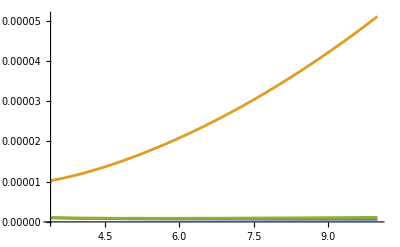

```mathematica
Plot[{ratioGen[0.582,-2.5,0,ee],ratioGen[0.582,-2.5,10^-4,ee],ratioGen[0.582,-2.5,10^-5,ee]},{ee,3.4,10}]
```

```mathematica
dataGen//Dimensions
```

{21,40,2}

```mathematica
dataTrue=dataGen[[(((Length@dataGen)-1)/2+1)]]
```

{{0.375,0.0147204},{0.875,0.0260777},{1.375,0.0360527},{1.875,0.0390462},{2.375,0.0338369},{2.875,0.024409},{3.375,0.0155661},{3.875,0.00949552},{4.375,0.00599982},{4.875,0.00411114},{5.375,0.00304627},{5.875,0.00237553},{6.375,0.00190277},{6.875,0.00154347},{7.375,0.00125909},{7.875,0.00102934},{8.375,0.000841759},{8.875,0.000687729},{9.375,0.000560885},{9.875,0.000456318},{10.375,0.000370137},{10.875,0.000299201},{11.375,0.000240935},{11.875,0.00019321},{12.375,0.000154249},{12.875,0.000122567},{13.375,0.000096912},{13.875,0.0000762349},{14.375,0.0000596519},{14.875,0.0000464216},{15.375,0.0000359236},{15.875,0.0000276406},{16.375,0.0000211431},{16.875,0.0000160765},{17.375,0.0000121497},{17.875,9.12525×10^-6},{18.375,6.81045×10^-6},{18.875,5.0502×10^-6},{19.375,3.7204×10^-6},{19.875,2.72248×10^-6}}

8

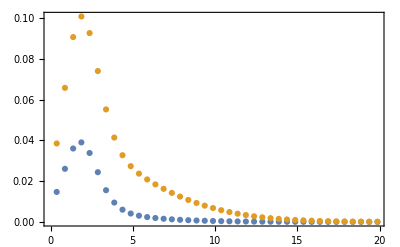

```mathematica
xx=RandomInteger[{1,Length@ls23d}]
ListPlot[{dataTrue,dataGen[[xx]]},PlotRange->{All,All},Frame->True]
```

### Chi square

```mathematica
(* χ^2 = 2 Sum[nteo - ndata + ndata*Log(ndata/nteo),{i,bin}] *)
```

```mathematica
(* data is SM *)
```

```mathematica
(* without bg *)
```

```mathematica
(* for 3.5 years *)
```

```mathematica
chis23d=Table[2*Sum[(dataGen[[j,i,2]])-(dataTrue[[i,2]])+(dataTrue[[i,2]])*Log[(dataTrue[[i,2]])/(dataGen[[j,i,2]])],{i,40}],{j,Length@dataGen}]//Chop
```

{11.1479,8.84869,6.8102,5.03442,3.5239,2.28183,1.312,0.617614,0.196212,0.0217462,0,0.0212508,0.194041,0.61324,1.30531,2.27282,3.5126,5.02087,6.79442,8.83071,11.1278}

```mathematica
(* for 3.0 years *)
```

```mathematica
years=3/3.5;
```

```mathematica
chis23d=Table[2*Sum[(years*dataGen[[j,i,2]])-(years*dataTrue[[i,2]])+(years*dataTrue[[i,2]])*Log[(dataTrue[[i,2]])/(dataGen[[j,i,2]])],{i,40}],{j,Length@dataGen}]//Chop
```

{9.55536,7.58459,5.83731,4.31522,3.02048,1.95585,1.12457,0.529384,0.168182,0.0186396,0,0.018215,0.166321,0.525635,1.11883,1.94813,3.0108,4.30361,5.82379,7.56918,9.53808}

```mathematica
(* with bg *)
```

```mathematica
(* for 3.5 years *)
```

```mathematica
chis23dbg=Table[2*Sum[(dataGen[[j,i,2]]+(1+27^2*ls23d[[j,1]]^2)*(1+α)*bg[[i,2]])-(dataTrue[[i,2]]+bg[[i,2]])+(dataTrue[[i,2]]+bg[[i,2]])*Log[(dataTrue[[i,2]]+bg[[i,2]])/(dataGen[[j,i,2]]+(1+27^2*ls23d[[j,1]]^2)*(1+α)*bg[[i,2]])],{i,40}]+(α/0.25)^2,{j,Length@dataGen},{α,-.5,.5,.05}]//Chop;
```

```mathematica
Table[α,{α,-.5,.5,.05}];
Table[i,{i,Length@%}];
la=Thread[%->%%]
```

{1→-0.5,2→-0.45,3→-0.4,4→-0.35,5→-0.3,6→-0.25,7→-0.2,8→-0.15,9→-0.1,10→-0.05,11→0.,12→0.05,13→0.1,14→0.15,15→0.2,16→0.25,17→0.3,18→0.35,19→0.4,20→0.45,21→0.5}

```mathematica
Min/@chis23dbg
(Table[Position[chis23dbg[[i]],%[[i]]],{i,Length@chis23dbg}]//Flatten)/.la
```

{1.74897,1.23366,0.843499,0.562264,0.37251,0.227583,0.116019,0.0503745,0.0161977,0.00218803,0,0.00216151,0.0160969,0.050137,0.115557,0.226791,0.371816,0.561059,0.841652,1.23104,1.74546}

{-0.05,-0.05,-0.05,-0.05,-0.05,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-0.05,-0.05,-0.05,-0.05,-0.05}

```mathematica
chis23dbg=Min/@chis23dbg;
```

```mathematica
(* for 3.0 years *)
```

```mathematica
years=3/3.5;
```

```mathematica
chis23dbg=Table[2*Sum[years*(dataGen[[j,i,2]]+(1+27^2*ls23d[[j,1]]^2)*(1+α)*bg[[i,2]])-years*(dataTrue[[i,2]]+bg[[i,2]])+years*(dataTrue[[i,2]]+bg[[i,2]])*Log[(dataTrue[[i,2]]+bg[[i,2]])/(dataGen[[j,i,2]]+(1+27^2*ls23d[[j,1]]^2)*(1+α)*bg[[i,2]])],{i,40}]+(α/0.25)^2,{j,Length@dataGen},{α,-.5,.5,.05}]//Chop;
```

```mathematica
Table[α,{α,-.5,.5,.05}];
Table[i,{i,Length@%}];
la=Thread[%->%%]
```

{1→-0.5,2→-0.45,3→-0.4,4→-0.35,5→-0.3,6→-0.25,7→-0.2,8→-0.15,9→-0.1,10→-0.05,11→0.,12→0.05,13→0.1,14→0.15,15→0.2,16→0.25,17→0.3,18→0.35,19→0.4,20→0.45,21→0.5}

```mathematica
Min/@chis23dbg
(Table[Position[chis23dbg[[i]],%[[i]]],{i,Length@chis23dbg}]//Flatten)/.la
```

{1.50483,1.06314,0.728713,0.487655,0.325009,0.195071,0.0994447,0.0431781,0.0138837,0.00187546,0,0.00185272,0.0137973,0.0429746,0.099049,0.194392,0.324414,0.486622,0.72713,1.0609,1.50182}

{-0.05,-0.05,-0.05,-0.05,-0.05,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-0.05,-0.05,-0.05,-0.05,-0.05}

```mathematica
chis23dbg=Min/@chis23dbg;
```

### chi2 data

```mathematica
dataSet1=chis23d;
dataSet1bg=chis23dbg;
```

### Data AntiNu

```mathematica
(* OS: Win, Linux *)
OS="Win";
```

```mathematica
(* ModeHE, ModeAntiNu, ModeNu *)
(* Tau_minus, Tau_plus *)
```

```mathematica
mode="AntiNu";sign="minus";
If[mode=="Nu",range=40,range=20];
```

```mathematica
(* Linux *)
```

```mathematica
If[OS=="Linux",data=Import[StringJoin["/home/adriano/Dropbox/Neutrinos/Tau/Data/Mat_WS_In_Mode",mode,"_Tau_",sign,".txt"],"Table"];
data=Table[{.5*i-.25/2,data[[i,2]]},{i,40}];
data2=Import[StringJoin["/home/adriano/Dropbox/Neutrinos/Tau/Data/Mat_WoutS_In_Mode",mode,"_Tau_",sign,".txt"],"Table"];
data2=Table[{.5*i-.25/2,data2[[i,2]]},{i,40}];
bg=Import[StringJoin["/home/adriano/Dropbox/Neutrinos/Tau/Data/Mat_WS_In_Mode",mode,"_BG.txt"],"Table"];
bg=Table[{.5*i-.25/2,bg[[i,2]]},{i,40}],data=Import[StringJoin["C:\\Users\\Orlando\\Dropbox\\Neutrinos\\Tau\\Data\\Mat_WS_In_Mode",mode,"_Tau_",sign,".txt"],"Table"];
data=Table[{.5*i-.25/2,data[[i,2]]},{i,40}];
data2=Import[StringJoin["C:\\Users\\Orlando\\Dropbox\\Neutrinos\\Tau\\Data\\Mat_WoutS_In_Mode",mode,"_Tau_",sign,".txt"],"Table"];
data2=Table[{.5*i-.25/2,data2[[i,2]]},{i,40}];bg=Import[StringJoin["C:\\Users\\Orlando\\Dropbox\\Neutrinos\\Tau\\Data\\Mat_WS_In_Mode",mode,"_BG.txt"],"Table"];
bg=Table[{.5*i-.25/2,bg[[i,2]]},{i,40}]];
```

### Data of Fig 1 by reconstructed energy

```mathematica
Clear[fs,fn]
fs[Ere_,Etrue_]:=If[Etrue<3.1,0,(*1/(Sqrt[2Pi]σe)*)(Exp[-1/2((Ere-x)/σe)^2]/.{x->b*Etrue,σe->r*Etrue}/.Thread[{b,r}->{.45,.25}])]
fn[Ere_,Etrue_]:=If[Etrue<3.1,0,fs[Ere,Etrue]/NIntegrate[fs[ere,Etrue],{ere,0,20}]]
```

```mathematica
(* dN/Subscript[dE, rec]=∫dN/Subscript[dE, true] P(Subscript[E, rec],Subscript[E, true])ⅆ Subscript[E, true] *)
(* doing numerical integration by cutting the integrand *)
dataT=Table[{data2[[j,1]],Sum[fn[data2[[j,1]],data2[[i,1]]]*0.5*data2[[i,2]],{i,40}]},{j,40}];
(*dataT=Table[{.5*j-.25,Sum[fn[0.5*j-.25,.5*i-.25]*0.5*data2[[i,2]],{i,40}]},{j,40}]//Quiet;*)
dtrue=Interpolation@data2;
ndtrue=NIntegrate[dtrue[x],{x,Min@data[[All,1]],Max@data[[All,1]]}]
dre=Interpolation@data;
ndre=NIntegrate[dre[x],{x,Min@data[[All,1]],Max@data[[All,1]]}]
dreInt=Interpolation@dataT;
ndreInt=NIntegrate[dreInt[x],{x,Min@data[[All,1]],Max@data[[All,1]]}]
fac2=ndtrue/ndreInt
(*dataT=Table[{.5*j-.25,fac2*Sum[fn[0.5*j-.25,.5*i]*0.5*data2[[i,2]],{i,40}]},{j,40}]//Quiet;*)
dataT=Table[{data2[[j,1]],fac2*Sum[fn[data2[[j,1]],data2[[i,1]]]*0.5*data2[[i,2]],{i,40}]},{j,40}];
```

13.1906

12.9894

12.8561

1.02602

```mathematica
ListPlot[{data,dataT},Frame->True,PlotRange->{{0,20},{0,40}},AspectRatio->1]
```

-Graphics-

### Creating data with NSI

```mathematica
(* Subscript[dN, nsi]/Subscript[dE, rec]=∫Subscript[dN, nsi]/Subscript[dE, true] P(Subscript[E, rec],Subscript[E, true])ⅆ Subscript[E, true] =∫(Subscript[P, NSI](μ->τ))/Subscript[P, SM(μ->τ)] Subscript[dN, sm]/Subscript[dE, true] P(Subscript[E, rec],Subscript[E, true])ⅆ Subscript[E, true] *)
```

```mathematica
(* best-fit used {S23,δ} = {0.582,-2.5} *)
```

```mathematica
passoNSI=2./20;
dataGen={};ls23d={};
Clear[delta,ss23];
Do[delta=(-1.+passoNSI*k)*10^-4;AppendTo[ls23d,{delta}];
AppendTo[dataGen,Table[{data2[[j,1]],(3/3.5)*(1300/1)^2*(70/40000)*fac2*Sum[fn[data2[[j,1]],data2[[i,1]]]*0.5*data2[[i,2]]*(ratioGen[0.582,-2.5,delta,.5*i]),{i,40}]},{j,40}]],{k,0,20}];
```

```mathematica
Plot[{ratioGen[0.582,-2.5,0,ee],ratioGen[0.582,-2.5,10^-4,ee],ratioGen[0.582,-2.5,10^-5,ee]},{ee,3.4,10}]
```

-Graphics-

```mathematica
dataGen//Dimensions
```

{21,40,2}

```mathematica
dataTrue=dataGen[[(((Length@dataGen)-1)/2+1)]]
```

{{0.375,0.00216276},{0.875,0.00358207},{1.375,0.00500607},{1.875,0.00589802},{2.375,0.00596281},{2.875,0.00533601},{3.375,0.00438793},{3.875,0.00343758},{4.375,0.00263986},{4.875,0.00202392},{5.375,0.00156351},{5.875,0.00122096},{6.375,0.000963902},{6.875,0.000768375},{7.375,0.000617468},{7.875,0.000499368},{8.375,0.000405776},{8.875,0.000330789},{9.375,0.000270159},{9.875,0.00022078},{10.375,0.000180348},{10.875,0.000147123},{11.375,0.000119767},{11.875,0.0000972299},{12.375,0.0000786762},{12.875,0.0000634269},{13.375,0.0000509245},{13.875,0.0000407063},{14.375,0.0000323856},{14.875,0.0000256379},{15.375,0.0000201904},{15.875,0.000015814},{16.375,0.0000123159},{16.875,9.53518×10^-6},{17.375,7.33725×10^-6},{17.875,5.61032×10^-6},{18.375,4.26189×10^-6},{18.875,3.21583×10^-6},{19.375,2.40976×10^-6},{19.875,1.79295×10^-6}}

12

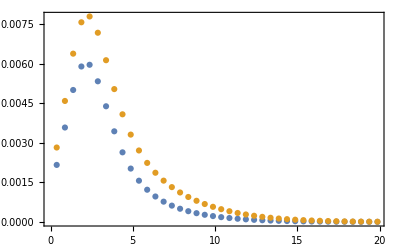

```mathematica
xx=RandomInteger[{1,Length@ls23d}]
ListPlot[{dataTrue,dataGen[[xx]]},PlotRange->{All,All},Frame->True]
```

### Chi square

```mathematica
(* χ^2 = 2 Sum[nteo - ndata + ndata*Log(ndata/nteo),{i,bin}] *)
```

```mathematica
(* data is SM *)
```

```mathematica
(* without bg *)
```

```mathematica
(* for 3.5 years *)
```

```mathematica
chis23d=Table[2*Sum[(dataGen[[j,i,2]])-(dataTrue[[i,2]])+(dataTrue[[i,2]])*Log[(dataTrue[[i,2]])/(dataGen[[j,i,2]])],{i,40}],{j,Length@dataGen}]//Chop
```

{4.31184,3.4437,2.67116,1.99474,1.41512,0.933288,0.550614,0.268931,0.0899668,0.0105977,0,0.0103929,0.0891785,0.267472,0.548486,0.930505,1.41169,1.99067,2.66647,3.43838,4.3059}

```mathematica
(* for 3.0 years *)
```

```mathematica
years=3/3.5;
```

```mathematica
chis23d=Table[2*Sum[(years*dataGen[[j,i,2]])-(years*dataTrue[[i,2]])+(years*dataTrue[[i,2]])*Log[(dataTrue[[i,2]])/(dataGen[[j,i,2]])],{i,40}],{j,Length@dataGen}]//Chop
```

{3.69586,2.95174,2.28957,1.70977,1.21296,0.799961,0.471954,0.230512,0.0771144,0.00908378,0,0.00890824,0.0764388,0.229261,0.470131,0.797575,1.21002,1.70629,2.28554,2.94718,3.69077}

```mathematica
(* with bg *)
```

```mathematica
(* for 3.5 years *)
```

```mathematica
chis23dbg=Table[2*Sum[(dataGen[[j,i,2]]+(1+27^2*ls23d[[j,1]]^2)*(1+α)*bg[[i,2]])-(dataTrue[[i,2]]+bg[[i,2]])+(dataTrue[[i,2]]+bg[[i,2]])*Log[(dataTrue[[i,2]]+bg[[i,2]])/(dataGen[[j,i,2]]+(1+27^2*ls23d[[j,1]]^2)*(1+α)*bg[[i,2]])],{i,40}]+(α/0.25)^2,{j,Length@dataGen},{α,-.5,.5,.05}]//Chop;
```

```mathematica
Table[α,{α,-.5,.5,.05}];
Table[i,{i,Length@%}];
la=Thread[%->%%]
```

{1→-0.5,2→-0.45,3→-0.4,4→-0.35,5→-0.3,6→-0.25,7→-0.2,8→-0.15,9→-0.1,10→-0.05,11→0.,12→0.05,13→0.1,14→0.15,15→0.2,16→0.25,17→0.3,18→0.35,19→0.4,20→0.45,21→0.5}

```mathematica
Min/@chis23dbg
(Table[Position[chis23dbg[[i]],%[[i]]],{i,Length@chis23dbg}]//Flatten)/.la
```

{0.561222,0.424147,0.299338,0.203442,0.131923,0.0804105,0.044835,0.0215962,0.00774022,0.00115391,0,0.00114162,0.00770286,0.0215241,0.0447137,0.0802213,0.131645,0.203049,0.298806,0.423448,0.560571}

{-0.05,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-0.05}

```mathematica
chis23dbg=Min/@chis23dbg;
```

```mathematica
(* for 3.0 years *)
```

```mathematica
years=3/3.5;
```

```mathematica
chis23dbg=Table[2*Sum[years*(dataGen[[j,i,2]]+(1+27^2*ls23d[[j,1]]^2)*(1+α)*bg[[i,2]])-years*(dataTrue[[i,2]]+bg[[i,2]])+years*(dataTrue[[i,2]]+bg[[i,2]])*Log[(dataTrue[[i,2]]+bg[[i,2]])/(dataGen[[j,i,2]]+(1+27^2*ls23d[[j,1]]^2)*(1+α)*bg[[i,2]])],{i,40}]+(α/0.25)^2,{j,Length@dataGen},{α,-.5,.5,.05}]//Chop;
```

```mathematica
Table[α,{α,-.5,.5,.05}];
Table[i,{i,Length@%}];
la=Thread[%->%%]
```

{1→-0.5,2→-0.45,3→-0.4,4→-0.35,5→-0.3,6→-0.25,7→-0.2,8→-0.15,9→-0.1,10→-0.05,11→0.,12→0.05,13→0.1,14→0.15,15→0.2,16→0.25,17→0.3,18→0.35,19→0.4,20→0.45,21→0.5}

```mathematica
Min/@chis23dbg
(Table[Position[chis23dbg[[i]],%[[i]]],{i,Length@chis23dbg}]//Flatten)/.la
```

{0.486762,0.363554,0.256576,0.174379,0.113077,0.0689233,0.03843,0.018511,0.00663448,0.000989068,0,0.000978533,0.00660245,0.0184492,0.038326,0.0687611,0.112838,0.174042,0.256119,0.362956,0.486204}

{-0.05,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-0.05}

```mathematica
chis23dbg=Min/@chis23dbg;
```

### chi2 data

```mathematica
dataSet2=chis23d;
dataSet2bg=chis23dbg;
```

### Data High

```mathematica
(* OS: Win, Linux *)
OS="Win";
```

```mathematica
(* ModeHE, ModeAntiNu, ModeNu *)
(* Tau_minus, Tau_plus *)
```

```mathematica
mode="HE";sign="minus";
If[mode=="Nu",range=40,range=20];
```

```mathematica
(* Linux *)
```

```mathematica
If[OS=="Linux",data=Import[StringJoin["/home/adriano/Dropbox/Neutrinos/Tau/Data/Mat_WS_In_Mode",mode,"_Tau_",sign,".txt"],"Table"];
data=Table[{.5*i-.25/2,data[[i,2]]},{i,40}];
data2=Import[StringJoin["/home/adriano/Dropbox/Neutrinos/Tau/Data/Mat_WoutS_In_Mode",mode,"_Tau_",sign,".txt"],"Table"];
data2=Table[{.5*i-.25/2,data2[[i,2]]},{i,40}];
bg=Import[StringJoin["/home/adriano/Dropbox/Neutrinos/Tau/Data/Mat_WS_In_Mode",mode,"_BG.txt"],"Table"];
bg=Table[{.5*i-.25/2,bg[[i,2]]},{i,40}],data=Import[StringJoin["C:\\Users\\Orlando\\Dropbox\\Neutrinos\\Tau\\Data\\Mat_WS_In_Mode",mode,"_Tau_",sign,".txt"],"Table"];
data=Table[{.5*i-.25/2,data[[i,2]]},{i,40}];
data2=Import[StringJoin["C:\\Users\\Orlando\\Dropbox\\Neutrinos\\Tau\\Data\\Mat_WoutS_In_Mode",mode,"_Tau_",sign,".txt"],"Table"];
data2=Table[{.5*i-.25/2,data2[[i,2]]},{i,40}];bg=Import[StringJoin["C:\\Users\\Orlando\\Dropbox\\Neutrinos\\Tau\\Data\\Mat_WS_In_Mode",mode,"_BG.txt"],"Table"];
bg=Table[{.5*i-.25/2,bg[[i,2]]},{i,40}]];
```

### Data of Fig 1 by reconstructed energy

```mathematica
Clear[fs,fn]
fs[Ere_,Etrue_]:=If[Etrue<3.1,0,(*1/(Sqrt[2Pi]σe)*)(Exp[-1/2((Ere-x)/σe)^2]/.{x->b*Etrue,σe->r*Etrue}/.Thread[{b,r}->{.45,.25}])]
fn[Ere_,Etrue_]:=If[Etrue<3.1,0,fs[Ere,Etrue]/NIntegrate[fs[ere,Etrue],{ere,0,20}]]
```

```mathematica
(* dN/Subscript[dE, rec]=∫dN/Subscript[dE, true] P(Subscript[E, rec],Subscript[E, true])ⅆ Subscript[E, true] *)
(* doing numerical integration by cutting the integrand *)
dataT=Table[{data2[[j,1]],Sum[fn[data2[[j,1]],data2[[i,1]]]*0.5*data2[[i,2]],{i,40}]},{j,40}];
(*dataT=Table[{.5*j-.25,Sum[fn[0.5*j-.25,.5*i-.25]*0.5*data2[[i,2]],{i,40}]},{j,40}]//Quiet;*)
dtrue=Interpolation@data2;
ndtrue=NIntegrate[dtrue[x],{x,Min@data[[All,1]],Max@data[[All,1]]}]
dre=Interpolation@data;
ndre=NIntegrate[dre[x],{x,Min@data[[All,1]],Max@data[[All,1]]}]
dreInt=Interpolation@dataT;
ndreInt=NIntegrate[dreInt[x],{x,Min@data[[All,1]],Max@data[[All,1]]}]
fac2=ndtrue/ndreInt
(*dataT=Table[{.5*j-.25,fac2*Sum[fn[0.5*j-.25,.5*i]*0.5*data2[[i,2]],{i,40}]},{j,40}]//Quiet;*)
dataT=Table[{data2[[j,1]],fac2*Sum[fn[data2[[j,1]],data2[[i,1]]]*0.5*data2[[i,2]],{i,40}]},{j,40}];
```

77.45

76.1852

75.6044

1.02441

```mathematica
ListPlot[{data,dataT},Frame->True,PlotRange->{{0,20},{0,40}},AspectRatio->1]
```

-Graphics-

### Creating data with NSI

```mathematica
(* Subscript[dN, nsi]/Subscript[dE, rec]=∫Subscript[dN, nsi]/Subscript[dE, true] P(Subscript[E, rec],Subscript[E, true])ⅆ Subscript[E, true] =∫(Subscript[P, NSI](μ->τ))/Subscript[P, SM(μ->τ)] Subscript[dN, sm]/Subscript[dE, true] P(Subscript[E, rec],Subscript[E, true])ⅆ Subscript[E, true] *)
```

```mathematica
(* best-fit used {S23,δ} = {0.582,-2.5} *)
```

```mathematica
passoNSI=2./20;
dataGen={};ls23d={};
Clear[delta,ss23];
Do[delta=(-1.+passoNSI*k)*10^-4;AppendTo[ls23d,{delta}];
AppendTo[dataGen,Table[{data2[[j,1]],(1300/1)^2*(70/40000)*fac2*Sum[fn[data2[[j,1]],data2[[i,1]]]*0.5*data2[[i,2]]*(ratioGen[0.582,-2.5,delta,.5*i]),{i,40}]},{j,40}]],{k,0,20}];
```

```mathematica
Plot[{ratioGen[0.582,-2.5,0,ee],ratioGen[0.582,-2.5,10^-4,ee],ratioGen[0.582,-2.5,10^-5,ee]},{ee,3.4,10}]
```

-Graphics-

```mathematica
dataGen//Dimensions
```

{21,40,2}

```mathematica
dataTrue=dataGen[[(((Length@dataGen)-1)/2+1)]]
```

{{0.375,0.0133131},{0.875,0.0215821},{1.375,0.0301183},{1.875,0.0361098},{2.375,0.0377928},{2.875,0.0355151},{3.375,0.0309509},{3.875,0.0257333},{4.375,0.0208155},{4.875,0.0165605},{5.375,0.013024},{5.875,0.0101466},{6.375,0.00783774},{6.875,0.00600583},{7.375,0.00456727},{7.875,0.00344868},{8.375,0.00258704},{8.875,0.00192922},{9.375,0.00143114},{9.875,0.00105687},{10.375,0.000777542},{10.875,0.000570338},{11.375,0.000417436},{11.875,0.000305101},{12.375,0.00022286},{12.875,0.000162808},{13.375,0.000119032},{13.875,0.0000871446},{14.375,0.0000639125},{14.875,0.0000469692},{15.375,0.0000345905},{15.875,0.0000255253},{16.375,0.0000188682},{16.875,0.0000139652},{17.375,0.0000103437},{17.875,7.66179×10^-6},{18.375,5.67151×10^-6},{18.875,4.19236×10^-6},{19.375,3.09234×10^-6},{19.875,2.27443×10^-6}}

11

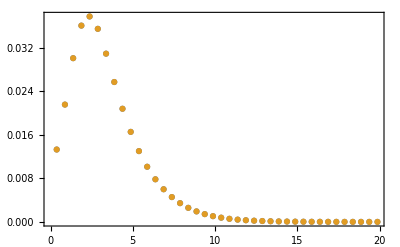

```mathematica
xx=RandomInteger[{1,Length@ls23d}]
ListPlot[{dataTrue,dataGen[[xx]]},PlotRange->{All,All},Frame->True]
```

### Chi square

```mathematica
(* χ^2 = 2 Sum[nteo - ndata + ndata*Log(ndata/nteo),{i,bin}] *)
```

```mathematica
(* data is SM *)
```

```mathematica
(* without bg *)
```

```mathematica
(* for 3.5 years *)
```

```mathematica
chis23d=Table[2*Sum[(dataGen[[j,i,2]])-(dataTrue[[i,2]])+(dataTrue[[i,2]])*Log[(dataTrue[[i,2]])/(dataGen[[j,i,2]])],{i,40}],{j,Length@dataGen}]//Chop
```

{27.527,21.9654,17.0176,12.6872,8.97889,5.8994,3.45828,1.66852,0.542882,0.0592865,0,0.0579531,0.537548,1.65859,3.44379,5.88045,8.95556,12.6596,16.9857,21.9292,27.4865}

```mathematica
(* for 3.0 years *)
```

```mathematica
years=3/3.5;
```

```mathematica
chis23d=Table[2*Sum[(years*dataGen[[j,i,2]])-(years*dataTrue[[i,2]])+(years*dataTrue[[i,2]])*Log[(dataTrue[[i,2]])/(dataGen[[j,i,2]])],{i,40}],{j,Length@dataGen}]//Chop
```

{23.5945,18.8275,14.5865,10.8747,7.69619,5.05663,2.96424,1.43016,0.465328,0.050817,0,0.0496741,0.460755,1.42165,2.95182,5.04038,7.67619,10.851,14.5592,18.7964,23.5599}

```mathematica
(* with bg *)
```

```mathematica
(* for 3.5 years *)
```

```mathematica
chis23dbg=Table[2*Sum[(dataGen[[j,i,2]]+(1+27^2*ls23d[[j,1]]^2)*(1+α)*bg[[i,2]])-(dataTrue[[i,2]]+bg[[i,2]])+(dataTrue[[i,2]]+bg[[i,2]])*Log[(dataTrue[[i,2]]+bg[[i,2]])/(dataGen[[j,i,2]]+(1+27^2*ls23d[[j,1]]^2)*(1+α)*bg[[i,2]])],{i,40}]+(α/0.25)^2,{j,Length@dataGen},{α,-.5,.5,.05}]//Chop;
```

```mathematica
Table[α,{α,-.5,.5,.05}];
Table[i,{i,Length@%}];
la=Thread[%->%%]
```

{1→-0.5,2→-0.45,3→-0.4,4→-0.35,5→-0.3,6→-0.25,7→-0.2,8→-0.15,9→-0.1,10→-0.05,11→0.,12→0.05,13→0.1,14→0.15,15→0.2,16→0.25,17→0.3,18→0.35,19→0.4,20→0.45,21→0.5}

```mathematica
Min/@chis23dbg
(Table[Position[chis23dbg[[i]],%[[i]]],{i,Length@chis23dbg}]//Flatten)/.la
```

{4.12745,2.89422,1.94958,1.25152,0.76404,0.445111,0.215526,0.111887,0.0365286,0.00416518,0,0.0041015,0.0362338,0.111692,0.214663,0.444055,0.761521,1.24816,1.94504,2.88812,4.1194}

{-0.3,-0.25,-0.2,-0.15,-0.1,-0.1,-0.05,-0.05,0.,0.,0.,0.,0.,-0.05,-0.05,-0.1,-0.1,-0.15,-0.2,-0.25,-0.3}

```mathematica
chis23dbg=Min/@chis23dbg;
```

```mathematica
(* for 3.0 years *)
```

```mathematica
years=3/3.5;
```

```mathematica
chis23dbg=Table[2*Sum[years*(dataGen[[j,i,2]]+(1+27^2*ls23d[[j,1]]^2)*(1+α)*bg[[i,2]])-years*(dataTrue[[i,2]]+bg[[i,2]])+years*(dataTrue[[i,2]]+bg[[i,2]])*Log[(dataTrue[[i,2]]+bg[[i,2]])/(dataGen[[j,i,2]]+(1+27^2*ls23d[[j,1]]^2)*(1+α)*bg[[i,2]])],{i,40}]+(α/0.25)^2,{j,Length@dataGen},{α,-.5,.5,.05}]//Chop;
```

```mathematica
Table[α,{α,-.5,.5,.05}];
Table[i,{i,Length@%}];
la=Thread[%->%%]
```

{1→-0.5,2→-0.45,3→-0.4,4→-0.35,5→-0.3,6→-0.25,7→-0.2,8→-0.15,9→-0.1,10→-0.05,11→0.,12→0.05,13→0.1,14→0.15,15→0.2,16→0.25,17→0.3,18→0.35,19→0.4,20→0.45,21→0.5}

```mathematica
Min/@chis23dbg
(Table[Position[chis23dbg[[i]],%[[i]]],{i,Length@chis23dbg}]//Flatten)/.la
```

{3.71793,2.61245,1.7625,1.12416,0.677748,0.40007,0.19045,0.101617,0.0313102,0.00357015,0,0.00351557,0.0310575,0.10145,0.189711,0.398397,0.675589,1.12128,1.75861,2.60613,3.7099}

{-0.25,-0.2,-0.2,-0.15,-0.1,-0.05,-0.05,-0.05,0.,0.,0.,0.,0.,-0.05,-0.05,-0.05,-0.1,-0.15,-0.2,-0.2,-0.25}

```mathematica
chis23dbg=Min/@chis23dbg;
```

### chi2 data

```mathematica
dataSet3=chis23d;
dataSet3bg=chis23dbg;
```

### Data

```mathematica
ls23d
```

{{-0.0001},{-0.00009},{-0.00008},{-0.00007},{-0.00006},{-0.00005},{-0.00004},{-0.00003},{-0.00002},{-0.00001},{0.},{0.00001},{0.00002},{0.00003},{0.00004},{0.00005},{0.00006},{0.00007},{0.00008},{0.00009},{0.0001}}

```mathematica
dataSet1
dataSet1bg
```

{9.55536,7.58459,5.83731,4.31522,3.02048,1.95585,1.12457,0.529384,0.168182,0.0186396,0,0.018215,0.166321,0.525635,1.11883,1.94813,3.0108,4.30361,5.82379,7.56918,9.53808}

{1.50483,1.06314,0.728713,0.487655,0.325009,0.195071,0.0994447,0.0431781,0.0138837,0.00187546,0,0.00185272,0.0137973,0.0429746,0.099049,0.194392,0.324414,0.486622,0.72713,1.0609,1.50182}

```mathematica
dataSet2
dataSet2bg
```

{3.69586,2.95174,2.28957,1.70977,1.21296,0.799961,0.471954,0.230512,0.0771144,0.00908378,0,0.00890824,0.0764388,0.229261,0.470131,0.797575,1.21002,1.70629,2.28554,2.94718,3.69077}

{0.486762,0.363554,0.256576,0.174379,0.113077,0.0689233,0.03843,0.018511,0.00663448,0.000989068,0,0.000978533,0.00660245,0.0184492,0.038326,0.0687611,0.112838,0.174042,0.256119,0.362956,0.486204}

```mathematica
dataSet3
dataSet3bg
```

{23.5945,18.8275,14.5865,10.8747,7.69619,5.05663,2.96424,1.43016,0.465328,0.050817,0,0.0496741,0.460755,1.42165,2.95182,5.04038,7.67619,10.851,14.5592,18.7964,23.5599}

{3.71793,2.61245,1.7625,1.12416,0.677748,0.40007,0.19045,0.101617,0.0313102,0.00357015,0,0.00351557,0.0310575,0.10145,0.189711,0.398397,0.675589,1.12128,1.75861,2.60613,3.7099}

### Contour

```mathematica
SetDirectory[NotebookDirectory[]]
```

C:\Users\Orlando\Dropbox\Neutrinos\Tau\Notebook

```mathematica
dataSet=dataSet1+dataSet2+dataSet3;
```

InterpolatingFunction[…]

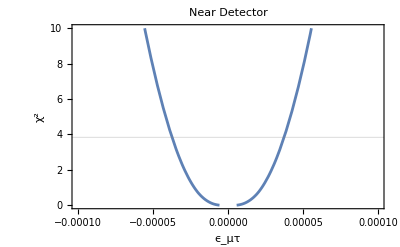

near_detector.pdf

```mathematica
Table[{ls23d[[i]],{dataSet[[i]]}},{i,Length@ls23d}];
func=Interpolation@%
Plot[func[del],{del,Min@ls23d[[All,1]],Max@ls23d[[All,1]]},GridLines->{{},{3.84}},PlotRange->{{Min@ls23d[[All,1]],Max@ls23d[[All,1]]},{0,10}},Frame->True,FrameLabel->{"ϵ_μτ","χ^2"},PlotLabel->"Near Detector"]
Export["near_detector.pdf",%]
```

```mathematica
dataSetbg=dataSet1bg+dataSet2bg+dataSet3bg;
```

InterpolatingFunction[…]

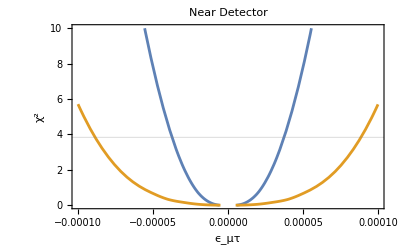

near_detector_bg.pdf

```mathematica
Table[{ls23d[[i]],{dataSetbg[[i]]}},{i,Length@ls23d}];
funcbg=Interpolation@%
Plot[{func[del],funcbg[del]},{del,Min@ls23d[[All,1]],Max@ls23d[[All,1]]},GridLines->{{},{3.84}},PlotRange->{{Min@ls23d[[All,1]],Max@ls23d[[All,1]]},{0,10}},Frame->True,FrameLabel->{"ϵ_μτ","χ^2"},PlotLabel->"Near Detector"]
Export["near_detector_bg.pdf",%]
```

### chi - α

```mathematica
(*nteo - ndata + ndata*Log(ndata/nteo)*)
```

```mathematica
chi=nsi+(1+a)*ncp-(n+nc)+(n+nc)*Log[(n+nc)/(nsi+(1+a)*ncp)]+(a/sg)^2
```

-n-nc+(1+a) ncp+nsi+a^2/sg^2+(n+nc) Log[(n+nc)/((1+a) ncp+nsi)]

```mathematica
Solve[D[chi,a]==0,a]//Simplify
chi/.%[[1,1]]//FullSimplify
%%/.{nsi->n,ncp->nc}//FullSimplify[#,Assumptions->Element[{nc,ncp,nsi,n,sg},Reals]]&
%/.{sg->0.25,nc->2,n->11}
ContourPlot[{%%[[1,1,2]]/.sg->0.25,%%[[2,1,2]]/.sg->0.25},{nc,0,10},{n,0,30}]
```

{{a→-(2 ncp+2 nsi+ncp^2 sg^2+√(-8 ncp^2 (-n-nc+ncp+nsi) sg^2+(2 ncp+2 nsi+ncp^2 sg^2)^2))/(4 ncp)},{a→(-2 ncp-2 nsi-ncp^2 sg^2+√(-8 ncp^2 (-n-nc+ncp+nsi) sg^2+(2 ncp+2 nsi+ncp^2 sg^2)^2))/(4 ncp)}}

-n-nc+ncp+nsi/2-1/4 ncp (2+ncp sg^2)-1/4 √(4 (ncp+nsi)^2-4 ncp^2 (-2 n-2 nc+ncp+nsi) sg^2+ncp^4 sg^4)+((2 nsi+ncp (2+ncp sg^2)+√(4 (ncp+nsi)^2-4 ncp^2 (-2 n-2 nc+ncp+nsi) sg^2+ncp^4 sg^4))^2)/(16 ncp^2 sg^2)+(n+nc) Log[-(4 (n+nc))/(-2 nsi+ncp (-2+ncp sg^2)+√(4 (ncp+nsi)^2-4 ncp^2 (-2 n-2 nc+ncp+nsi) sg^2+ncp^4 sg^4))]

{{a→-(2 n+nc (2+nc sg^2)+Abs[2 n+nc (2+nc sg^2)])/(4 nc)},{a→(-2 n-nc (2+nc sg^2)+Abs[2 n+nc (2+nc sg^2)])/(4 nc)}}

{{a→-6.5625},{a→0.}}

-Graphics-

```mathematica
(* this means a=0. Consistent, since for a=0 we must recover the data_True (chi=0)*)
(* Thus, we only use the second root *)
```

```mathematica
Solve[D[chi,a]==0,a]//Simplify
chi/.%[[1,1]]//FullSimplify
%%/.{nsi->10,ncp->1}//FullSimplify[#,Assumptions->Element[{nc,ncp,nsi,n,sg},Reals]]&
ContourPlot[{%[[1,1,2]]/.sg->0.25,%[[2,1,2]]/.sg->0.25},{nc,0,10},{n,0,30}]
```

{{a→-(2 ncp+2 nsi+ncp^2 sg^2+√(-8 ncp^2 (-n-nc+ncp+nsi) sg^2+(2 ncp+2 nsi+ncp^2 sg^2)^2))/(4 ncp)},{a→(-2 ncp-2 nsi-ncp^2 sg^2+√(-8 ncp^2 (-n-nc+ncp+nsi) sg^2+(2 ncp+2 nsi+ncp^2 sg^2)^2))/(4 ncp)}}

-n-nc+ncp+nsi/2-1/4 ncp (2+ncp sg^2)-1/4 √(4 (ncp+nsi)^2-4 ncp^2 (-2 n-2 nc+ncp+nsi) sg^2+ncp^4 sg^4)+((2 nsi+ncp (2+ncp sg^2)+√(4 (ncp+nsi)^2-4 ncp^2 (-2 n-2 nc+ncp+nsi) sg^2+ncp^4 sg^4))^2)/(16 ncp^2 sg^2)+(n+nc) Log[-(4 (n+nc))/(-2 nsi+ncp (-2+ncp sg^2)+√(4 (ncp+nsi)^2-4 ncp^2 (-2 n-2 nc+ncp+nsi) sg^2+ncp^4 sg^4))]

{{a→1/4 (-22-sg^2-√(484+(-44+8 n+8 nc) sg^2+sg^4))},{a→1/4 (-22-sg^2+√(484+(-44+8 n+8 nc) sg^2+sg^4))}}

-Graphics-

```mathematica
(* only second root makes sense*)
```